## Functions

### FitMySpotIntensity[img_,sigma_,dims_]

```mathematica
FitMySpotIntensity[img_,sigma_,dims_]:=Module[{myzs,my3Ddata,nlm,A,CC,x,x0,y,y0},
myzs=ImageData@img;
my3Ddata=Table[{i,j,myzs[[i,j]]},{i,1,dims,1},{j,1,dims,1}]//Flatten[#,1]&;
nlm=NonlinearModelFit[my3Ddata,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),{{CC,0},{x0,dims/2},{y0,dims/2},{A,0.5}},{x,y}];
{A/.nlm["BestFitParameters"],nlm["ParameterConfidenceIntervals"][[4]]}
]
```

### ImgCoord2DataCoord (integer)

```mathematica
Img2DataCoord[imageSize_,coordinate_]:=Module[{},
{#⟦2⟧,#⟦1⟧}&@Abs@({0,imageSize⟦2⟧+1}-Ceiling@coordinate)
]
```

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### MyThresholdingCrop (NEW - no rescale shit)

```mathematica
MyThresholdingCrop[img_,analysisFolder_, mytemplocs_, myPad_]:=Module[{myImg = img, myCrop},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
myImg ;
myCenterofCrop = { mytemplocs[[All,1]]//Median ,
mytemplocs[[All,2]]//Median  };


myCenterofVideoCropped = Table[  mytemplocs[[i]] - myCenterofCrop +{myPad + 0.1,myPad + 0.1},{i,1,Length@mytemplocs}];

mymessage = (*Test to see if any of the numbers GO OUTSIDE the pad: *)
 If [  
Cases[  Flatten@myCenterofVideoCropped,  x_/;x ≥ 2*myPad  || x<0 ]   == {} , 
"GOOD: all points are within pad size ", 
"Warning: the centroid goes out of the frame! "];

myCrop = Table[Table [ ImageTrim[myImg[[channel, time]], {#-myPad, #+myPad-0.1}&@ myCenterofCrop],{time, 1, Length@myImg[[1]],1}], {channel, 1, 3}];


Manipulate[
Column@{
mymessage,
Show[myCrop⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300]}, 
 
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myCrop⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thredcrop={threshold1,threshold2};
flagRed=ToString@thredcrop<>"Saved";
thredcrop>>analysisFolder<>"_thredcrop.dat"];
If[color==2,thgreencrop={threshold1,threshold2};flagGreen=ToString@thgreencrop<>"Saved";thgreencrop>>analysisFolder<>"_thgreencrop.dat"];
If[color==3,thbluecrop={threshold1,threshold2};flagBlue=ToString@thbluecrop<>"Saved";thbluecrop>>analysisFolder<>"_thbluecrop.dat"];
],
Spacer@5,
 
 
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredcrop,{threshold1,threshold2}=thredcrop];If[color==2&&ValueQ@thgreencrop,{threshold1,threshold2}=thgreencrop];If[color==3&&ValueQ@thbluecrop,{threshold1,threshold2}=thbluecrop]],
ControlPlacement->Left
]
]]
```

### MyThresholdingCropOLD

```mathematica
MyThresholdingCropOLD[img_,analysisFolder_, mytemplocs_, myPad_, myrescalefactor_]:=Module[{myImg = img, myCrop},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
myImg ;
myCenterofCrop = { mytemplocs[[All,1]]//Median ,
mytemplocs[[All,2]]//Median  };


myCenterofVideoCropped = Table[  mytemplocs[[i]] - myCenterofCrop +{myPad + 0.1,myPad + 0.1},{i,1,Length@mytemplocs}];

mymessage = (*Test to see if any of the numbers GO OUTSIDE the pad: *)
 If [  
Cases[  Flatten@myCenterofVideoCropped,  x_/;x ≥ 2*myPad  || x<0 ]   == {} , 
"GOOD: all points are within pad size ", 
"Warning: the centroid goes out of the frame! "];

myCrop = Table[Table[ ImageResize[ImageTrim[myImg[[channel, time]], {#-myPad, #+myPad-0.1}&@ myCenterofCrop],(2*myPad+1)*myRescaleFactor],{time, 1, Length@myImg[[1]],1}], {channel, 1, 3}];


Manipulate[
Column@{
mymessage,
Show[myCrop⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300]}, 
 
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myCrop⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thredcrop={threshold1,threshold2};
flagRed=ToString@thredcrop<>"Saved";
thredcrop>>analysisFolder<>"_thredcrop.dat"];
If[color==2,thgreencrop={threshold1,threshold2};flagGreen=ToString@thgreencrop<>"Saved";thgreencrop>>analysisFolder<>"_thgreencrop.dat"];
If[color==3,thbluecrop={threshold1,threshold2};flagBlue=ToString@thbluecrop<>"Saved";thbluecrop>>analysisFolder<>"_thbluecrop.dat"];
],
Spacer@5,
 
 
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredcrop,{threshold1,threshold2}=thredcrop];If[color==2&&ValueQ@thgreencrop,{threshold1,threshold2}=thgreencrop];If[color==3&&ValueQ@thbluecrop,{threshold1,threshold2}=thbluecrop]],
ControlPlacement->Left
]
]]
```

### MyThresholding

```mathematica
MyThresholding[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue.dat"),thblue=<<(analysisFolder<>"_thblue.dat");ToString@thblue<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,
"Blue Threshold : "<>flagBlue},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myImg⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];
If[color==3,thblue={threshold1,threshold2};flagBlue=ToString@thblue<>"Saved";thblue>>analysisFolder<>"_thblue.dat"];
],
Spacer@5,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];If[color==3&&ValueQ@thblue,{threshold1,threshold2}=thblue]],
ControlPlacement->Left
]
]]
```

```mathematica
MyThresholding3D[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue3D},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D.dat"),thblue3D=<<(analysisFolder<>"_thblue3D.dat");ToString@thblue3D<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦frame,z⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
(*"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,*)
"Blue Threshold 3D : "<>flagBlue3D},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
(*If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];*)
(*If[color==3,*)thblue3D={threshold1,threshold2};flagBlue3D=ToString@thblue3D<>"  Saved";thblue3D>>analysisFolder<>"_thblue3D.dat"(*]*);
],
Spacer@5,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];*)If[(*color==3&&*)ValueQ@thblue3D,{threshold1,threshold2}=thblue3D]],
ControlPlacement->Left
]
]]
```

### MyBinarization

```mathematica
MyBinarization[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue,max,imga,imgb,color,frame,threshold,lowpass,hipass,lo,hi,myOutline,myFill},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue2.dat"),thblueAll=<<(analysisFolder<>"_thblue2.dat");Append[ToString/@thblueAll,"Already Saved"],{"Not Yet Determined"}];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[
imga=ImageAdjust[myImg⟦color,frame⟧, {0, 0, 1},threshold1⟦color⟧];
max=BandPass[ImageMultiply[ImageAdjust[myImg⟦color,1⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=SelectComponents[ImageMultiply[Binarize[BandPass[imga,{lowpass,hipass}],max threshold],mask],"Count",lo<#<hi&];
Column@{GraphicsRow[{Show[If[myOutline==True&&myFill==False,{imga,Graphics[{Green,#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2⟧},If[myFill==True,{imga,Graphics[{Green,Polygon@#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2,1,1⟧},imga]]],imgb},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],
Prepend[flagBlue,"Blue Threshold 2  :"]}},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Row@{"Display options: ",Spacer@5,"outline ",Checkbox[Dynamic@myOutline],Spacer@10,"filled ",Checkbox[Dynamic@myFill]},
Spacer@10,
Button["Save Threshold 2",
If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];
If[color==3,thblueAll={mymaxblue=max,thblue2=threshold,bandpassblue={lowpass,hipass},dotsizeblue={lo,hi}};
flagBlue=Append[ToString/@thblueAll,"Saved"];
thblueAll>>analysisFolder<>"_thblue2.dat"];
],
Spacer@10,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];If[color==3&&ValueQ@thblueAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblueAll]]
]]]
```

```mathematica
MyBinarization3D[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue3D,max,imgb,color,frame,threshold,lowpass,hipass,lo,hi},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D2.dat"),thblue3DAll=<<(analysisFolder<>"_thblue3D2.dat");Append[ToString/@thblue3DAll,"  Already Saved"],{"Not Yet Determined"}];
color=1;
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[max=BandPass[ImageMultiply[ImageAdjust[myImg⟦1,Round@(Length@myImg⟦1⟧/2)⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[ImageAdjust[myImg⟦frame,z⟧ , {0, 0, 1}, threshold1⟦color⟧],{lowpass,hipass}];
Column@{GraphicsRow[{ImageAdjust[myImg⟦frame,z⟧, {0, 0, 1},threshold1⟦color⟧],
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mask],"Count",lo<#<hi&]},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
(*Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],*)
Prepend[flagBlue3D,"Blue Threshold 3D 2  :"]}},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Button["Save Threshold 3D 2",
(*If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];*)
(*If[color==3,*)thblue3DAll={mymaxblue3D=max,thblue3D2=threshold,bandpassblue3D={lowpass,hipass},dotsizeblue3D={lo,hi}};
flagBlue3D=Append[ToString/@thblue3DAll,"  Saved"];
thblue3DAll>>analysisFolder<>"_thblue3D2.dat"(*];*)
],
Spacer@10,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];*)If[(*color==3&&*)ValueQ@thblue3DAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblue3DAll]]
]]]
```

### FindParticles

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],"Count",small<#<large&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticles[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,compResults},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&];
compResults=ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
compResults⟦All,2⟧
]
```

```mathematica
(* After finding particles, add track number as 0, and add frame number *)
MyParticleFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
result=FindParticles[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧;
result=Table[Thread@{i,result⟦i⟧},{i,1,Length@result,1}];
result=Prepend[#,0]&/@#&/@result
]
```

```mathematica
FindGranuleMasks[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&]
]
```

```mathematica
myGranuleMaskFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
FindGranuleMasks[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input does not have color code such as {1,0,0} for red *)
ParticleFitting2[myColMovie_,channel_,mylongtracks_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
myTrimSize=2*pad+1;
Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
MyParticleFitter[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
ParticleFitting3[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;

Table[
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[mySpots⟦frame,spot,2⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,frame+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,Length@Flatten@track1⟦1⟧]&; 
t2=track2//Flatten//Partition[#,Length@Flatten@track2⟦1⟧]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
t1⟦All,{1,2}⟧=t1⟦All,{2,1}⟧;
t2⟦All,{1,2}⟧=t2⟦All,{2,1}⟧;
ol={t1,t2}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### NearestNeighborLinking

```mathematica
(* Using a globally determined (automatic) threshod for binarization *)
NearestNeighborLinking1[img_,channel_,startFrame_,startPosition_,pad_,bandpass_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust@myTrimImg,bandpass]],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
(* Using user defined threshod for binarization *)
NearestNeighborLinking2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
NearestNeighborLinking3D2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

### ClickAndTrack

```mathematica
ClickAndTrack[imgRaw_,img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTrackNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];],
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames[StringDelete[#,DirectoryName@#]<>"_myTrack_"<>myColor<>"*",DirectoryName@#]&@analysisFolder;
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->150]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->150]]
}
}}]
]]
```

```mathematica
ClickAndTrack3D[(*imgRaw_,*)img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{(*"_thred2.dat","_thgreen2.dat",*)"_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTruckNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];](*,
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames["*_myTrack_"<>myColor<>"*",DirectoryName@analysisFolder];
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->300]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->300]]
}
}}]
]]
```

### FilterFitOutlier

```mathematica
(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma *)
FilterFitOutlier[mySpotsFit_,maxDxy_,maxSig_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
idxInt=Position[mySpotsFit⟦All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxSigX=Position[mySpotsFit⟦All,All,4,3,1⟧,x_/;Abs@x>maxSig];
idxSigY=Position[mySpotsFit⟦All,All,4,3,2⟧,x_/;Abs@x>maxSig];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
Delete[mySpotsFit,idxOutliers]
]
```

### SpotLocationOnCell

```mathematica
(* function to show cell movie with tracked spot positions *)
SpotLocationOnCell[myColMovie_,thred_,redSpots_,thgreen_,greenSpots_,thblue_,blueSpots_]:=Module[{th,colCircle,spots},
Manipulate[If[color==1,th=thred;colCircle=Red;spots=redSpots,
If[color==2,th=thgreen;colCircle=Green;spots=greenSpots,
th=thblue;colCircle=Blue;spots=blueSpots]];
Show[ImageAdjust[myColMovie⟦color,frame⟧,{0,0,1},th],Graphics[{colCircle,Circle[#,7]}&/@spots⟦frame⟧]],{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myColMovie⟦1⟧,1},ControlType->{RadioButtonBar,Automatic}]
]
```

### ShiftingDataPoints

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMin[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
myStart=(#-Min@#)+1&@Round@(10*myOffset);
myDataResample=Table[myDataInterpol⟦i,myStart⟦i⟧;;⟧,{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[myDataResample⟦i⟧,ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMean[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
(*myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;*)
myDataInterpol=Table[Array[myDataInterpolFunc⟦i⟧,1+myResolution*(Length@myData⟦i⟧-1),{1,Length@myData⟦i⟧}],{i,1,Length@myData,1}];
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset);
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[{myDataResample⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
myAllBlueNum
```

myAllBlueNum

```mathematica
ShiftingDataPointsMin[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
ShiftingDataPointsMean[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
test=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myData=myAllBlueNum;
```

```mathematica
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
```

```mathematica
myDataInterpol=Array[#,1+10*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
```

```mathematica
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
```

```mathematica
test=myDataResample⟦All,;;All;;10⟧
```

{}

```mathematica
myFillSize=Max@#-#&@(Length/@test)
```

{}

```mathematica
myDataResample=Table[Flatten[Append[{test⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@test,1}]
```

{}

```mathematica
ConstantArray[{},]
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},Null].

ConstantArray[{},Null]

```mathematica
Flatten[Append[{test⟦10⟧},ConstantArray[{},myFillSize⟦10⟧]],1]
```

Part::partw: Part 10 of {} does not exist.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},{}⟦10⟧].

{{}⟦10⟧,ConstantArray[{},{}⟦10⟧]}

```mathematica
myDataResample⟦10⟧
```

Part::partw: Part 10 of {} does not exist.

{}⟦10⟧

## RollingAvg particle fitting fxn

MyParticleFitterRollingAvgCC takes the 2 frame ROLLING AVG of each set of trims. 
This should help pull out the centroids and get more accurate intensity measurements ... 
NOTE the shift is 0.5*time period SHORTER than reality! (  added extra last frame to the end.  “True” time is 0.5, 1.5, 2.5... instead of 1,2,3...  )

```mathematica
MyParticleFitterRollingAvgCC[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs0, myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs0 ,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
(*  myTrimImgs = Flatten@{myTrimImgs0[[1]], Table[Mean@myTrimImgs0[[i;;i+1]], {i,1,Length@myTrimImgs0-1}]}; (*adds extra frame to beginning*)  *)
myTrimImgs = Flatten@{Table[Mean@myTrimImgs0[[i;;i+1]], {i,1,Length@myTrimImgs0-1}]  ,  myTrimImgs0[[-1]]};


myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

## Resampling + RollingAvg particle fitting fxn

MyParticleFitterRollingAvgCC takes the 2 frame ROLLING AVG of each set of trims. 
This should help pull out the centroids and get more accurate intensity measurements ... 
NOTE the shift is 0.5*time period SHORTER than reality! (  added extra last frame to the end.  “True” time is 0.5, 1.5, 2.5... instead of 1,2,3...  )

```mathematica
MyParticleFitterRollingAvgCC[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs0, myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];
myRollingAvgShift = 2;

Table[
{myTrimImgs0 ,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;

myTrimImgs00 = ImageResize[ #, 3*{myTrimSize, myTrimSize}, Resampling->"Cubic"]&/@myTrimImgs0   ;
myTrimImgs = Table[Mean@myTrimImgs0[[i;;i+myRollingAvgShift]], {i,1,Length@myTrimImgs0-myRollingAvgShift}]  ; 


myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

# OLD

Functions

### ImgCoord2DataCoord (integer)

```mathematica
Img2DataCoord[imageSize_,coordinate_]:=Module[{},
{#⟦2⟧,#⟦1⟧}&@Abs@({0,imageSize⟦2⟧+1}-Ceiling@coordinate)
]
```

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### MyThresholding

```mathematica
MyThresholding[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue.dat"),thblue=<<(analysisFolder<>"_thblue.dat");ToString@thblue<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,
"Blue Threshold : "<>flagBlue},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myImg⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];
If[color==3,thblue={threshold1,threshold2};flagBlue=ToString@thblue<>"Saved";thblue>>analysisFolder<>"_thblue.dat"];
],
Spacer@5,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];If[color==3&&ValueQ@thblue,{threshold1,threshold2}=thblue]],
ControlPlacement->Left
]
]]
```

```mathematica
MyThresholding3D[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue3D},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D.dat"),thblue3D=<<(analysisFolder<>"_thblue3D.dat");ToString@thblue3D<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦frame,z⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
(*"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,*)
"Blue Threshold 3D : "<>flagBlue3D},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
(*If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];*)
(*If[color==3,*)thblue3D={threshold1,threshold2};flagBlue3D=ToString@thblue3D<>"  Saved";thblue3D>>analysisFolder<>"_thblue3D.dat"(*]*);
],
Spacer@5,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];*)If[(*color==3&&*)ValueQ@thblue3D,{threshold1,threshold2}=thblue3D]],
ControlPlacement->Left
]
]]
```

### MyBinarization

```mathematica
MyBinarization[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue,max,imga,imgb,color,frame,threshold,lowpass,hipass,lo,hi,myOutline,myFill},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue2.dat"),thblueAll=<<(analysisFolder<>"_thblue2.dat");Append[ToString/@thblueAll,"Already Saved"],{"Not Yet Determined"}];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[
imga=ImageAdjust[myImg⟦color,frame⟧, {0, 0, 1},threshold1⟦color⟧];
max=BandPass[ImageMultiply[ImageAdjust[myImg⟦color,1⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=SelectComponents[ImageMultiply[Binarize[BandPass[imga,{lowpass,hipass}],max threshold],mask],"Count",lo<#<hi&];
Column@{GraphicsRow[{Show[If[myOutline==True&&myFill==False,{imga,Graphics[{Green,#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2⟧},If[myFill==True,{imga,Graphics[{Green,Polygon@#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2,1,1⟧},imga]]],imgb},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],
Prepend[flagBlue,"Blue Threshold 2  :"]}},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Row@{"Display options: ",Spacer@5,"outline ",Checkbox[Dynamic@myOutline],Spacer@10,"filled ",Checkbox[Dynamic@myFill]},
Spacer@10,
Button["Save Threshold 2",
If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];
If[color==3,thblueAll={mymaxblue=max,thblue2=threshold,bandpassblue={lowpass,hipass},dotsizeblue={lo,hi}};
flagBlue=Append[ToString/@thblueAll,"Saved"];
thblueAll>>analysisFolder<>"_thblue2.dat"];
],
Spacer@10,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];If[color==3&&ValueQ@thblueAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblueAll]]
]]]
```

```mathematica
MyBinarization3D[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue3D,max,imgb,color,frame,threshold,lowpass,hipass,lo,hi},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D2.dat"),thblue3DAll=<<(analysisFolder<>"_thblue3D2.dat");Append[ToString/@thblue3DAll,"  Already Saved"],{"Not Yet Determined"}];
color=1;
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[max=BandPass[ImageMultiply[ImageAdjust[myImg⟦1,Round@(Length@myImg⟦1⟧/2)⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[ImageAdjust[myImg⟦frame,z⟧ , {0, 0, 1}, threshold1⟦color⟧],{lowpass,hipass}];
Column@{GraphicsRow[{ImageAdjust[myImg⟦frame,z⟧, {0, 0, 1},threshold1⟦color⟧],
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mask],"Count",lo<#<hi&]},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
(*Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],*)
Prepend[flagBlue3D,"Blue Threshold 3D 2  :"]}},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Button["Save Threshold 3D 2",
(*If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];*)
(*If[color==3,*)thblue3DAll={mymaxblue3D=max,thblue3D2=threshold,bandpassblue3D={lowpass,hipass},dotsizeblue3D={lo,hi}};
flagBlue3D=Append[ToString/@thblue3DAll,"  Saved"];
thblue3DAll>>analysisFolder<>"_thblue3D2.dat"(*];*)
],
Spacer@10,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];*)If[(*color==3&&*)ValueQ@thblue3DAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblue3DAll]]
]]]
```

### FindParticles

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],"Count",small<#<large&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticles[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,compResults},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&];
compResults=ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
compResults⟦All,2⟧
]
```

```mathematica
(* After finding particles, add track number as 0, and add frame number *)
MyParticleFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
result=FindParticles[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧;
result=Table[Thread@{i,result⟦i⟧},{i,1,Length@result,1}];
result=Prepend[#,0]&/@#&/@result
]
```

```mathematica
FindGranuleMasks[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&]
]
```

```mathematica
myGranuleMaskFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
FindGranuleMasks[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input does not have color code such as {1,0,0} for red *)
ParticleFitting2[myColMovie_,channel_,mylongtracks_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
myTrimSize=2*pad+1;
Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
MyParticleFitter[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
MyParticleFitterFixedSigma[myColMovie_,channel_,mySpots_,pad_,avgFrameN_,sigma_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;

myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
ParticleFitting3[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;

Table[
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[mySpots⟦frame,spot,2⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,frame+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,Length@Flatten@track1⟦1⟧]&; 
t2=track2//Flatten//Partition[#,Length@Flatten@track2⟦1⟧]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
t1⟦All,{1,2}⟧=t1⟦All,{2,1}⟧;
t2⟦All,{1,2}⟧=t2⟦All,{2,1}⟧;
ol={t1,t2}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### NearestNeighborLinking

```mathematica
(* Using a globally determined (automatic) threshod for binarization *)
NearestNeighborLinking1[img_,channel_,startFrame_,startPosition_,pad_,bandpass_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust@myTrimImg,bandpass]],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
(* Using user defined threshod for binarization *)
NearestNeighborLinking2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
NearestNeighborLinking3D2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

### ClickAndTrack

```mathematica
ClickAndTrack[imgRaw_,img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTruckNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];],
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames["*_myTrack_"<>myColor<>"*",DirectoryName@analysisFolder];
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->300]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->300]]
}
}}]
]]
```

```mathematica
ClickAndTrack3D[(*imgRaw_,*)img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{(*"_thred2.dat","_thgreen2.dat",*)"_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTruckNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];](*,
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames["*_myTrack_"<>myColor<>"*",DirectoryName@analysisFolder];
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->300]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->300]]
}
}}]
]]
```

### FilterFitOutlier

```mathematica
(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma *)
FilterFitOutlier[mySpotsFit_,maxDxy_,maxSig_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
idxInt=Position[mySpotsFit⟦All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxSigX=Position[mySpotsFit⟦All,All,4,3,1⟧,x_/;Abs@x>maxSig];
idxSigY=Position[mySpotsFit⟦All,All,4,3,2⟧,x_/;Abs@x>maxSig];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
Delete[mySpotsFit,idxOutliers]
]
```

### SpotLocationOnCell

```mathematica
(* function to show cell movie with tracked spot positions *)
SpotLocationOnCell[myColMovie_,thred_,redSpots_,thgreen_,greenSpots_,thblue_,blueSpots_]:=Module[{th,colCircle,spots},
Manipulate[If[color==1,th=thred;colCircle=Red;spots=redSpots,
If[color==2,th=thgreen;colCircle=Green;spots=greenSpots,
th=thblue;colCircle=Blue;spots=blueSpots]];
Show[ImageAdjust[myColMovie⟦color,frame⟧,{0,0,1},th],Graphics[{colCircle,Circle[#,7]}&/@spots⟦frame⟧]],{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myColMovie⟦1⟧,1},ControlType->{RadioButtonBar,Automatic}]
]
```

### ShiftingDataPoints

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMin[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
myStart=(#-Min@#)+1&@Round@(10*myOffset);
myDataResample=Table[myDataInterpol⟦i,myStart⟦i⟧;;⟧,{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[myDataResample⟦i⟧,ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMean[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
(*myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;*)
myDataInterpol=Table[Array[myDataInterpolFunc⟦i⟧,1+myResolution*(Length@myData⟦i⟧-1),{1,Length@myData⟦i⟧}],{i,1,Length@myData,1}];
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset);
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[{myDataResample⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
myAllBlueNum
```

myAllBlueNum

```mathematica
ShiftingDataPointsMin[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
ShiftingDataPointsMean[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
test=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myData=myAllBlueNum;
```

```mathematica
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
```

```mathematica
myDataInterpol=Array[#,1+10*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
```

```mathematica
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
```

```mathematica
test=myDataResample⟦All,;;All;;10⟧
```

{}

```mathematica
myFillSize=Max@#-#&@(Length/@test)
```

{}

```mathematica
myDataResample=Table[Flatten[Append[{test⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@test,1}]
```

{}

```mathematica
ConstantArray[{},]
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},Null].

ConstantArray[{},Null]

```mathematica
Flatten[Append[{test⟦10⟧},ConstantArray[{},myFillSize⟦10⟧]],1]
```

Part::partw: Part 10 of {} does not exist.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},{}⟦10⟧].

{{}⟦10⟧,ConstantArray[{},{}⟦10⟧]}

```mathematica
myDataResample⟦10⟧
```

Part::partw: Part 10 of {} does not exist.

{}⟦10⟧

### MyCropMaker

```mathematica
MyCropMaker[myColMovie_,myRNAtracks_,pad_,analysisFolder_]:=Module[{myTfFunc,avgFrameN,myCrops,tempTime,tempCenter,tempCenterColReg,tempRed,tempGreen,tempBlue,myCropsAvg},
myTfFunc=<<(FileNames["TransformationFunction.m",ParentDirectory@DirectoryName@analysisFolder]⟦1⟧);
avgFrameN=<<(FileNames["*avgFrameN*",DirectoryName@analysisFolder]⟦1⟧);
myCrops=
	Table[
		Table[
		tempTime=myRNAtracks⟦track,frame,2⟧;
		tempCenter=Ceiling[myRNAtracks⟦track,frame,3,1⟧];
		tempCenterColReg=Ceiling[myTfFunc@myRNAtracks⟦track,frame,3,1⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myRNAtracks⟦track⟧,1}],
	{track,1,Length@myRNAtracks,1}];
myCrops>>analysisFolder<>"_Crops.m";
myCropsAvg=Mean/@#&/@Transpose/@myCrops;
myCropsAvg>>analysisFolder<>"_Crops_AVG.m";
{myCrops,myCropsAvg}]
```

### MyAutoCategorization

```mathematica
MyAutoCategorization[myCropsAvg_,myRNAtracks_,lowpass_,highpass_]:=Module[{myCropsAvgBandPass,myCropsAvgBinari,myCropsAvgBinariSort,myCropsAvgBinariData,myCropsAvgBinariDataDigital,idx1,idx2,idx3,idx4,idx,myAvgCropsCategorized,myRNAtracksCategorized},
myCropsAvgBandPass=BandPass[#,{lowpass,highpass}]&/@#&/@myCropsAvg;
myCropsAvgBinari=Binarize/@#&/@myCropsAvgBandPass;
myCropsAvgBinariSort=SelectComponents[#,#AdjacentBorderCount==0&&#Count >3&]&/@#&/@myCropsAvgBinari;
myCropsAvgBinariData=Flatten[ComponentMeasurements[#,"Count"]&/@#&/@myCropsAvgBinariSort,1];
myCropsAvgBinariData⟦Position[myCropsAvgBinariData,{}]//Flatten⟧={0->0};
myCropsAvgBinariDataDigital=Partition[Total/@myCropsAvgBinariData⟦All,All,2⟧,3];
myCropsAvgBinariDataDigital=Thread@{Range@Length@#,#}&@myCropsAvgBinariDataDigital⟦All,{2,3}⟧;
idx1=(Cases[myCropsAvgBinariDataDigital,x_/;x⟦2,1⟧==0&&x⟦2,2⟧==0])⟦All,1⟧;
idx2=(Cases[myCropsAvgBinariDataDigital,x_/;x⟦2,1⟧>0&&x⟦2,2⟧==0])⟦All,1⟧;
idx3=(Cases[myCropsAvgBinariDataDigital,x_/;x⟦2,1⟧==0&&x⟦2,2⟧>0])⟦All,1⟧;
idx4=(Cases[myCropsAvgBinariDataDigital,x_/;x⟦2,1⟧>0&&x⟦2,2⟧>0])⟦All,1⟧;
idx={idx1,idx2,idx3,idx4};
myAvgCropsCategorized=ImageAdjust/@#&/@#&/@Table[myCropsAvg⟦idx⟦i⟧⟧,{i,1,4,1}];
myRNAtracksCategorized=Table[myRNAtracks⟦idx⟦i⟧⟧,{i,1,4,1}];
{myAvgCropsCategorized,myRNAtracksCategorized}
]
```

### MyCategoryHandChecker

```mathematica
MyCategoryHandChecker[myAvgCropsCategorized_,myRNAtracksCategorized_]:=Module[{myTFidx,myIdx,myIdxSplit},
myTFidx={{True,False,False},{True,True,False},{True,False,True},{True,True,True}};
myIdx=Flatten[Table[ConstantArray[myTFidx⟦color⟧,Length@myAvgCropsCategorized⟦color⟧],{color,1,Length@myAvgCropsCategorized,1}],1];
myIdxSplit=Thread@{Prepend[#⟦;;3⟧+1,1],#}&@Accumulate@(Length/@myAvgCropsCategorized);
DynamicModule[{myDynamicIdx,myDynamicIdxSplit,myIdxNomore},
myDynamicIdx=myIdx;
Column@{Grid@Prepend[Flatten[#,1]&/@Thread@{Table["Spot "<>ToString@spot,{spot,1,Length@myIdx,1}],Flatten[myAvgCropsCategorized,1],Partition[Checkbox/@ToExpression/@Flatten@Table[Table["Dynamic@myDynamicIdx⟦"<>ToString@spot<>","<>ToString@color<>"⟧",{color,1,3,1}],{spot,1,Length@myDynamicIdx,1}],3]},{"","R","G","B","R","G","B"}],
Button["Done Checking!",
myDynamicIdxSplit=Table[myDynamicIdx⟦myIdxSplit⟦color,1⟧;;myIdxSplit⟦color,2⟧⟧,{color,1,Length@myIdxSplit,1}];
myRNAtracksHC=Table[myRNAtracksCategorized⟦color,Flatten@Position[#==myTFidx⟦color⟧&/@myDynamicIdxSplit⟦color⟧,True]⟧,{color,1,4,1}];
myAvgCropsHC=Table[myAvgCropsCategorized⟦color,Flatten@Position[#==myTFidx⟦color⟧&/@myDynamicIdxSplit⟦color⟧,True]⟧,{color,1,4,1}];
myIdxNomore=Table[Flatten@Position[#==myTFidx⟦color⟧&/@myDynamicIdxSplit⟦color⟧,False],{color,1,Length@myDynamicIdxSplit,1}];
Table[
Table[
Table[If[myDynamicIdxSplit⟦color,spot⟧==myTFidx⟦j⟧,myRNAtracksHC⟦j⟧=Append[myRNAtracksHC⟦j⟧,myRNAtracksCategorized⟦color,spot⟧];myAvgCropsHC⟦j⟧=Append[myAvgCropsHC⟦j⟧,myAvgCropsCategorized⟦color,spot⟧];
]
,{j,1,Length@myTFidx,1}]
,{spot,myIdxNomore⟦color⟧}],
{color,1,4,1}];
myAvgCropsHC=Table[Last/@SortBy[Flatten[#,1]&/@Thread@{myRNAtracksHC⟦color⟧,{#}&/@myAvgCropsHC⟦color⟧},First],{color,1,4,1}];
myRNAtracksHC=SortBy[#,First]&/@myRNAtracksHC;
myRNAtracksHC>>analysisFolder<>"_myRNAtracksHC.m";
myAvgCropsHC>>analysisFolder<>"_myAvgCropsHC.m";]}]]
```

### MyCategorizedTrackFitter

```mathematica
MyCategorizedTrackFitter[myRNAtracksHC_,myColMovie_,analysisFolder_,sigma_]:=Module[{myRNAtracksHCColReg,myTfFunc,avgFrameN,myRedfitsR,myRedfitsY,myRedfitsP,myRedfitsW,myGreenfitsY,myGreenfitsW,myBluefitsP,myBluefitsW,myAllfits},
myRNAtracksHCColReg=myRNAtracksHC;
myTfFunc=<<(ParentDirectory@DirectoryName@analysisFolder<>"/TransformationFunction.m");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myRNAtracksHCColReg⟦All,All,All,3,1⟧=myTfFunc/@#&/@#&/@myRNAtracksHC⟦All,All,All,3,1⟧;

If[myRNAtracksHC⟦1⟧≠{},
{myRedfitsR,myRedCroppedDataR,myRedCentersR}=MyParticleFitterFixedSigma[myColMovie,1,myRNAtracksHC⟦1⟧,5,avgFrameN,sigma];,
myRedfitsR={};];
myRedfitsR>>analysisFolder<>"myRedfitsR.m";

If[myRNAtracksHC⟦2⟧≠{},
{myRedfitsY,myRedCroppedDataY,myRedCentersY}=MyParticleFitterFixedSigma[myColMovie,1,myRNAtracksHC⟦2⟧,5,avgFrameN,sigma];,
myRedfitsY={};];
myRedfitsY>>analysisFolder<>"myRedfitsY.m";

If[myRNAtracksHC⟦3⟧≠{},
{myRedfitsP,myRedCroppedDataP,myRedCentersP}=MyParticleFitterFixedSigma[myColMovie,1,myRNAtracksHC⟦3⟧,5,avgFrameN,sigma];,
myRedfitsP={};];
myRedfitsP>>analysisFolder<>"myRedfitsP.m";

If[myRNAtracksHC⟦4⟧≠{},
{myRedfitsW,myRedCroppedDataW,myRedCentersW}=MyParticleFitterFixedSigma[myColMovie,1,myRNAtracksHC⟦4⟧,5,avgFrameN,sigma];,
myRedfitsW={};];
myRedfitsW>>analysisFolder<>"myRedfitsW.m";

If[myRNAtracksHC⟦2⟧≠{},
{myGreenfitsY,myGreenCroppedDataY,myGreenCentersY}=MyParticleFitterFixedSigma[myColMovie,2,myRNAtracksHCColReg⟦2⟧,5,avgFrameN,sigma];,
myGreenfitsY={};];
myGreenfitsY>>analysisFolder<>"myGreenfitsY.m";

If[myRNAtracksHC⟦4⟧≠{},
{myGreenfitsW,myGreenCroppedDataW,myGreenCentersW}=MyParticleFitterFixedSigma[myColMovie,2,myRNAtracksHCColReg⟦4⟧,5,avgFrameN,sigma];,
myGreenfitsW={};];
myGreenfitsW>>analysisFolder<>"myGreenfitsW.m";

If[myRNAtracksHC⟦3⟧≠{},
{myBluefitsP,myBlueCroppedDataP,myBlueCentersP}=MyParticleFitterFixedSigma[myColMovie,3,myRNAtracksHCColReg⟦3⟧,5,avgFrameN,sigma];,
myBluefitsP={};];
myBluefitsP>>analysisFolder<>"myBluefitsP.m";

If[myRNAtracksHC⟦4⟧≠{},
{myBluefitsW,myBlueCroppedDataW,myBlueCentersW}=MyParticleFitterFixedSigma[myColMovie,3,myRNAtracksHCColReg⟦4⟧,5,avgFrameN,sigma];,
myBluefitsW={};];
myBluefitsW>>analysisFolder<>"myBluefitsW.m";

myAllfits={myRedfitsR,myRedfitsY,myRedfitsP,myRedfitsW,myGreenfitsY,myGreenfitsW,myBluefitsP,myBluefitsW}]
```

### MyFilterFitOutlierFixedSigma

```mathematica
(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma *)
FilterFitOutlierFixedSigma[mySpotsFit_,maxDxy_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxOutliers},
idxInt=Position[mySpotsFit⟦All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf];
Delete[mySpotsFit,idxOutliers]
]
```

### GetMyAllParameters

Need to remove frames where red channel fail to fit.

```mathematica
GetMyAllParameters[myAllfits_,myAllfitsFiltered_,analysisFolder_]:=Module[{ch1,ch2},
(* preparing empty list for {track#, frame#, Ir, Ig, Ib, Xr, Yr, Xg, Yg, Xb, Yb} *)
myAllParameters=ConstantArray[{},{Length@#,11}]&/@#&/@myAllfits⟦;;4⟧;
(* track# and frame# *)
myAllParameters⟦;;4,All,All,{1,2}⟧=myAllfits⟦;;4,All,All,{1,2}⟧; 
(* Intensity & XY coordinate of Red channel for Red Only *)
idx=myAllfitsFiltered⟦1,All,All,2⟧-(myAllParameters⟦1,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦1,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦1,track,frame,4,2,1⟧;
myAllParameters⟦1,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦1⟧,1}];
(* Intensity & XY coordinate of Red channel for Yellow *)
If[myAllfits⟦2⟧≠{},idx=myAllfitsFiltered⟦2,All,All,2⟧-(myAllParameters⟦2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦2,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦2,track,frame,4,2,1⟧;
myAllParameters⟦2,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦2,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦2,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦2⟧,1}];];
(* Intensity & XY coordinate of Red channel for Purple *)
If[myAllfits⟦3⟧≠{},idx=myAllfitsFiltered⟦3,All,All,2⟧-(myAllParameters⟦3,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦3,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦3,track,frame,4,2,1⟧;
myAllParameters⟦3,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦3,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦3,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦3⟧,1}];];
(* Intensity & XY coordinate of Red channel for White *)
If[myAllfits⟦4⟧≠{},idx=myAllfitsFiltered⟦4,All,All,2⟧-(myAllParameters⟦4,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦4,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦4,track,frame,4,2,1⟧;
myAllParameters⟦4,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦4,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦4,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦4⟧,1}];];
(* Intensity & XY coordinate of Green channel for Yellow *)
ch1=5;ch2=2;
If[myAllfits⟦2⟧≠{},idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,4⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{8,9}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];];
(* Intensity & XY coordinate of Green channel for White *)
ch1=6;ch2=4;
If[myAllfits⟦4⟧≠{},idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,4⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{8,9}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];];
(* Intensity & XY coordinate of Blue channel for Purple *)
ch1=7;ch2=3;
If[myAllfits⟦3⟧≠{},idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,5⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{10,11}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];];
(* Intensity & XY coordinate of Blue channel for White *)
ch1=8;ch2=4;
If[myAllfits⟦4⟧≠{},idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,5⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{10,11}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];];
(* Delete frames which there is no red channel *)
(*idx=Position[myAllParameters⟦All,All,All,3⟧,{}];
myAllParameters=Delete[myAllParameters,idx];*)
myAllParameters>>analysisFolder<>"_myAllParameters";
myAllParameters]
```

```mathematica
GetMyAllParametersOld[myAllfits_,myAllfitsFiltered_,analysisFolder_]:=Module[{ch1,ch2},
(* preparing empty list for {track#, frame#, Ir, Ig, Ib, Xr, Yr, Xg, Yg, Xb, Yb} *)
myAllParameters=ConstantArray[{},{Length@#,11}]&/@#&/@myAllfits⟦;;4⟧;
(* track# and frame# *)
myAllParameters⟦;;4,All,All,{1,2}⟧=myAllfits⟦;;4,All,All,{1,2}⟧; 
(* Intensity & XY coordinate of Red channel for Red Only *)
idx=myAllfitsFiltered⟦1,All,All,2⟧-(myAllParameters⟦1,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦1,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦1,track,frame,4,2,1⟧;
myAllParameters⟦1,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦1⟧,1}];
(* Intensity & XY coordinate of Red channel for Yellow *)
idx=myAllfitsFiltered⟦2,All,All,2⟧-(myAllParameters⟦2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦2,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦2,track,frame,4,2,1⟧;
myAllParameters⟦2,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦2,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦2,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦2⟧,1}];
(* Intensity & XY coordinate of Red channel for Purple *)
idx=myAllfitsFiltered⟦3,All,All,2⟧-(myAllParameters⟦3,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦3,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦3,track,frame,4,2,1⟧;
myAllParameters⟦3,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦3,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦3,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦3⟧,1}];
(* Intensity & XY coordinate of Red channel for Purple *)
idx=myAllfitsFiltered⟦4,All,All,2⟧-(myAllParameters⟦4,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦4,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦4,track,frame,4,2,1⟧;
myAllParameters⟦4,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦4,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦4,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦4⟧,1}];
(* Intensity & XY coordinate of Green channel for Yellow *)
ch1=5;ch2=2;
idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,4⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{8,9}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];
(* Intensity & XY coordinate of Green channel for White *)
ch1=6;ch2=4;
idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,4⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{8,9}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];
(* Intensity & XY coordinate of Blue channel for Purple *)
ch1=7;ch2=3;
idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,5⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{10,11}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];
(* Intensity & XY coordinate of Blue channel for White *)
ch1=8;ch2=4;
idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,5⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{10,11}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];
(* Delete frames which there is no red channel *)
idx=Position[myAllParameters⟦All,All,All,3⟧,{}];
myAllParameters=Delete[myAllParameters,idx];
myAllParameters>>analysisFolder<>"_myAllParameters.m";
myAllParameters]
```

### MyFitCropMaker

```mathematica
MyFitCropMaker[myColMovie_,myAllParameters_,pad_,analysisFolder_]:=Module[{myTfFunc,avgFrameN,tempTime,tempCenter,tempCenterColReg,tempCenterGreen,tempCenterBlue,tempRed,tempGreen,tempBlue,myCropsR,myCropsY,myCropsP,myCropsW,myCropsRAvg,myCropsYAvg,myCropsPAvg,myCropsWAvg},
myTfFunc=<<(FileNames["TransformationFunction.m",ParentDirectory@DirectoryName@analysisFolder]⟦1⟧);
avgFrameN=<<(FileNames["*avgFrameN*",DirectoryName@analysisFolder]⟦1⟧);
myCropsR=
	Table[
		Table[
		tempTime=myAllParameters⟦1,track,frame,2⟧;
		tempCenter=Ceiling[myAllParameters⟦1,track,frame,{6,7}⟧];
		tempCenterColReg=Ceiling[myTfFunc@myAllParameters⟦1,track,frame,{6,7}⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myAllParameters⟦1,track⟧,1}],
	{track,1,Length@myAllParameters⟦1⟧,1}];
myCropsRAvg=Mean/@#&/@Transpose/@myCropsR;
myCropsY=
	Table[
		Table[
		tempTime=myAllParameters⟦2,track,frame,2⟧;
		tempCenter=Ceiling[myAllParameters⟦2,track,frame,{6,7}⟧];
		tempCenterGreen=Ceiling[myAllParameters⟦2,track,frame,{8,9}⟧];
		tempCenterColReg=Ceiling[myTfFunc@myAllParameters⟦2,track,frame,{6,7}⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		If[NumericQ@myAllParameters⟦2,track,frame,4⟧,
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterGreen-pad,tempCenterGreen+pad-0.1}],ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myAllParameters⟦2,track⟧,1}],
	{track,1,Length@myAllParameters⟦2⟧,1}];
myCropsYAvg=Mean/@#&/@Transpose/@myCropsY;
myCropsP=
	Table[
		Table[
		tempTime=myAllParameters⟦3,track,frame,2⟧;
		tempCenter=Ceiling[myAllParameters⟦3,track,frame,{6,7}⟧];
		tempCenterBlue=Ceiling[myAllParameters⟦3,track,frame,{10,11}⟧];
		tempCenterColReg=Ceiling[myTfFunc@myAllParameters⟦3,track,frame,{6,7}⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}],
		If[NumericQ@myAllParameters⟦3,track,frame,5⟧,
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterBlue-pad,tempCenterBlue+pad-0.1}],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myAllParameters⟦3,track⟧,1}],
	{track,1,Length@myAllParameters⟦3⟧,1}];
myCropsPAvg=Mean/@#&/@Transpose/@myCropsP;
myCropsW=
	Table[
		Table[
		tempTime=myAllParameters⟦4,track,frame,2⟧;
		tempCenter=Ceiling[myAllParameters⟦4,track,frame,{6,7}⟧];
		tempCenterGreen=Ceiling[myAllParameters⟦4,track,frame,{8,9}⟧];
		tempCenterBlue=Ceiling[myAllParameters⟦4,track,frame,{10,11}⟧];
		tempCenterColReg=Ceiling[myTfFunc@myAllParameters⟦4,track,frame,{6,7}⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		If[NumericQ@myAllParameters⟦4,track,frame,4⟧,
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterGreen-pad,tempCenterGreen+pad-0.1}],ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]],
	       If[NumericQ@myAllParameters⟦4,track,frame,5⟧,
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterBlue-pad,tempCenterBlue+pad-0.1}],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myAllParameters⟦4,track⟧,1}],
	{track,1,Length@myAllParameters⟦4⟧,1}];
myCropsWAvg=Mean/@#&/@Transpose/@myCropsW;
myFitCrops={myCropsR,myCropsY,myCropsP,myCropsW};
myFitCrops>>analysisFolder<>"_FitCrops.m";
myFitCropsAvg={myCropsRAvg,myCropsYAvg,myCropsPAvg,myCropsWAvg};
myFitCropsAvg>>analysisFolder<>"_FitCrops_AVG.m";
{myFitCrops,myFitCropsAvg}]
```

### MSDcalculator

```mathematica
MSDcalculator[myAllParameters_,maxDframe_,frameRate_,pixelSize_]:=
(* frameRate in second, pixelSize in µm *)
Module[{myAllParametersNM,tempMaxDframe,sd,deltaT,sdTime,msdTime},
myAllParametersNM=myAllParameters;
myAllParametersNM⟦All,All,All,2⟧*=frameRate;
myAllParametersNM⟦All,All,All,2⟧-=frameRate;
myAllParametersNM⟦All,All,All,6;;⟧*=pixelSize;

myMSD=Table[
Table[
If[Length@myAllParametersNM⟦color,track⟧>maxDframe+1,tempMaxDframe=maxDframe,tempMaxDframe=Length@myAllParametersNM⟦color,track⟧-2];
sd=Total/@#&/@(Table[
Differences[myAllParametersNM⟦color,track,All,{6,7}⟧,1,i],{i,1,tempMaxDframe,1}]^2);
deltaT=Table[
Differences[myAllParametersNM⟦color,track,All,2⟧,1,i],{i,1,tempMaxDframe,1}];
sdTime=SplitBy[Sort@Flatten[Thread/@Thread@{deltaT,sd},1],First];
msdTime={Mean@#,ErrorBar@((StandardDeviation@#⟦All,2⟧)/(Sqrt@Length@#))}&/@sdTime;
{sdTime,msdTime}
,{track,1,Length@myAllParametersNM⟦color⟧,1}]
,{color,1,Length@myAllParametersNM,1}]
]
```

Code :

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie0=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis/")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis/")];
analysisFolder=DirectoryName[mymovie]<>"Analysis/"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

```mathematica
myColMovie = myColMovie0;
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

#### Parameters:

```mathematica
myPad=7; (*Padding around the top and bottom, left and right of what you are cropping*)
mySigma = 1.5;
myNcolumn=20;
```

## ClicknTrack Fitting Particles...If you tracked in the Red channel

```mathematica
analysisFolder
```

/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1

```mathematica
FileNames["*TL03*",DirectoryName@analysisFolder];
```

```mathematica
myRNAtrackFiles=FileNames["MAX_*03*_myTrack_red_1.dat",DirectoryName@analysisFolder];
TableForm@myRNAtrackFiles
analysisFolder2 = StringDrop[myRNAtrackFiles[[1]],-4]
```

/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_1.dat

/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_1

```mathematica
myRNAtrack =<<  ( myRNAtrackFiles [[1]] );
```

```mathematica
myRedCenterList =<< (analysisFolder2<>"_myRedClickTracksCoordinates.dat") ;
```

time/frame info :

```mathematica
frames = Length@myRedCenterList
int = 1; 
mytemptimes = Table[i,{i,0,(frames*int)-1,int}]
myTimeList=mytemptimes +1
```

21

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### RED CROPS:

```mathematica
myPad=7; (*Padding around the top and bottom, left and right of what you are cropping*)
myRedCenterList-myPad;
```

```mathematica
myRedCenterList+myPad-0.1; (*minus 0.1 to move the top right corner of the crop within the area that you want to crop otherwise it would crop outside of your image and the centroid will not be the center anymore*)
```

```mathematica
Thread@{myRedCenterList-myPad, myRedCenterList+myPad-0.1};
```

```mathematica
myRedTrim=Table[
tempTime=myTimeList⟦i⟧;
ImageTrim[myColMovie[[1, tempTime]], {#-myPad, #+myPad-0.1}&@myRedCenterList[[i]]],
{i, 1, Length@mytemptimes,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
myRedMin=Min@ImageApply[Min,myRedTrim]
myRedMax=Max@ImageApply[Max,myRedTrim]
myRedTrim
```

0.00440986

0.106111

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
myreds=ImageAdjust[#, {0, 1, 1},{myRedMin, myRedMax}]& /@myRedTrim;
```

```mathematica
Grid@Append[Partition[myreds,myNcolumn],myreds⟦Length@myreds-Mod[Length@myreds,myNcolumn]+1;;⟧]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
myRedTrim//Length
```

21

#### Green Crops

```mathematica
myGBCenterList =Ceiling/@ myTfFunc/@myRedCenterList
```

{{400,344},{407,346},{396,330},{405,323},{415,330},{407,328},{412,327},{415,326},{416,319},{436,307},{444,298},{446,305},{442,305},{443,314},{432,299},{447,308},{452,325},{450,330},{444,345},{430,351},{424,371}}

```mathematica
myGreenTrim=Table[
tempTime=myTimeList⟦i⟧;
ImageTrim[myColMovie[[2, tempTime]], {#-myPad, #+myPad-0.1}&@myGBCenterList[[i]]],
{i, 1, Length@mytemptimes ,1}];
```

```mathematica
ImageDimensions/@myGreenTrim ;
```

```mathematica
myGreenMin=Min@ImageApply[Min,myGreenTrim]
myGreenMax=Max@ImageApply[Max,myGreenTrim]
```

0.0218357

0.171328

```mathematica
mygreens=ImageAdjust[#,{0,.1,1},{myGreenMin,myGreenMax}]&/@myGreenTrim
ImageAdjust/@myreds
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Grid@Append[Partition[mygreens,myNcolumn],mygreens⟦Length@mygreens-Mod[Length@mygreens,myNcolumn]+1;;⟧]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
myGreenTrim//Length
```

21

#### Blue Crops

```mathematica
myBlueTrim=Table[
tempTime=myTimeList⟦i⟧;
ImageTrim[myColMovie[[3, tempTime]], {#-myPad, #+myPad-0.1}&@myGBCenterList[[i]]],
{i, 1, Length@mytemptimes ,1}];
```

```mathematica
ImageDimensions/@myBlueTrim
```

{{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15}}

```mathematica
myBlueMin=Min@ImageApply[Min,myBlueTrim]
myBlueMax=Max@ImageApply[Max,myBlueTrim]
```

0.00686656

0.103471

```mathematica
myblues=ImageAdjust[#,{0,0,1},{myBlueMin,myBlueMax}]&/@myBlueTrim
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Grid@Append[Partition[myblues,myNcolumn],myblues⟦Length@myblues-Mod[Length@myblues,myNcolumn]+1;;⟧]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
myBlueTrim//Length
```

21

### Calculate intensity from crops....

```mathematica
red=1;
green=2;
blue=3;
```

```mathematica
myRedCenterList = {{401,343},{408,345},{397,329},{405,322},{415,329},{407,327},{412,326},{415,325},{416,318},{436,306},{444,297},{446,304},{442,304},{443,313},{432,298},{447,307},{452,324},{450,329},{445,344},{431,350},{425,370}}  ;
```

```mathematica
myRedCenterList
```

{{401,343},{408,345},{397,329},{405,322},{415,329},{407,327},{412,326},{415,325},{416,318},{436,306},{444,297},{446,304},{442,304},{443,313},{432,298},{447,307},{452,324},{450,329},{445,344},{431,350},{425,370}}

```mathematica
MyParticleFitterFixedSigma[myColMovie,red,mySpots_,pad_,avgFrameN_,sigma_]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Set::shape: Lists {myTrimImgs$302517,myOrigins$302517} and Transpose[{}] are not the same shape.

Transpose::nmtx: The first two levels of {} cannot be transposed.

Set::shape: Lists {myTrimImgs$302517,myOrigins$302517} and Transpose[{}] are not the same shape.

{{{},{}},{{},{}},{myTrimImgs$302517,myTrimImgs$302517}}

```mathematica
myRedCenterList
```

{{401,343},{408,345},{397,329},{405,322},{415,329},{407,327},{412,326},{415,325},{416,318},{436,306},{444,297},{446,304},{442,304},{443,313},{432,298},{447,307},{452,324},{450,329},{445,344},{431,350},{425,370}}

```mathematica
(*test this to see if my spots is rite!!! *)
```

```mathematica
frame=1;spot=1;
{myRNAtrack}//#⟦frame,spot,3,1⟧&
```

{400.819,342.168}

```mathematica
mySpots = {myRNAtrack};
```

```mathematica
myRedFits= MyParticleFitterFixedSigma[myColMovie,red,mySpots,myPad,avgFrameN,mySigma];
```

Part::pkspec1: The expression Ceiling[avgFrameN/2] cannot be used as a part specification.

ImageTrim::imginv: Expecting an image or graphics instead of ….

Part::pkspec1: The expression 1+Ceiling[avgFrameN/2] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ImageTrim::imginv: Expecting an image or graphics instead of ….

General::stop: Further output of ImageTrim::imginv will be suppressed during this calculation.

ImageData::imginv: Expecting an image or graphics instead of ….

General::stop: Further output of ImageData::imginv will be suppressed during this calculation.

Part::partw: Part 113 of ImageData[ImageTrim[{1,1,«1»⟦1,Ceiling[avgFrameN/2]⟧},{2,1,{{394,336},{407.9,349.9}}}]] does not exist.

{}

$Aborted

```mathematica
myGreenFits= MyParticleFitterFixedSigma[myColMovie,green,mySpots,myPad,avgFrameN,mySigma];
```

```mathematica
myBlueFits= MyParticleFitterFixedSigma[myColMovie,blue,mySpots,myPad,avgFrameN,mySigma];
```

```mathematica
myRedFits[[1,1,1]]
```

{1,1,{{400.819,342.168},{15.75,17.25},20.5,1.10767,0.0553834,0.0501411,0.0386247,2.47487,{{398.,340.},{403.,345.}},{{398.,341.},{398.,343.},{399.,340.},{400.,345.},{402.,345.},{403.,340.},{403.,344.}}},{{400.87,342.09},{0.0828132,0.0127876}},{{{400.84,400.979},{342.06,342.2}},{{0.0798939,0.0857324},{0.0122701,0.013305}}}}

```mathematica
(* add a export ..... 
myRedfitsR>>analysisFolder<>"myRedfitsR.m";
```

```mathematica
myRedFits[[All,All,4,2]]
```

{{4},{8.26627},{{0.0138705,0.0132296,0.0132143,0.0153964,0.012604,0.0106508,0.0129091,0.0112612,0.0108492,0.0115816,0.0103456,0.00984207,0.012604,0.0100862,0.0165103}}}

```mathematica
myRedFits[[1,1,All,3]]
```

{{{400.819,342.168},{15.75,17.25},20.5,1.10767,0.0553834,0.0501411,0.0386247,2.47487,{{398.,340.},{403.,345.}},{{398.,341.},{398.,343.},{399.,340.},{400.,345.},{402.,345.},{403.,340.},{403.,344.}}},{{407.001,344.306},{21.9667,17.3667},15.5,0.66952,0.0446347,0.0390631,0.120606,2.18378,{{405.,342.},{409.,347.}},{{405.,343.},{405.,346.},{406.,342.},{406.,347.},{407.,347.},{408.,342.},{409.,343.},{409.,346.}}},{{396.501,328.488},{16.5,14.5},21.5,0.793423,0.0377821,0.033875,0.,2.23607,{{394.,326.},{399.,331.}},{{394.,327.},{394.,330.},{395.,326.},{395.,331.},{398.,326.},{398.,331.},{399.,327.},{399.,330.}}},{{404.152,321.265},{16.125,15.25},16.375,0.73135,0.0457094,0.0439002,0.138852,2.28104,{{402.,319.},{406.,324.}},{{402.,320.},{402.,323.},{403.,319.},{404.,324.},{405.,324.},{406.,319.},{406.,323.}}},{{414.497,328.063},{25.5,22.},16.5,0.629801,0.0393626,0.0393225,0.183503,2.06155,{{412.,326.},{417.,330.}},{{412.,327.},{412.,329.},{413.,326.},{413.,330.},{416.,326.},{416.,330.},{417.,327.},{417.,329.}}},{{406.923,325.852},{7.9375,12.75},16.375,0.679759,0.0424849,0.0420462,0.201281,2.31925,{{405.,323.},{409.,328.}},{{405.,324.},{405.,328.},{407.,323.},{408.,323.},{408.,328.},{409.,324.},{409.,327.}}},{{411.82,325.103},{20.7941,15.0882},17.5,0.700313,0.0411949,0.034165,0.0792795,2.51294,{{409.,323.},{414.,328.}},{{409.,325.},{409.,326.},{410.,323.},{410.,327.},{412.,328.},{413.,328.},{414.,323.},{414.,326.}}},{{414.91,324.504},{19.,14.5},16.5,0.600229,0.0375143,0.0324102,0.183503,2.06155,{{413.,322.},{417.,327.}},{{413.,323.},{413.,326.},{414.,322.},{414.,327.},{416.,322.},{416.,327.},{417.,323.},{417.,326.}}},{{415.732,317.204},{16.75,8.25},20.5,0.869657,0.0434829,0.0374075,0.0386247,2.47487,{{413.,315.},{418.,320.}},{{413.,316.},{413.,318.},{414.,315.},{415.,320.},{417.,320.},{418.,315.},{418.,319.}}},{{435.842,305.695},{14.8684,15.7105},19.5,0.807431,0.0424964,0.0388952,0.0810045,2.42162,{{433.,303.},{438.,308.}},{{433.,305.},{433.,306.},{434.,308.},{435.,303.},{437.,303.},{438.,304.},{438.,308.}}},{{443.575,296.352},{23.6579,6.34211},19.625,0.685786,0.036094,0.0357977,0.146263,2.31639,{{441.,294.},{446.,299.}},{{441.,295.},{441.,297.},{442.,294.},{443.,299.},{445.,294.},{445.,299.},{446.,295.},{446.,298.}}},{{445.396,303.16},{17.4474,22.1842},19.5,0.741436,0.0390229,0.036347,0.177972,2.57465,{{443.,301.},{448.,306.}},{{443.,301.},{443.,304.},{445.,306.},{447.,301.},{447.,306.},{448.,302.},{448.,304.}}},{{441.353,303.927},{11.4048,15.9286},21.625,0.810925,0.0386155,0.0369268,0.0854511,2.57319,{{439.,301.},{444.,307.}},{{439.,302.},{439.,306.},{441.,301.},{441.,307.},{442.,301.},{442.,307.},{444.,302.},{444.,305.}}},{{442.236,312.47},{16.2895,24.5},19.5,0.786786,0.0414098,0.0417639,0.11333,2.33781,{{440.,310.},{445.,315.}},{{440.,311.},{440.,314.},{441.,310.},{441.,315.},{444.,310.},{444.,315.},{445.,312.},{445.,313.}}},{{431.063,298.295},{4.07143,1.35714},14.375,0.530205,0.0378718,0.0361028,0.52917,2.57539,{{428.,297.},{434.,300.}},{{428.,298.},{428.,299.},{429.,297.},{429.,300.},{432.,300.},{434.,297.},{434.,299.}}},{{445.912,306.001},{29.7,23.},10.25,0.40827,0.040827,0.0394446,0.269703,1.7,{{444.,304.},{447.,308.}},{{444.,305.},{444.,307.},{445.,304.},{445.,308.},{447.,304.},{447.,308.}}},{{451.451,321.392},{21.5,30.3333},6.25,0.134874,0.0224791,0.0228046,0.711325,2.00693,{{449.,320.},{454.,322.}},{{449.,321.},{449.,322.},{451.,320.},{452.,320.},{454.,321.},{454.,322.}}},{{449.935,328.007},{13.9444,22.0556},18.5,0.541604,0.0300891,0.0275349,0.307006,2.61524,{{448.,325.},{452.,331.}},{{448.,326.},{448.,330.},{449.,331.},{450.,325.},{451.,325.},{451.,331.},{452.,326.},{452.,329.}}},{{444.85,343.135},{10.7857,30.0714},7.125,0.230625,0.0329464,0.0309148,0.541444,1.76705,{{443.,342.},{447.,344.}},{{443.,342.},{443.,344.},{446.,342.},{447.,343.},{447.,344.}}},{{430.812,349.839},{1.88462,21.8846},13.375,0.381949,0.0293807,0.0284886,0.148009,1.95814,{{429.,348.},{433.,352.}},{{429.,348.},{429.,351.},{430.,352.},{432.,348.},{432.,352.},{433.,349.},{433.,351.}}},{{424.588,369.207},{16.625,14.1875},16.75,0.450935,0.0281834,0.0260014,0.0754953,2.31588,{{422.,367.},{427.,372.}},{{422.,369.},{422.,370.},{423.,367.},{424.,372.},{425.,372.},{426.,367.},{427.,368.},{427.,370.}}}}

```mathematica
myRedFits⟦All,All,4,2,1⟧
```

Part::partd: Part specification {«1»}⟦All,All,4,2,1⟧ is longer than depth of object.

{{{{1,1,{{400.819,342.168},{15.75,17.25},20.5,1.10767,0.0553834,0.0501411,0.0386247,2.47487,{{398.,340.},{403.,345.}},{{398.,341.},{398.,343.},{399.,340.},{400.,345.},{402.,345.},{403.,340.},{403.,344.}}},{{400.87,342.09},{0.0828132,0.0127876}},{{{400.84,400.979},{342.06,342.2}},{{0.0798939,0.0857324},{0.0122701,0.013305}}}},{1,2,{{407.001,344.306},{21.9667,17.3667},15.5,0.66952,0.0446347,0.0390631,0.120606,2.18378,{{405.,342.},{409.,347.}},{{405.,343.},{405.,346.},{406.,342.},{406.,347.},{407.,347.},{408.,342.},{409.,343.},{409.,346.}}},{{407.081,344.254},{0.0530393,0.0126089}},{{{407.604,407.888},{344.776,345.061}},{{0.0492329,0.0568457},{0.0119342,0.0132835}}}},{1,3,{{396.501,328.488},{16.5,14.5},21.5,0.793423,0.0377821,0.033875,0.,2.23607,{{394.,326.},{399.,331.}},{{394.,327.},{394.,330.},{395.,326.},{395.,331.},{398.,326.},{398.,331.},{399.,327.},{399.,330.}}},{{396.556,328.434},{0.049644,0.0122011}},{{{396.495,396.637},{328.373,328.515}},{{0.0478693,0.0514186},{0.0118866,0.0125157}}}},{1,4,{{404.152,321.265},{16.125,15.25},16.375,0.73135,0.0457094,0.0439002,0.138852,2.28104,{{402.,319.},{406.,324.}},{{402.,320.},{402.,323.},{403.,319.},{404.,324.},{405.,324.},{406.,319.},{406.,323.}}},{{404.188,321.234},{0.0564806,0.0119953}},{{{404.673,404.859},{321.719,321.905}},{{0.0538329,0.0591284},{0.0115261,0.0124646}}}},{1,5,{{414.497,328.063},{25.5,22.},16.5,0.629801,0.0393626,0.0393225,0.183503,2.06155,{{412.,326.},{417.,330.}},{{412.,327.},{412.,329.},{413.,326.},{413.,330.},{416.,326.},{416.,330.},{417.,327.},{417.,329.}}},{{414.505,328.116},{0.0420088,0.0135509}},{{{414.73,415.038},{328.341,328.649}},{{0.0387483,0.0452693},{0.012973,0.0141288}}}},{1,6,{{406.923,325.852},{7.9375,12.75},16.375,0.679759,0.0424849,0.0420462,0.201281,2.31925,{{405.,323.},{409.,328.}},{{405.,324.},{405.,328.},{407.,323.},{408.,323.},{408.,328.},{409.,324.},{409.,327.}}},{{406.845,326.051},{0.0501417,0.0117035}},{{{405.869,406.029},{325.075,325.235}},{{0.048126,0.0521575},{0.0113462,0.0120607}}}},{1,7,{{411.82,325.103},{20.7941,15.0882},17.5,0.700313,0.0411949,0.034165,0.0792795,2.51294,{{409.,323.},{414.,328.}},{{409.,325.},{409.,326.},{410.,323.},{410.,327.},{412.,328.},{413.,328.},{414.,323.},{414.,326.}}},{{411.859,325.123},{0.0526154,0.011578}},{{{411.77,411.983},{325.035,325.248}},{{0.0497896,0.0554413},{0.0110771,0.0120789}}}},{1,8,{{414.91,324.504},{19.,14.5},16.5,0.600229,0.0375143,0.0324102,0.183503,2.06155,{{413.,322.},{417.,327.}},{{413.,323.},{413.,326.},{414.,322.},{414.,327.},{416.,322.},{416.,327.},{417.,323.},{417.,326.}}},{{414.794,324.553},{0.0438149,0.0112052}},{{{414.36,414.533},{324.12,324.292}},{{0.0419084,0.0457213},{0.0108673,0.0115431}}}},{1,9,{{415.732,317.204},{16.75,8.25},20.5,0.869657,0.0434829,0.0374075,0.0386247,2.47487,{{413.,315.},{418.,320.}},{{413.,316.},{413.,318.},{414.,315.},{415.,320.},{417.,320.},{418.,315.},{418.,319.}}},{{415.717,317.102},{0.0575434,0.0131092}},{{{415.816,415.981},{317.2,317.366}},{{0.0551435,0.0599433},{0.0126838,0.0135346}}}},{1,10,{{435.842,305.695},{14.8684,15.7105},19.5,0.807431,0.0424964,0.0388952,0.0810045,2.42162,{{433.,303.},{438.,308.}},{{433.,305.},{433.,306.},{434.,308.},{435.,303.},{437.,303.},{438.,304.},{438.,308.}}},{{435.785,305.729},{0.0579661,0.0112206}},{{{435.202,435.34},{305.146,305.284}},{{0.0559558,0.0599764},{0.0108643,0.0115769}}}},{1,11,{{443.575,296.352},{23.6579,6.34211},19.625,0.685786,0.036094,0.0357977,0.146263,2.31639,{{441.,294.},{446.,299.}},{{441.,295.},{441.,297.},{442.,294.},{443.,299.},{445.,294.},{445.,299.},{446.,295.},{446.,298.}}},{{443.453,296.359},{0.0499307,0.0086704}},{{{443.564,443.718},{296.47,296.623}},{{0.0480027,0.0518588},{0.00832866,0.00901213}}}},{1,12,{{445.396,303.16},{17.4474,22.1842},19.5,0.741436,0.0390229,0.036347,0.177972,2.57465,{{443.,301.},{448.,306.}},{{443.,301.},{443.,304.},{445.,306.},{447.,301.},{447.,306.},{448.,302.},{448.,304.}}},{{445.298,303.137},{0.0536862,0.0093202}},{{{445.772,445.953},{303.612,303.793}},{{0.0512311,0.0561413},{0.00888505,0.00975536}}}},{1,13,{{441.353,303.927},{11.4048,15.9286},21.625,0.810925,0.0386155,0.0369268,0.0854511,2.57319,{{439.,301.},{444.,307.}},{{439.,302.},{439.,306.},{441.,301.},{441.,307.},{442.,301.},{442.,307.},{444.,302.},{444.,305.}}},{{441.302,303.926},{0.0547588,0.00995744}},{{{440.994,441.154},{303.617,303.778}},{{0.052541,0.0569767},{0.00956434,0.0103505}}}},{1,14,{{442.236,312.47},{16.2895,24.5},19.5,0.786786,0.0414098,0.0417639,0.11333,2.33781,{{440.,310.},{445.,315.}},{{440.,311.},{440.,314.},{441.,310.},{441.,315.},{444.,310.},{444.,315.},{445.,312.},{445.,313.}}},{{442.219,312.383},{0.0584471,0.00989693}},{{{442.545,442.689},{312.708,312.853}},{{0.0563141,0.0605802},{0.00951886,0.010275}}}},{1,15,{{431.063,298.295},{4.07143,1.35714},14.375,0.530205,0.0378718,0.0361028,0.52917,2.57539,{{428.,297.},{434.,300.}},{{428.,298.},{428.,299.},{429.,297.},{429.,300.},{432.,300.},{434.,297.},{434.,299.}}},{{430.986,297.998},{0.0448261,0.0102182}},{{{431.898,432.106},{298.91,299.119}},{{0.042467,0.0471852},{0.00980002,0.0106363}}}},{1,16,{{445.912,306.001},{29.7,23.},10.25,0.40827,0.040827,0.0394446,0.269703,1.7,{{444.,304.},{447.,308.}},{{444.,305.},{444.,307.},{445.,304.},{445.,308.},{447.,304.},{447.,308.}}},{{446.561,306.111},{0.0509983,0.0088426}},{{{445.801,445.976},{305.352,305.526}},{{0.0487553,0.0532413},{0.00844503,0.00924016}}}},{1,17,{{451.451,321.392},{21.5,30.3333},6.25,0.134874,0.0224791,0.0228046,0.711325,2.00693,{{449.,320.},{454.,322.}},{{449.,321.},{449.,322.},{451.,320.},{452.,320.},{454.,321.},{454.,322.}}},{{451.398,323.248},{0.0468446,0.00834109}},{{{449.675,449.829},{321.525,321.678}},{{0.0450323,0.048657},{0.00801986,0.00866232}}}},{1,18,{{449.935,328.007},{13.9444,22.0556},18.5,0.541604,0.0300891,0.0275349,0.307006,2.61524,{{448.,325.},{452.,331.}},{{448.,326.},{448.,330.},{449.,331.},{450.,325.},{451.,325.},{451.,331.},{452.,326.},{452.,329.}}},{{449.766,327.981},{0.0377959,0.00909756}},{{{449.899,450.139},{328.114,328.354}},{{0.035513,0.0400788},{0.00869293,0.00950219}}}},{1,19,{{444.85,343.135},{10.7857,30.0714},7.125,0.230625,0.0329464,0.0309148,0.541444,1.76705,{{443.,342.},{447.,344.}},{{443.,342.},{443.,344.},{446.,342.},{447.,343.},{447.,344.}}},{{444.726,343.98},{0.0389501,0.00831892}},{{{443.922,444.117},{343.176,343.372}},{{0.0370289,0.0408713},{0.0079784,0.00865945}}}},{1,20,{{430.812,349.839},{1.88462,21.8846},13.375,0.381949,0.0293807,0.0284886,0.148009,1.95814,{{429.,348.},{433.,352.}},{{429.,348.},{429.,351.},{430.,352.},{432.,348.},{432.,352.},{433.,349.},{433.,351.}}},{{430.581,349.563},{0.0314563,0.008953}},{{{430.324,430.549},{349.306,349.532}},{{0.0296709,0.0332418},{0.00863654,0.00926947}}}},{1,21,{{424.588,369.207},{16.625,14.1875},16.75,0.450935,0.0281834,0.0260014,0.0754953,2.31588,{{422.,367.},{427.,372.}},{{422.,369.},{422.,370.},{423.,367.},{424.,372.},{425.,372.},{426.,367.},{427.,368.},{427.,370.}}},{{424.515,369.249},{0.0349031,0.00780889}},{{{424.654,424.848},{369.388,369.582}},{{0.0331955,0.0366106},{0.00750624,0.00811155}}}}}},{{{8.36997,8.40953},{7.58135,8.24612},{8.05583,8.06599},{7.68831,8.26627},{8.00463,8.3837},{8.34487,7.44904},{8.35892,8.37665},{8.29414,7.94665},{8.21682,8.39847},{8.28507,7.77082},{7.95319,8.14103},{7.79773,8.36256},{7.80233,7.5741},{7.71936,8.11698},{7.48561,8.50209},{9.06096,8.38862},{7.89827,6.25179},{8.2662,8.51922},{8.22581,7.5196},{8.08096,7.93674},{8.01504,8.25113}}},{{{{0.0102083,0.0157473,0.0122377,0.00875868,0.0115511,0.00944533,0.0122988,0.0106661,0.0138705,0.0148623,0.0120241,0.0124514,0.01149,0.0148165,0.0114137},{0.0118257,0.0120089,0.00750744,0.0140841,0.0103304,0.00901808,0.0147707,0.0121004,0.0129244,0.0131075,0.0171359,0.0127413,0.0145113,0.0091249,0.0142824},{0.0125887,0.014725,0.010544,0.0102998,0.0128176,0.0124361,0.0111238,0.0140536,0.0117494,0.0129702,0.0110323,0.0126802,0.0147707,0.0137026,0.0137789},{0.0102083,0.0133059,0.012253,0.0138857,0.0126192,0.0134432,0.0133974,0.0158389,0.0140688,0.0126955,0.0126802,0.0118563,0.0123293,0.0187381,0.0126497},{0.0107424,0.009308,0.0119173,0.012726,0.01178,0.016968,0.0189059,0.019379,0.0251621,0.0221408,0.014725,0.0151675,0.0118257,0.0138705,0.0159609},{0.0122072,0.0139315,0.0130617,0.0139315,0.0161593,0.0128176,0.0233616,0.0339513,0.032517,0.0205844,0.0124819,0.0143893,0.0138094,0.0135195,0.0145724},{0.0145724,0.0140383,0.0122225,0.0126497,0.0215763,0.0251316,0.0344244,0.0697337,0.0529183,0.0331426,0.0228275,0.0204776,0.0131991,0.0129702,0.013138},{0.0114748,0.0138247,0.0124819,0.0161593,0.0294652,0.0299992,0.0591135,0.100511,0.106111,0.0463264,0.0207675,0.0202335,0.0150454,0.0145876,0.0120089},{0.01149,0.0108492,0.012253,0.0175479,0.0233768,0.0322881,0.062562,0.089662,0.09514,0.047364,0.0240177,0.0137942,0.0192111,0.0131228,0.0147402},{0.0111238,0.0120394,0.0132753,0.0218509,0.0189212,0.0216373,0.0309453,0.0595712,0.0586862,0.0327001,0.0153201,0.018616,0.0158389,0.0104067,0.0136263},{0.0109255,0.0166323,0.0145266,0.0126192,0.0169528,0.0208133,0.0205386,0.0250401,0.0248722,0.0215457,0.0180056,0.0140383,0.0112917,0.0150912,0.0108949},{0.015198,0.0149233,0.0124666,0.0120851,0.0141604,0.014847,0.0154421,0.0206455,0.0131685,0.0184939,0.0174563,0.0171206,0.0127413,0.0137331,0.0120241},{0.0149996,0.0132143,0.00918593,0.0134279,0.0154421,0.0154879,0.0138705,0.0108034,0.0126802,0.0166476,0.0182956,0.0121614,0.0146792,0.0146181,0.011429},{0.0109712,0.0123293,0.0119478,0.0119326,0.0161288,0.0123598,0.0130007,0.0127108,0.0128786,0.0136416,0.0175021,0.0142672,0.0108339,0.0106966,0.0126955},{0.0155642,0.0127565,0.00956741,0.0167391,0.010956,0.0158083,0.0157931,0.0155489,0.0124361,0.0127108,0.0127108,0.0131228,0.010605,0.0137484,0.00920119}},{{0.0145724,0.0196994,0.0157473,0.0121462,0.0115969,0.0107576,0.0102998,0.0148013,0.01178,0.0091249,0.0107881,0.00976577,0.0108949,0.00727855,0.00924697},{0.0320592,0.0261997,0.0130312,0.0114595,0.0115511,0.0105287,0.0108492,0.0127413,0.0129091,0.014023,0.00996414,0.00967422,0.00915541,0.00943008,0.00985733},{0.0409857,0.0364996,0.0180514,0.00959792,0.015259,0.0157778,0.0166934,0.0126497,0.0151217,0.0131533,0.0100557,0.0122072,0.0112154,0.0124361,0.00979629},{0.0256809,0.0171969,0.0137331,0.016083,0.0122377,0.0133364,0.019379,0.0140383,0.0179141,0.0134279,0.0108797,0.0104524,0.00917067,0.00907912,0.0103456},{0.0182956,0.0120241,0.0164034,0.0135958,0.0189822,0.0185245,0.0163119,0.0151217,0.017258,0.0125429,0.0151827,0.00923171,0.012314,0.00935378,0.0117189},{0.0120241,0.013901,0.0158999,0.0113069,0.016144,0.0171206,0.0285801,0.0241093,0.019852,0.0178531,0.0135042,0.0142061,0.0186007,0.0112154,0.0080415},{0.0114443,0.0127871,0.0136873,0.0185092,0.0249027,0.0289464,0.0489662,0.0452125,0.0286717,0.0241855,0.0114137,0.0184634,0.0176089,0.00683604,0.0137026},{0.012253,0.0165713,0.0142214,0.018677,0.0168154,0.0352331,0.0731975,0.0773022,0.0318761,0.022858,0.0176242,0.0138705,0.0151675,0.0104677,0.0105287},{0.0111849,0.0112459,0.0149386,0.014023,0.0184634,0.026978,0.063386,0.0733196,0.0408026,0.0271763,0.0149081,0.016495,0.0120851,0.0118715,0.00999466},{0.0100404,0.0133364,0.0132753,0.0193027,0.0206912,0.0202335,0.0390631,0.027985,0.0218051,0.0179446,0.0139925,0.014435,0.0101472,0.0106661,0.0123751},{0.0128328,0.0175937,0.012314,0.0141299,0.0159762,0.0142977,0.0144198,0.0178683,0.0182193,0.0155032,0.0176699,0.016968,0.0124514,0.011017,0.0142367},{0.0135958,0.0117494,0.00991836,0.0149996,0.0111696,0.0181125,0.0159762,0.0134585,0.0215305,0.0144198,0.0140993,0.0138857,0.0149081,0.0115053,0.010132},{0.015198,0.00985733,0.0128939,0.0119631,0.0100404,0.0134279,0.0107729,0.013611,0.0165408,0.00965896,0.0119936,0.00939956,0.0089723,0.0096437,0.0115663},{0.0104829,0.0108186,0.0129397,0.014786,0.0118868,0.0116274,0.0107881,0.00889601,0.012192,0.0116121,0.0106355,0.0127108,0.0107118,0.00816358,0.0102235},{0.0129549,0.00926223,0.0137636,0.00773632,0.0106508,0.0104372,0.00935378,0.0102846,0.0115358,0.00833143,0.0100099,0.0128023,0.00875868,0.0122835,0.011902}},{{0.0101625,0.010605,0.0114748,0.012665,0.0127871,0.011429,0.0111543,0.0113222,0.0119631,0.0116884,0.013489,0.0135195,0.011368,0.0145724,0.0120394},{0.0122225,0.0109712,0.0138247,0.0156863,0.00929274,0.0147707,0.0116426,0.0128786,0.0127565,0.00988785,0.0104219,0.0137789,0.00959792,0.0111391,0.0139467},{0.00953689,0.0116426,0.0120089,0.0120241,0.0120394,0.0106355,0.0130922,0.0141451,0.0113527,0.0119631,0.0142519,0.0125277,0.0109102,0.011429,0.010605},{0.0130617,0.0122225,0.00978103,0.0123445,0.01178,0.0126192,0.0161898,0.013489,0.0120699,0.012604,0.0131228,0.013138,0.0113375,0.011841,0.0148013},{0.0134432,0.0157321,0.0140993,0.0106813,0.0174411,0.01355,0.0148928,0.0169986,0.0183566,0.0141756,0.0111543,0.0138857,0.0109865,0.0171206,0.0134279},{0.00984207,0.0108949,0.0115816,0.0119173,0.0116426,0.0156405,0.0258946,0.0343633,0.0290227,0.0180209,0.0142672,0.0117494,0.0123598,0.012314,0.0142977},{0.0121157,0.0144656,0.0131533,0.0147097,0.0121614,0.0247654,0.0460517,0.0518502,0.0413214,0.0235447,0.0199283,0.0166781,0.0148928,0.0119326,0.0125124},{0.0100862,0.0137484,0.012604,0.0135348,0.0153964,0.0332189,0.0445716,0.0726482,0.0518349,0.0311589,0.0183261,0.0155032,0.0139162,0.0129702,0.0150454},{0.010956,0.0118868,0.0101778,0.0128023,0.0228428,0.0254215,0.0421302,0.0554665,0.0451514,0.0226749,0.0172122,0.0166629,0.0116426,0.00999466,0.0133059},{0.0125277,0.00825513,0.0120851,0.0137179,0.0143435,0.0150301,0.0296025,0.0288548,0.033875,0.0278935,0.014847,0.0153353,0.010605,0.0111086,0.0107271},{0.0124666,0.0128328,0.0104829,0.0150607,0.0178683,0.0172885,0.018967,0.0216068,0.01738,0.0142061,0.0112612,0.0124361,0.0119478,0.0176394,0.0122988},{0.0121767,0.011017,0.0141451,0.0108797,0.0114748,0.0100404,0.0145113,0.0124971,0.0131991,0.0145876,0.0102083,0.0110323,0.0111696,0.0111849,0.0123293},{0.0120851,0.0117342,0.0109407,0.0119173,0.0106203,0.0141604,0.0109407,0.0139467,0.0109712,0.0123903,0.0156863,0.0118563,0.0120089,0.01149,0.0112306},{0.0120851,0.0110475,0.0151675,0.0117952,0.0130617,0.0148013,0.0128786,0.0135195,0.0162661,0.0113375,0.0151827,0.0126345,0.0168154,0.0100099,0.0113069},{0.0135805,0.0128786,0.0125429,0.00865187,0.0144656,0.0141909,0.00967422,0.0153811,0.0105592,0.0109865,0.0127108,0.00956741,0.0131075,0.0110933,0.0104372}},{{0.011841,0.0150759,0.0130617,0.013077,0.0100099,0.0119783,0.0102083,0.012253,0.00944533,0.0107576,0.0110475,0.0111849,0.0155489,0.00968948,0.0106966},{0.0138705,0.0132296,0.0132143,0.0153964,0.012604,0.0106508,0.0129091,0.0112612,0.0108492,0.0115816,0.0103456,0.00984207,0.012604,0.0100862,0.0165103},{0.0119478,0.00880446,0.0123903,0.0119936,0.0119326,0.0136873,0.0125124,0.0100252,0.0110018,0.0117037,0.0106661,0.0112306,0.0134737,0.0119936,0.0125887},{0.0108949,0.0112306,0.0109865,0.0139773,0.0112917,0.0115816,0.012604,0.0144503,0.0152438,0.0139467,0.0116884,0.0131075,0.0133822,0.0124971,0.00854505},{0.0145266,0.011902,0.0121767,0.0127413,0.0132448,0.0128786,0.0145876,0.0128634,0.0144503,0.0125887,0.0124208,0.00862135,0.0163882,0.010956,0.0136568},{0.0129397,0.0128328,0.012253,0.0183871,0.0102693,0.0140078,0.0157168,0.0272374,0.0159457,0.014374,0.0131075,0.00885023,0.0130617,0.0130159,0.0123751},{0.0132906,0.0136416,0.0187991,0.0130007,0.0224002,0.0263828,0.0552071,0.058381,0.027512,0.0173495,0.0152895,0.0138552,0.0116274,0.011078,0.0131533},{0.0137942,0.0167544,0.0133822,0.0124056,0.0198825,0.0408637,0.0595102,0.0844282,0.0475319,0.0227665,0.0100252,0.0123293,0.0139315,0.0157321,0.00970474},{0.0152132,0.0162661,0.0154269,0.0166323,0.0230716,0.0334783,0.0594339,0.0748302,0.0469368,0.0234226,0.016556,0.00920119,0.0126497,0.0124666,0.0124056},{0.0120699,0.0174105,0.0138247,0.0126497,0.0179294,0.0207065,0.0267338,0.0367742,0.0261082,0.0140536,0.018967,0.0100862,0.0139467,0.0146334,0.0110018},{0.016083,0.0124666,0.0148623,0.0187381,0.0147097,0.0121157,0.0195315,0.0183108,0.0168612,0.0166018,0.0134432,0.0123293,0.0128634,0.0102998,0.0113527},{0.0136568,0.0128939,0.013489,0.0157321,0.0147402,0.0122988,0.013138,0.0169375,0.0154269,0.0159609,0.0128634,0.0132753,0.0106661,0.0167391,0.0131533},{0.0120241,0.0131228,0.0123445,0.0129549,0.0125277,0.0126802,0.0104829,0.0129549,0.0126345,0.0109407,0.0142672,0.0136568,0.0101778,0.0103304,0.0134127},{0.0110628,0.0119173,0.0117647,0.0133974,0.0155642,0.0129397,0.0130007,0.00987259,0.0118563,0.0135958,0.013489,0.0197452,0.00991836,0.00924697,0.0112764},{0.0120241,0.0121462,0.0124819,0.0122683,0.0132143,0.0139162,0.011841,0.0126955,0.012604,0.0134279,0.0116121,0.0138552,0.00956741,0.0093843,0.0122072}},{{0.0182803,0.0140383,0.0144503,0.0135348,0.0150301,0.00981155,0.0132906,0.0112612,0.0115969,0.013489,0.00843824,0.0137179,0.0115969,0.0181735,0.0130312},{0.0181277,0.0276036,0.0264286,0.0132906,0.0141756,0.0110933,0.011841,0.0114137,0.0139315,0.0142824,0.0134737,0.0151369,0.0120546,0.0108492,0.0141299},{0.0213931,0.0372168,0.0196078,0.0177768,0.0138552,0.012726,0.0117647,0.0125887,0.0115969,0.0127871,0.0123293,0.0186313,0.0216068,0.0246433,0.0169223},{0.0196384,0.0190127,0.0180209,0.0147707,0.0102846,0.0135042,0.014435,0.0154269,0.0108492,0.0144808,0.014435,0.0153201,0.0167697,0.0243076,0.0200809},{0.0218051,0.0207065,0.0157015,0.0137942,0.014847,0.0109865,0.0151522,0.00988785,0.0150759,0.0130007,0.0162356,0.0159304,0.0166018,0.0164797,0.0157015},{0.0168002,0.0116274,0.0124819,0.0131075,0.0148928,0.0142672,0.0128481,0.020325,0.0154116,0.0132448,0.0177768,0.0133516,0.0157168,0.0215,0.0187839},{0.0155337,0.0137331,0.0113222,0.0142977,0.0134279,0.0225834,0.0361639,0.0398413,0.0404669,0.0209201,0.0167697,0.0158846,0.0131228,0.0196536,0.0155947},{0.0144961,0.0118563,0.016846,0.0189975,0.018143,0.0182193,0.0521553,0.0615091,0.0515297,0.0264744,0.0251621,0.016968,0.0133211,0.00996414,0.00947585},{0.0150912,0.0112306,0.0146181,0.0138705,0.0133974,0.0388037,0.0498207,0.0529488,0.0412604,0.032517,0.0232242,0.0148928,0.0141451,0.00903334,0.0166171},{0.013611,0.0138247,0.0119631,0.0137636,0.0168154,0.0200198,0.026978,0.0347753,0.0263371,0.0170443,0.0132753,0.0153811,0.00865187,0.0140536,0.0133822},{0.010605,0.0137942,0.0129854,0.0154574,0.0215305,0.0138705,0.0251774,0.0158083,0.0218662,0.0150454,0.0128176,0.0162356,0.0118715,0.00738537,0.0134279},{0.0129244,0.0147097,0.0169223,0.0135805,0.0123903,0.0178225,0.0135195,0.0132753,0.0113832,0.0129549,0.012314,0.0131075,0.0105135,0.0140993,0.0115969},{0.0118563,0.0133211,0.0112306,0.0103456,0.0127718,0.00932326,0.0111238,0.0137942,0.0131685,0.0116274,0.011902,0.0135805,0.0105592,0.010605,0.0114137},{0.00894179,0.0107729,0.0173495,0.011017,0.0103304,0.0120851,0.0115358,0.0112764,0.0101625,0.0113527,0.0114443,0.0113527,0.0129854,0.00932326,0.0104219},{0.0141756,0.00972,0.0107118,0.0116579,0.0123293,0.0111086,0.0146639,0.0117342,0.00990311,0.00941482,0.0133822,0.0105287,0.0115663,0.0125277,0.00926223}},{{0.0114595,0.0115206,0.0153506,0.0128176,0.0153658,0.0136263,0.0123445,0.0162356,0.0101167,0.0118257,0.00947585,0.0093843,0.0113069,0.0117342,0.00895705},{0.0120699,0.0117037,0.0114748,0.0124056,0.0168154,0.0126955,0.0124971,0.0162356,0.0121309,0.0124514,0.0128634,0.0103151,0.0110323,0.0100099,0.0111543},{0.0115816,0.0116732,0.0119478,0.0116579,0.0122683,0.0141451,0.010605,0.0124819,0.0161593,0.0119326,0.0114595,0.0133669,0.0127871,0.010132,0.00949111},{0.0084535,0.0128786,0.0101167,0.0122683,0.0114595,0.0150912,0.0158236,0.018204,0.0146029,0.0144045,0.0124666,0.0121309,0.00990311,0.00901808,0.0128328},{0.0133059,0.0110933,0.00932326,0.0138857,0.0138552,0.0163119,0.0184939,0.0229343,0.0218204,0.0155947,0.0131075,0.014435,0.0129702,0.0102846,0.00888075},{0.0108797,0.0132753,0.0129549,0.0130007,0.0150912,0.020264,0.0269017,0.0495613,0.0325628,0.0208591,0.0159762,0.0135653,0.0146944,0.012314,0.013077},{0.0122683,0.0189059,0.0151217,0.0131838,0.0193637,0.01944,0.0506905,0.0645609,0.0590219,0.0391547,0.021088,0.011841,0.00914015,0.0114595,0.0112612},{0.0127871,0.0118715,0.0186465,0.015198,0.0156252,0.0200809,0.0417639,0.0520485,0.0537118,0.0450599,0.020264,0.0115969,0.0109102,0.0150454,0.011017},{0.0108492,0.00987259,0.0114595,0.0137331,0.0211643,0.018204,0.0296635,0.0423285,0.0354162,0.0298924,0.0118868,0.00975051,0.0102998,0.0125124,0.00962844},{0.00979629,0.012726,0.0111086,0.0133822,0.0122835,0.011902,0.0198672,0.0206912,0.0274205,0.0154421,0.0105898,0.00810254,0.00891127,0.0129244,0.0108034},{0.0105898,0.0131838,0.0115511,0.0112612,0.013962,0.0110018,0.012726,0.0125124,0.0157168,0.0146181,0.0120546,0.0126497,0.00926223,0.011078,0.0121309},{0.0107424,0.0136416,0.00955215,0.0118868,0.0144503,0.0136416,0.0125277,0.0104219,0.0144198,0.00915541,0.0126497,0.0111543,0.0101778,0.0113832,0.0122835},{0.0113832,0.0109407,0.0103609,0.0128481,0.0142519,0.010605,0.0155642,0.00920119,0.0150759,0.0109712,0.0148165,0.0106203,0.00958267,0.0112764,0.0115206},{0.00831617,0.0146487,0.0104067,0.00953689,0.00950637,0.0175631,0.0117342,0.014786,0.00881971,0.00996414,0.012604,0.011841,0.00932326,0.0110475,0.00936904},{0.0112001,0.012253,0.0104982,0.014786,0.0133822,0.0128786,0.0117189,0.0136568,0.0124514,0.0111238,0.0140993,0.0102846,0.0087892,0.00970474,0.00970474}},{{0.0112306,0.0078584,0.0104067,0.0122225,0.0118715,0.00944533,0.00991836,0.0101167,0.0102235,0.0090486,0.0117037,0.00973526,0.0128481,0.00933852,0.00915541},{0.0124514,0.00852979,0.0113222,0.0151522,0.014023,0.0115663,0.0167391,0.011368,0.0103304,0.0122683,0.0121004,0.00965896,0.0139773,0.0106355,0.0136263},{0.0104677,0.0105745,0.0118715,0.0102388,0.011078,0.0117952,0.0201419,0.0129397,0.0084535,0.0100252,0.00950637,0.0131533,0.00852979,0.0107424,0.00860609},{0.0078584,0.0200809,0.0103456,0.0141909,0.0121157,0.0104677,0.012726,0.0118868,0.0147555,0.00772107,0.00856031,0.0125887,0.0126497,0.00901808,0.0112001},{0.00874342,0.0132448,0.0101778,0.01178,0.0101625,0.015671,0.0159762,0.0141146,0.0242924,0.0131075,0.0131685,0.0145266,0.0115511,0.0115053,0.0106355},{0.0109712,0.0130007,0.00910964,0.0120394,0.0104372,0.0151522,0.0205386,0.0176699,0.0291447,0.0158541,0.013077,0.0132753,0.0117189,0.00798047,0.00999466},{0.0109865,0.0144045,0.0108797,0.0112154,0.01561,0.0222019,0.0259098,0.0406806,0.034165,0.0206455,0.015198,0.0136416,0.00993362,0.0113222,0.0142214},{0.0101778,0.0100557,0.0119631,0.0136568,0.0146181,0.026276,0.0408179,0.0848402,0.0745556,0.0307927,0.0180819,0.0167239,0.010544,0.0131991,0.0100099},{0.0116579,0.010956,0.01149,0.0163882,0.0136416,0.0215915,0.0405737,0.0568093,0.0597543,0.0322576,0.0199283,0.0139925,0.0111696,0.00929274,0.0116732},{0.0132448,0.0136263,0.0145876,0.0106355,0.0176394,0.0170291,0.0269169,0.0315557,0.0432136,0.0220493,0.0269474,0.0116579,0.0107729,0.0104829,0.0148165},{0.0117342,0.0130465,0.0126497,0.0132753,0.0193332,0.0194095,0.0137484,0.0171511,0.0181125,0.0191806,0.0124056,0.0121309,0.0137331,0.00796521,0.00968948},{0.0178378,0.0140536,0.0143587,0.0126345,0.0165103,0.011078,0.0151827,0.0153506,0.01355,0.0194858,0.0142367,0.0122683,0.0120851,0.00961318,0.00848402},{0.0140383,0.0139925,0.0144656,0.0108339,0.0139315,0.0128634,0.0171359,0.0147555,0.0146334,0.0117952,0.0141604,0.0164645,0.0113222,0.0120851,0.0130465},{0.0120851,0.0152438,0.0122683,0.0160067,0.0112154,0.0110933,0.0105592,0.0118563,0.0113527,0.0142061,0.0129702,0.00993362,0.0135958,0.00999466,0.00862135},{0.0122072,0.0120546,0.0116579,0.0105287,0.0117494,0.0109865,0.0123903,0.0119783,0.0114748,0.0108339,0.010193,0.00990311,0.00756847,0.0121614,0.0109102}},{{0.00944533,0.0126802,0.0107881,0.0130159,0.00999466,0.0134737,0.00921645,0.00947585,0.0111543,0.0114443,0.0132448,0.00857557,0.0118715,0.0140078,0.0101015},{0.0159152,0.00972,0.0108339,0.0119173,0.0168917,0.0115206,0.010193,0.0114443,0.010544,0.0107271,0.0111543,0.0103609,0.011368,0.00840772,0.00825513},{0.00996414,0.00730907,0.00852979,0.0131533,0.00994888,0.0112459,0.0151064,0.00877394,0.0124056,0.00929274,0.0100252,0.0108034,0.00927749,0.012726,0.0111543},{0.0125582,0.0125124,0.01149,0.0134432,0.00993362,0.0155795,0.0124208,0.014023,0.0114748,0.012192,0.0112917,0.00901808,0.0129854,0.00784314,0.00843824},{0.0111086,0.0157931,0.0125277,0.0123598,0.0122683,0.0126802,0.0158541,0.0145418,0.0155184,0.0150912,0.0124208,0.0104829,0.00976577,0.0123445,0.01149},{0.0078584,0.0131685,0.0108949,0.0153048,0.0168917,0.0131685,0.0210575,0.0317998,0.0204776,0.0247044,0.011841,0.0187076,0.0130617,0.0115358,0.0113985},{0.0101778,0.0123751,0.00929274,0.0112459,0.0137331,0.0170596,0.0330205,0.0458228,0.0501564,0.0277409,0.0166781,0.0134737,0.0111849,0.0112612,0.0106203},{0.0145418,0.0153048,0.00959792,0.0158389,0.0173342,0.0182345,0.0484932,0.057435,0.0585641,0.028336,0.0169375,0.0140993,0.00880446,0.0104829,0.012314},{0.0103151,0.011078,0.0112154,0.0118868,0.0184634,0.0205386,0.031342,0.0442359,0.0374456,0.0247807,0.0146944,0.013138,0.0116274,0.00996414,0.0103914},{0.011017,0.00920119,0.00932326,0.00953689,0.0123293,0.0180209,0.0180362,0.0298314,0.0307469,0.0171817,0.0161746,0.0151369,0.011368,0.0090486,0.0112612},{0.00842298,0.014435,0.0121462,0.0114595,0.0141299,0.0166018,0.0128176,0.0138552,0.0176547,0.0146944,0.0130007,0.0104677,0.0108034,0.0117342,0.0147097},{0.0110475,0.0105745,0.0151827,0.0105745,0.00935378,0.0101472,0.0137636,0.0152895,0.0136263,0.0115663,0.0104982,0.0130922,0.0112917,0.00956741,0.0124666},{0.0143435,0.0101167,0.0113527,0.0120089,0.0104219,0.0110323,0.010193,0.016556,0.0137484,0.0134585,0.00881971,0.010956,0.0103914,0.0091249,0.00898756},{0.0110628,0.00968948,0.0107424,0.00866712,0.0112459,0.00947585,0.0116732,0.0140078,0.0104982,0.00955215,0.010605,0.0132296,0.0108644,0.0110628,0.0136416},{0.011368,0.0132753,0.0111086,0.0100404,0.0104372,0.0137026,0.0129091,0.0100862,0.0133516,0.0127108,0.00868238,0.0132143,0.00961318,0.00999466,0.009308}},{{0.0117342,0.00950637,0.0124514,0.0128786,0.012253,0.0104067,0.0113222,0.0118563,0.0118105,0.0108644,0.0113222,0.0103914,0.0117189,0.00984207,0.0122377},{0.0100099,0.0113832,0.0130465,0.0123598,0.0114595,0.0127413,0.016083,0.0150759,0.0104067,0.0217136,0.0100252,0.0116274,0.00970474,0.0124971,0.0141451},{0.0102541,0.0119631,0.0131991,0.0119783,0.0171054,0.011429,0.0114443,0.0170443,0.0117342,0.0140078,0.0128786,0.0117189,0.0148318,0.0089723,0.0110475},{0.0114595,0.0129244,0.0120851,0.016083,0.0116274,0.0132143,0.0113527,0.0119936,0.0147707,0.0120241,0.0126497,0.0127413,0.0120546,0.0112306,0.0105745},{0.011902,0.0108797,0.0102846,0.0135042,0.0108034,0.0158999,0.0196994,0.0201877,0.0148623,0.0155947,0.0188907,0.0130312,0.0104524,0.0130007,0.0121614},{0.0153506,0.0122683,0.0125124,0.0136721,0.0124971,0.0195621,0.0186923,0.0309148,0.0273289,0.0159457,0.0149691,0.0143282,0.0126802,0.0129397,0.0103304},{0.0149538,0.0122377,0.0137789,0.0178836,0.0146792,0.0192721,0.0375219,0.0547189,0.0476692,0.0292363,0.0217899,0.0141146,0.0134737,0.0135958,0.0124971},{0.0129702,0.0144656,0.014847,0.0162051,0.0237583,0.0272679,0.0513008,0.0711376,0.0615244,0.0292515,0.0290837,0.013901,0.0135195,0.0121767,0.0110628},{0.0150149,0.0137636,0.012726,0.0144656,0.0187991,0.037293,0.0559243,0.0625772,0.0710307,0.0339818,0.0196994,0.0136416,0.0127565,0.009308,0.0109865},{0.0158236,0.0157931,0.0131991,0.0158846,0.0251011,0.0260929,0.0267033,0.0359503,0.0467994,0.0315251,0.0202335,0.0181582,0.0162356,0.0157473,0.0140078},{0.0142214,0.0168002,0.0158694,0.0216678,0.0155642,0.0208438,0.0192721,0.0222477,0.0239719,0.0169986,0.0164797,0.0126192,0.0137179,0.0112459,0.0130312},{0.0147097,0.0113222,0.0112459,0.0113375,0.018265,0.0146487,0.0218509,0.0234531,0.0174105,0.0181888,0.0184634,0.0179294,0.0100099,0.0144045,0.0101472},{0.0119783,0.01149,0.0161135,0.0132753,0.0188449,0.0170901,0.0148623,0.0183108,0.014023,0.0146792,0.0140536,0.0167697,0.0122377,0.0120089,0.0099794},{0.00988785,0.0107271,0.0164187,0.0120089,0.0130922,0.015671,0.012314,0.0108492,0.0169986,0.0137179,0.012726,0.0166171,0.0130159,0.0108186,0.00975051},{0.0104982,0.0112917,0.0122225,0.0120851,0.0144503,0.0153506,0.0131075,0.0135958,0.0116274,0.0120089,0.0153811,0.0125429,0.0136416,0.0140993,0.00936904}},{{0.00987259,0.0120394,0.0102693,0.0116732,0.0121767,0.0099794,0.00860609,0.0113222,0.010605,0.00972,0.0109102,0.0102388,0.0101015,0.0127871,0.00746166},{0.0124819,0.0117342,0.0132296,0.0105135,0.015198,0.013962,0.0173342,0.00959792,0.0137636,0.0101472,0.011429,0.00898756,0.0103914,0.0102693,0.00949111},{0.0109712,0.0127718,0.010132,0.0100404,0.0105745,0.0110018,0.00933852,0.0125277,0.0150759,0.0134127,0.0111849,0.0106661,0.0122225,0.00978103,0.0116884},{0.0106966,0.0126497,0.0128023,0.0131228,0.00918593,0.0174411,0.0138094,0.0157931,0.0144503,0.0140688,0.0205386,0.0130312,0.0140841,0.00831617,0.0121309},{0.0140688,0.0155947,0.0117952,0.0152743,0.0123598,0.0178988,0.0151827,0.023682,0.0215457,0.019913,0.0149233,0.0164034,0.00920119,0.0117952,0.00918593},{0.0130007,0.0128023,0.0131991,0.0131685,0.015259,0.0165713,0.0283055,0.0348363,0.035172,0.0224765,0.0165866,0.0156558,0.0106813,0.0132448,0.0131685},{0.00976577,0.0113985,0.016434,0.0145724,0.0121309,0.028809,0.0388952,0.0675364,0.0524147,0.0404974,0.0216373,0.0148165,0.012253,0.014847,0.0107729},{0.0100252,0.0108644,0.0142672,0.0120241,0.0171206,0.0267033,0.057084,0.0686961,0.0720531,0.0399786,0.0145724,0.0125582,0.0115663,0.0115663,0.00907912},{0.0133974,0.01149,0.0131228,0.0158389,0.0162509,0.0215305,0.0363317,0.0507973,0.0510262,0.0238804,0.0189822,0.0128328,0.0110323,0.00914015,0.00906386},{0.0121462,0.0111543,0.0134585,0.0116274,0.0145876,0.0186465,0.0204623,0.0346227,0.0261234,0.016907,0.013077,0.0161135,0.0132448,0.011429,0.010193},{0.0112917,0.012726,0.0122377,0.0099794,0.0126497,0.0142519,0.0124208,0.0137331,0.0153201,0.00952163,0.0125124,0.0100862,0.00981155,0.00737011,0.0114137},{0.00968948,0.0106661,0.0124666,0.0108797,0.0129397,0.0102388,0.0141146,0.0128481,0.0124666,0.0114443,0.0151675,0.0106508,0.0133516,0.0107271,0.00888075},{0.0112001,0.00929274,0.00732433,0.0107881,0.010132,0.0108186,0.0136873,0.00973526,0.0153353,0.0109102,0.01149,0.0102235,0.0107424,0.00944533,0.00939956},{0.00955215,0.00943008,0.00965896,0.0128176,0.0081178,0.0125734,0.0112459,0.00860609,0.00872816,0.00875868,0.0111849,0.0120089,0.00941482,0.0100099,0.00816358},{0.0099794,0.0113069,0.00978103,0.0111849,0.0104677,0.0125887,0.0133974,0.00959792,0.0117494,0.0118563,0.00990311,0.00753796,0.00779736,0.00894179,0.00915541}},{{0.00869764,0.0103914,0.0100557,0.00766003,0.0107729,0.0100862,0.00830091,0.00750744,0.00636301,0.00732433,0.00584421,0.00689708,0.00672923,0.00666819,0.00944533},{0.00881971,0.0108186,0.00939956,0.00784314,0.0074464,0.00927749,0.00970474,0.00946059,0.00862135,0.00645457,0.00987259,0.00903334,0.00733959,0.0087129,0.00621042},{0.00955215,0.00903334,0.00979629,0.00901808,0.00973526,0.00949111,0.010071,0.010071,0.0103304,0.0113375,0.0101778,0.00817884,0.00669871,0.00650034,0.00622568},{0.00810254,0.0117189,0.0108339,0.00794995,0.0140536,0.00840772,0.00863661,0.0112001,0.0138705,0.0111849,0.00766003,0.00968948,0.00616464,0.00671397,0.00462348},{0.0102541,0.00776684,0.00927749,0.00900282,0.00810254,0.0124361,0.0102998,0.0177005,0.01355,0.00875868,0.0115206,0.0122988,0.00975051,0.00721752,0.00750744},{0.0129549,0.0111238,0.0112459,0.00825513,0.00953689,0.0120546,0.0135653,0.0251011,0.0232853,0.0155032,0.0109865,0.00791943,0.00750744,0.00970474,0.00819409},{0.00788891,0.014435,0.0113832,0.00906386,0.0194247,0.0170443,0.0395972,0.0437476,0.0401007,0.0215457,0.0101625,0.0101778,0.00901808,0.00694285,0.0111849},{0.00866712,0.00932326,0.014847,0.0152743,0.0196689,0.0357977,0.0555276,0.0624094,0.0499733,0.0249638,0.0135958,0.00936904,0.00885023,0.00712596,0.0106355},{0.00967422,0.0106966,0.00950637,0.00915541,0.0187533,0.0230564,0.04094,0.048661,0.0456092,0.026215,0.013077,0.0083772,0.00700389,0.00834668,0.00611887},{0.00865187,0.00935378,0.00909438,0.0106355,0.0161746,0.0156252,0.0264897,0.0252537,0.027512,0.0187839,0.0112306,0.00775158,0.00605783,0.00712596,0.0106813},{0.0145418,0.00807202,0.00866712,0.00976577,0.0114137,0.0168307,0.0124208,0.012253,0.0151369,0.0159457,0.011078,0.00839246,0.0103609,0.00880446,0.00596628},{0.0179599,0.00924697,0.0105592,0.0113375,0.00914015,0.0129854,0.00827039,0.0101778,0.0104829,0.00636301,0.00994888,0.00981155,0.00799573,0.00727855,0.00569162},{0.00872816,0.00767529,0.0114595,0.00767529,0.00852979,0.00921645,0.00709545,0.00898756,0.00755322,0.00741588,0.0084535,0.00717174,0.00608835,0.00593576,0.00918593},{0.011368,0.0108492,0.00805676,0.00880446,0.00766003,0.00781262,0.00585946,0.00888075,0.00663767,0.00842298,0.00750744,0.00602731,0.00567636,0.00801099,0.00724804},{0.00624094,0.0104372,0.00843824,0.0102083,0.00773632,0.0065156,0.0104982,0.00758373,0.00820935,0.00761425,0.00665293,0.00668345,0.00587472,0.00616464,0.00643931}},{{0.00927749,0.00788891,0.00834668,0.0103151,0.00851453,0.010132,0.0115511,0.00769055,0.0113832,0.00906386,0.00459297,0.00581369,0.00761425,0.00920119,0.00619516},{0.0123751,0.0174868,0.00637827,0.00810254,0.00910964,0.00607309,0.0108492,0.0102998,0.00860609,0.00735485,0.00671397,0.0104524,0.0087129,0.00657664,0.00843824},{0.00822461,0.0113375,0.00924697,0.00967422,0.00854505,0.0103456,0.0078584,0.00849928,0.0080415,0.0115358,0.00801099,0.00772107,0.00735485,0.00595102,0.010193},{0.012314,0.0101167,0.0100099,0.0093843,0.00973526,0.0115511,0.0115511,0.0107118,0.00962844,0.00834668,0.00901808,0.00668345,0.00764477,0.00834668,0.0062562},{0.0108186,0.0123598,0.0189822,0.00856031,0.0119783,0.0110323,0.0132296,0.0133669,0.016083,0.0112764,0.00944533,0.00675975,0.00697337,0.00633249,0.0102235},{0.00903334,0.0100862,0.0116274,0.0155337,0.0140841,0.0109712,0.021149,0.0281834,0.0240177,0.0130312,0.0119936,0.00817884,0.00825513,0.00756847,0.00895705},{0.0101625,0.0120089,0.015259,0.0139773,0.0132753,0.0240024,0.036347,0.0506905,0.0311589,0.0172732,0.0128481,0.0107271,0.00994888,0.00688182,0.00605783},{0.0136873,0.0187533,0.0184939,0.0142214,0.0189517,0.0348363,0.0505379,0.0512551,0.064332,0.0231174,0.0106813,0.00958267,0.00967422,0.00621042,0.00653086},{0.0108034,0.0117952,0.0138857,0.0163882,0.0203708,0.0353857,0.0589151,0.058381,0.045716,0.0206607,0.00970474,0.00808728,0.00907912,0.00740063,0.00764477},{0.0156863,0.0111696,0.0137026,0.0184176,0.0138094,0.0220035,0.0384222,0.0288853,0.0385901,0.0177462,0.00834668,0.0084535,0.00721752,0.00854505,0.00769055},{0.0099794,0.0123598,0.0151217,0.011078,0.0144961,0.0130312,0.014847,0.018677,0.019028,0.0106355,0.00794995,0.0116121,0.00798047,0.00602731,0.00604257},{0.0075227,0.0117037,0.010071,0.011017,0.00970474,0.0135805,0.0134585,0.0120394,0.0122225,0.00851453,0.0087892,0.00767529,0.00923171,0.00700389,0.00688182},{0.012314,0.00889601,0.0108949,0.0087129,0.0129549,0.00939956,0.0107424,0.0121767,0.0104677,0.00791943,0.00848402,0.00828565,0.00721752,0.00872816,0.0075227},{0.00869764,0.00924697,0.0117342,0.0116732,0.00900282,0.00857557,0.00675975,0.00842298,0.00927749,0.00909438,0.00860609,0.00793469,0.00822461,0.00657664,0.00755322},{0.0112154,0.00793469,0.0105745,0.00894179,0.0102846,0.0107424,0.00866712,0.00831617,0.00813306,0.00698863,0.00712596,0.00770581,0.00686656,0.00839246,0.00631724}},{{0.00941482,0.00955215,0.0103609,0.0106508,0.00985733,0.00895705,0.00755322,0.00888075,0.0127108,0.00860609,0.0106813,0.00817884,0.00910964,0.00932326,0.00851453},{0.00830091,0.00894179,0.0102846,0.00914015,0.0104829,0.0126192,0.00958267,0.0106966,0.0165866,0.00729381,0.0107729,0.00796521,0.00741588,0.00988785,0.00796521},{0.0101472,0.00758373,0.0118868,0.00750744,0.0117037,0.0122835,0.0135348,0.0120699,0.0110933,0.01178,0.0108186,0.00909438,0.00866712,0.00654612,0.0090486},{0.0104067,0.0093843,0.0111849,0.0129091,0.0109255,0.0099794,0.0144503,0.0213016,0.0168002,0.0128481,0.0100404,0.0116579,0.00834668,0.0100099,0.00668345},{0.00762951,0.0140536,0.00978103,0.0115206,0.0157778,0.0189822,0.0186618,0.0308995,0.0250858,0.010605,0.0131685,0.0109255,0.00776684,0.00680552,0.0093843},{0.00894179,0.00926223,0.0128328,0.0116274,0.0163272,0.0209812,0.0416724,0.0429694,0.0273899,0.0177615,0.0170138,0.0101015,0.00994888,0.00915541,0.00735485},{0.00721752,0.0225986,0.0119783,0.0119783,0.0234073,0.0369268,0.0446937,0.0638285,0.0407568,0.0267796,0.0176394,0.00901808,0.0107118,0.00947585,0.00730907},{0.0093843,0.0128939,0.0131991,0.0138705,0.0201724,0.0365301,0.0554055,0.0601358,0.0438392,0.0344244,0.0165713,0.0148013,0.00889601,0.0103151,0.00968948},{0.0106813,0.0123751,0.0113985,0.0145113,0.0164187,0.0322576,0.0351415,0.055314,0.0420539,0.0171969,0.0181277,0.0111238,0.0117647,0.00576791,0.00892653},{0.0112917,0.00982681,0.012726,0.0136416,0.0128176,0.0143893,0.0159457,0.0217288,0.0217594,0.0158236,0.0112917,0.0084535,0.010544,0.00749218,0.0080415},{0.00808728,0.0078584,0.0100557,0.0101167,0.014023,0.0148165,0.00975051,0.0147097,0.0115053,0.0146181,0.0122225,0.00936904,0.00773632,0.00799573,0.00805676},{0.00924697,0.0101625,0.00901808,0.0117952,0.00891127,0.00970474,0.00936904,0.0127718,0.0144198,0.00993362,0.0105592,0.00943008,0.010071,0.00762951,0.0106966},{0.0093843,0.00898756,0.0081178,0.00700389,0.00939956,0.0108644,0.0102846,0.00972,0.00903334,0.00819409,0.0132753,0.0117189,0.00631724,0.00836194,0.00585946},{0.0135042,0.00900282,0.0128023,0.00910964,0.0065156,0.0116579,0.00733959,0.0105745,0.00846876,0.00910964,0.00944533,0.00877394,0.00764477,0.00851453,0.00706493},{0.00759899,0.00691234,0.0105135,0.00883497,0.00868238,0.00827039,0.00892653,0.010544,0.00941482,0.00755322,0.00857557,0.00677501,0.00784314,0.00613413,0.00863661}},{{0.010132,0.0116579,0.0101472,0.00822461,0.0101778,0.00848402,0.00939956,0.0123293,0.00917067,0.00805676,0.00817884,0.00901808,0.00822461,0.0083772,0.0112764},{0.00953689,0.00816358,0.0114595,0.00941482,0.0110475,0.0128634,0.00895705,0.0103914,0.00746166,0.00953689,0.00801099,0.00740063,0.00691234,0.00823987,0.00854505},{0.00970474,0.0100862,0.0115511,0.0105745,0.0084535,0.00961318,0.00991836,0.0117342,0.0105745,0.00749218,0.010071,0.00675975,0.00866712,0.00978103,0.00985733},{0.011078,0.00860609,0.00981155,0.0114137,0.00881971,0.0110018,0.012253,0.00994888,0.0127413,0.00985733,0.0105135,0.00892653,0.00981155,0.00791943,0.00775158},{0.010132,0.0105745,0.0104829,0.00793469,0.00889601,0.0107118,0.0166781,0.0149538,0.0123445,0.0135348,0.0115053,0.00787366,0.00932326,0.00933852,0.00968948},{0.00839246,0.0099794,0.0118715,0.0125887,0.0177768,0.0180056,0.0234226,0.0277104,0.0249332,0.014374,0.0184939,0.0148775,0.0100099,0.00762951,0.00872816},{0.0101015,0.00898756,0.0161898,0.0129549,0.017731,0.0309606,0.0455634,0.056199,0.0493477,0.0208133,0.0136873,0.0165408,0.00984207,0.0112306,0.00846876},{0.0111543,0.0127565,0.0102998,0.0129854,0.0170596,0.0479744,0.0600748,0.0661173,0.0587167,0.0204776,0.0150607,0.0129854,0.00965896,0.00962844,0.00967422},{0.0090486,0.0116426,0.0128481,0.0187228,0.0212253,0.0362707,0.0665293,0.0483253,0.0417639,0.0274052,0.0120394,0.0162203,0.00880446,0.00920119,0.00929274},{0.00906386,0.0109407,0.00990311,0.0130007,0.0122225,0.0241398,0.0230411,0.0340581,0.0252995,0.0224002,0.013489,0.00939956,0.0100099,0.00901808,0.00796521},{0.00907912,0.0103914,0.0136263,0.0121157,0.0115969,0.0154726,0.0162661,0.0198367,0.0217288,0.0142672,0.0117037,0.00987259,0.00869764,0.0114595,0.00917067},{0.00862135,0.00906386,0.0112154,0.0108797,0.0108186,0.0119173,0.0167239,0.0179904,0.0154269,0.0166476,0.0131533,0.0102998,0.00749218,0.0103151,0.0103609},{0.00869764,0.00750744,0.00846876,0.00915541,0.0077821,0.00929274,0.00936904,0.0107881,0.0112154,0.0122835,0.0104067,0.00866712,0.0100404,0.0068513,0.00671397},{0.00866712,0.00949111,0.0096437,0.00654612,0.0116426,0.0102235,0.00962844,0.010193,0.0124056,0.0102846,0.0114595,0.00900282,0.00608835,0.00819409,0.00801099},{0.0111391,0.00953689,0.00959792,0.00865187,0.00799573,0.00975051,0.00756847,0.0117952,0.0141909,0.0116732,0.00715648,0.00933852,0.00883497,0.007187,0.00834668}},{{0.0120546,0.0109255,0.00961318,0.00933852,0.00862135,0.00906386,0.0117952,0.0127108,0.0078584,0.010956,0.0087129,0.0078584,0.0109102,0.0123293,0.00949111},{0.00943008,0.0120089,0.0117494,0.00836194,0.0129091,0.010605,0.0091249,0.0108797,0.0115816,0.0107881,0.00645457,0.0104829,0.00758373,0.00669871,0.00950637},{0.0100557,0.00825513,0.0126955,0.0104372,0.0121004,0.00813306,0.011429,0.0126802,0.0113222,0.00807202,0.0108949,0.00840772,0.0109407,0.00741588,0.00726329},{0.0103761,0.00820935,0.0105287,0.0119936,0.0124971,0.0144961,0.0096437,0.0135653,0.0121309,0.0135195,0.0132601,0.0104524,0.00918593,0.00852979,0.010193},{0.00776684,0.00831617,0.0108644,0.00943008,0.0107271,0.0146792,0.0149233,0.0149386,0.011017,0.0134585,0.01149,0.00965896,0.00747692,0.0096437,0.00981155},{0.0112154,0.00907912,0.0114137,0.0087129,0.0157015,0.016144,0.0158389,0.02327,0.0112764,0.0112306,0.0109102,0.00901808,0.0091249,0.00932326,0.0111086},{0.0144198,0.010544,0.00793469,0.01355,0.0176394,0.0274815,0.0332036,0.0265049,0.0194247,0.019089,0.00833143,0.0153201,0.00988785,0.011017,0.00898756},{0.009308,0.0117189,0.0107576,0.0137789,0.0218204,0.0585336,0.0534981,0.0495766,0.0367895,0.0271,0.0127871,0.0146792,0.0165713,0.00808728,0.00892653},{0.0117494,0.00946059,0.00926223,0.0127718,0.0211032,0.0305486,0.0476844,0.0428321,0.0392157,0.0354162,0.0155032,0.0123445,0.00830091,0.00788891,0.0065156},{0.0109102,0.0112764,0.0112154,0.0113069,0.0157321,0.0259861,0.0346075,0.0363928,0.0300145,0.0232242,0.018204,0.0149691,0.0105898,0.00840772,0.0121614},{0.0114595,0.00932326,0.0131075,0.0161593,0.0116579,0.011078,0.0190585,0.0163119,0.0212863,0.00939956,0.0115663,0.0103914,0.0103304,0.0126955,0.0077821},{0.00933852,0.00863661,0.0130922,0.00828565,0.0123598,0.00846876,0.0117342,0.0132448,0.0122835,0.00958267,0.0124666,0.00779736,0.0105898,0.00933852,0.00759899},{0.00704967,0.00959792,0.00860609,0.0119783,0.00859083,0.0112306,0.0100252,0.0134127,0.0102388,0.00927749,0.0099794,0.00927749,0.00944533,0.0107424,0.00981155},{0.0106508,0.00856031,0.010071,0.00952163,0.00703441,0.00972,0.00918593,0.0102846,0.00949111,0.00984207,0.00965896,0.00750744,0.00698863,0.0121614,0.00788891},{0.0103914,0.00933852,0.0136416,0.0106508,0.00828565,0.00892653,0.00968948,0.010132,0.0119326,0.00939956,0.0107271,0.00946059,0.00788891,0.00941482,0.00914015}},{{0.0108186,0.00796521,0.00947585,0.00741588,0.0119173,0.00875868,0.00723278,0.00637827,0.00614939,0.00819409,0.00842298,0.007187,0.00883497,0.00788891,0.00830091},{0.00726329,0.00981155,0.0127413,0.0081178,0.00910964,0.00965896,0.00946059,0.0102235,0.00852979,0.00541695,0.0152285,0.00758373,0.007187,0.00862135,0.00773632},{0.00743114,0.00782788,0.0081178,0.0103761,0.00814832,0.00967422,0.00674449,0.00949111,0.00770581,0.00978103,0.00605783,0.00701915,0.00869764,0.00680552,0.00796521},{0.00946059,0.0104524,0.00834668,0.00836194,0.0101778,0.0096437,0.0117189,0.0084535,0.0111696,0.0105592,0.0093843,0.00885023,0.00956741,0.00798047,0.00987259},{0.0115969,0.00790417,0.00680552,0.0065156,0.00799573,0.00866712,0.0133669,0.0124514,0.0137789,0.00959792,0.0108492,0.0102388,0.0109255,0.0110018,0.00814832},{0.0100099,0.0108949,0.00921645,0.0111391,0.0103914,0.0109102,0.0115816,0.0172732,0.0164034,0.0181735,0.0187381,0.0104067,0.0102998,0.00802625,0.00985733},{0.0127718,0.00724804,0.0112764,0.00820935,0.00924697,0.0158389,0.0201724,0.0226444,0.0399939,0.0443275,0.0171359,0.0112459,0.0122683,0.00842298,0.00950637},{0.00947585,0.00790417,0.00955215,0.0133669,0.0189975,0.0182956,0.0243839,0.0440223,0.0767529,0.047364,0.0289464,0.0139467,0.0151217,0.0113527,0.00950637},{0.0119326,0.0125124,0.00988785,0.010605,0.010605,0.0132906,0.0270695,0.0434882,0.0640421,0.0412299,0.0235447,0.01149,0.00854505,0.00941482,0.00723278},{0.00903334,0.0103761,0.013077,0.0110628,0.0118563,0.0114443,0.020264,0.026978,0.0388952,0.0375677,0.0159457,0.0119326,0.0127718,0.0078584,0.00749218},{0.00915541,0.00799573,0.00776684,0.015671,0.00949111,0.0104372,0.0107729,0.0149081,0.0113985,0.0146334,0.0129549,0.0129397,0.00984207,0.00856031,0.00781262},{0.00704967,0.00894179,0.0112612,0.0113222,0.0123293,0.0103761,0.0141909,0.0112612,0.0103151,0.0105745,0.00743114,0.0111391,0.0081178,0.00538643,0.00802625},{0.00697337,0.00950637,0.00843824,0.00814832,0.00936904,0.00741588,0.00970474,0.0110475,0.0109712,0.0101015,0.00784314,0.0106661,0.00857557,0.00888075,0.00727855},{0.00920119,0.00791943,0.0103304,0.00941482,0.00950637,0.00906386,0.0102235,0.00978103,0.00715648,0.00906386,0.00848402,0.00698863,0.00575265,0.00762951,0.00619516},{0.0068513,0.010071,0.0116274,0.00843824,0.0106203,0.00674449,0.00825513,0.00762951,0.0109407,0.00701915,0.00810254,0.007187,0.00636301,0.00827039,0.00735485}},{{0.00672923,0.0068513,0.00688182,0.00704967,0.00665293,0.00961318,0.00796521,0.0107729,0.00865187,0.0087129,0.00965896,0.00749218,0.00779736,0.0059968,0.00892653},{0.00735485,0.00776684,0.00875868,0.00788891,0.00756847,0.00926223,0.00993362,0.0101778,0.0120546,0.0107118,0.0068513,0.00694285,0.00926223,0.00451667,0.00688182},{0.00900282,0.00794995,0.0077821,0.00723278,0.00958267,0.00772107,0.0167849,0.0120241,0.0163882,0.00944533,0.00950637,0.0136721,0.00894179,0.00759899,0.00724804},{0.00840772,0.0083772,0.00833143,0.00834668,0.0112306,0.0152285,0.0192416,0.0240635,0.0216373,0.0155947,0.0107271,0.00863661,0.00924697,0.00691234,0.00709545},{0.0129702,0.0102846,0.0084535,0.0087892,0.0125887,0.0180362,0.0328832,0.0489967,0.0220188,0.0157473,0.0106355,0.00767529,0.00724804,0.00691234,0.00791943},{0.0118257,0.00929274,0.0101625,0.0118563,0.0156252,0.024567,0.0441749,0.063386,0.0491798,0.0240024,0.00939956,0.0109712,0.00921645,0.00776684,0.00616464},{0.00820935,0.0103456,0.0124666,0.00970474,0.0139315,0.0294499,0.0407416,0.0518807,0.0361639,0.0205539,0.0175326,0.0113069,0.0104372,0.00590524,0.00628672},{0.00843824,0.012604,0.0126955,0.011078,0.0176852,0.0225376,0.0230716,0.0323949,0.0231632,0.0191653,0.0144198,0.00927749,0.0104982,0.00654612,0.00764477},{0.0090486,0.00708019,0.00994888,0.0133364,0.012253,0.0145418,0.0175937,0.0145418,0.0147097,0.0133059,0.00833143,0.00715648,0.00724804,0.00660716,0.00537118},{0.00959792,0.00895705,0.0105592,0.00823987,0.00766003,0.0107576,0.0107576,0.0117037,0.0120546,0.00950637,0.0127565,0.00999466,0.00601205,0.0087129,0.00859083},{0.00967422,0.0102846,0.00784314,0.0109865,0.00883497,0.00988785,0.00943008,0.0105287,0.00901808,0.00598154,0.00840772,0.00714122,0.00665293,0.00654612,0.00610361},{0.00810254,0.00965896,0.00822461,0.00892653,0.00781262,0.0074464,0.00730907,0.00900282,0.0117647,0.00779736,0.00985733,0.00697337,0.00941482,0.00611887,0.00614939},{0.0109255,0.0100862,0.00843824,0.00703441,0.00823987,0.00843824,0.00791943,0.00584421,0.00898756,0.00720226,0.00756847,0.00730907,0.00753796,0.00683604,0.00515755},{0.00849928,0.00686656,0.00781262,0.00640879,0.00642405,0.007187,0.00764477,0.00799573,0.0077821,0.00813306,0.00724804,0.0069276,0.00627146,0.0080415,0.00820935},{0.0110628,0.00830091,0.00970474,0.00654612,0.00756847,0.00688182,0.00704967,0.0069276,0.0101472,0.00691234,0.00686656,0.00683604,0.00569162,0.00805676,0.00808728}},{{0.00779736,0.00772107,0.0122683,0.0065156,0.00755322,0.00753796,0.00885023,0.00579843,0.00759899,0.0119478,0.00770581,0.00561532,0.00576791,0.00680552,0.0065919},{0.00918593,0.0128328,0.00854505,0.00860609,0.00817884,0.0139315,0.00669871,0.00808728,0.0111391,0.00868238,0.00848402,0.00616464,0.0068513,0.00712596,0.00880446},{0.00984207,0.0111238,0.00866712,0.00634775,0.00924697,0.00787366,0.0100404,0.00880446,0.0080415,0.00741588,0.00970474,0.00541695,0.00907912,0.00683604,0.007187},{0.00866712,0.00813306,0.00869764,0.00952163,0.0124056,0.0126192,0.0112154,0.0106508,0.00787366,0.00967422,0.0101625,0.0101167,0.00799573,0.00614939,0.00657664},{0.0100862,0.00959792,0.00953689,0.00805676,0.0108492,0.0106355,0.0123751,0.0124666,0.0103456,0.00846876,0.00639353,0.00668345,0.00872816,0.00700389,0.00761425},{0.0104982,0.00741588,0.0105592,0.0148928,0.01178,0.01149,0.0209354,0.0161746,0.0231479,0.0128328,0.0127565,0.00688182,0.00680552,0.00740063,0.00849928},{0.00808728,0.00788891,0.00756847,0.0133059,0.0144198,0.0169223,0.0217746,0.0328832,0.0275578,0.0179599,0.0108339,0.00694285,0.00593576,0.00701915,0.00764477},{0.0124208,0.0130007,0.0128634,0.0122835,0.0139162,0.0161898,0.027512,0.0520027,0.0537423,0.019913,0.00990311,0.00981155,0.00860609,0.00807202,0.00833143},{0.0112154,0.00947585,0.00863661,0.010544,0.0142519,0.0200656,0.0296483,0.0355688,0.040177,0.0213474,0.0148318,0.00984207,0.0112917,0.0077821,0.0106508},{0.0113222,0.0104677,0.0149996,0.0125734,0.0195926,0.0227207,0.0241398,0.0301213,0.0390631,0.0258183,0.0130007,0.0091249,0.0100099,0.00691234,0.00578317},{0.0107729,0.0124819,0.0159762,0.0152438,0.0178531,0.0162356,0.0184787,0.0167391,0.0210117,0.00956741,0.0114595,0.00759899,0.00799573,0.00770581,0.00669871},{0.00680552,0.00943008,0.0144045,0.0128634,0.0117342,0.0115206,0.0153964,0.0106355,0.0121004,0.0103456,0.0090486,0.00730907,0.0091249,0.00595102,0.00798047},{0.00987259,0.00691234,0.00817884,0.00947585,0.0107576,0.0106508,0.00941482,0.00953689,0.00987259,0.00846876,0.0081178,0.00796521,0.00788891,0.00746166,0.00730907},{0.0075227,0.0104982,0.0107729,0.00918593,0.00723278,0.00874342,0.00827039,0.0090486,0.00819409,0.00982681,0.00810254,0.0111696,0.00758373,0.0061799,0.00613413},{0.00808728,0.00907912,0.0115053,0.0134279,0.00994888,0.0119326,0.0106203,0.0100862,0.00865187,0.00946059,0.00735485,0.00686656,0.00700389,0.00918593,0.00456245}},{{0.00590524,0.00720226,0.00549325,0.0107118,0.00737011,0.00653086,0.0093843,0.0112459,0.00665293,0.00674449,0.00637827,0.00758373,0.00607309,0.00534066,0.00567636},{0.00793469,0.00807202,0.00732433,0.00799573,0.00944533,0.007187,0.0068513,0.00749218,0.0122988,0.00868238,0.00828565,0.00653086,0.00675975,0.00723278,0.00689708},{0.00759899,0.00767529,0.00764477,0.0087892,0.00733959,0.00920119,0.0096437,0.0109407,0.00863661,0.0087129,0.00816358,0.00645457,0.00440986,0.00604257,0.00787366},{0.00973526,0.00701915,0.00794995,0.00683604,0.00628672,0.00741588,0.0087129,0.00970474,0.00823987,0.0080415,0.00836194,0.00561532,0.00854505,0.00787366,0.00732433},{0.0087892,0.00653086,0.0125124,0.0091249,0.009308,0.0104372,0.0102235,0.0125582,0.0166171,0.0128939,0.00860609,0.0127871,0.0080415,0.00613413,0.00564584},{0.00720226,0.0109407,0.0103761,0.0102388,0.0122835,0.0107424,0.018677,0.0336156,0.0393072,0.0200961,0.0131228,0.00691234,0.00885023,0.0084535,0.00961318},{0.00909438,0.00932326,0.00634775,0.0102235,0.0121614,0.0242008,0.0375219,0.0518044,0.0309758,0.0242466,0.0112764,0.012314,0.00923171,0.0056611,0.00604257},{0.00874342,0.0122988,0.0140078,0.0122377,0.0146334,0.0204776,0.029099,0.0441749,0.0471962,0.0259556,0.0146639,0.00975051,0.0093843,0.00593576,0.00537118},{0.0103456,0.0106661,0.011841,0.0130007,0.0126802,0.0170748,0.0202792,0.0330053,0.0309148,0.015259,0.00996414,0.011078,0.00706493,0.00874342,0.0104524},{0.00759899,0.00949111,0.0105898,0.0110475,0.0127108,0.0150759,0.0128634,0.0200046,0.0139925,0.0141451,0.0083772,0.00985733,0.00627146,0.00807202,0.0078584},{0.00891127,0.00727855,0.00758373,0.00852979,0.0122377,0.00953689,0.0124514,0.012665,0.0132753,0.00947585,0.0103609,0.0102235,0.0083772,0.00756847,0.00747692},{0.00831617,0.0102083,0.0104372,0.00808728,0.0108339,0.0121767,0.00984207,0.0121157,0.0102693,0.0115969,0.0115511,0.0110018,0.00724804,0.00541695,0.00730907},{0.0123598,0.0107424,0.00791943,0.0120699,0.00868238,0.00996414,0.00756847,0.00936904,0.00939956,0.0100557,0.00654612,0.00631724,0.00531014,0.00646983,0.00891127},{0.00680552,0.00706493,0.00941482,0.0108034,0.00679026,0.00830091,0.00891127,0.00851453,0.00880446,0.00596628,0.0108034,0.00630198,0.00616464,0.00485237,0.00596628},{0.0104372,0.0104372,0.00976577,0.00862135,0.00881971,0.00543221,0.00889601,0.00898756,0.00732433,0.00782788,0.00791943,0.00979629,0.00715648,0.00726329,0.00480659}},{{0.00817884,0.0106508,0.00881971,0.00885023,0.0091249,0.00650034,0.012314,0.00767529,0.00700389,0.00885023,0.00979629,0.00613413,0.00755322,0.00869764,0.0055848},{0.00802625,0.00679026,0.00698863,0.00630198,0.0101625,0.0109255,0.00926223,0.00907912,0.00961318,0.00953689,0.00643931,0.00823987,0.00848402,0.00697337,0.00857557},{0.00885023,0.00723278,0.00672923,0.00888075,0.0104524,0.00874342,0.00787366,0.00773632,0.00706493,0.0146181,0.0109102,0.0101015,0.01178,0.00936904,0.00553902},{0.0065156,0.00741588,0.00849928,0.00694285,0.0090486,0.0108644,0.00840772,0.00877394,0.0110323,0.012253,0.0083772,0.0108644,0.0101625,0.00888075,0.00704967},{0.00894179,0.0101625,0.0100862,0.00682078,0.00880446,0.00917067,0.0129091,0.016022,0.0111696,0.0126802,0.00929274,0.00933852,0.00698863,0.0112612,0.00709545},{0.00999466,0.00720226,0.00872816,0.00993362,0.0106355,0.01178,0.0192264,0.0222171,0.0308843,0.0116579,0.0121004,0.00900282,0.00608835,0.00563058,0.00794995},{0.0106813,0.0074464,0.00851453,0.00932326,0.0112154,0.0130922,0.0268559,0.0336614,0.035584,0.0158846,0.0133211,0.0111849,0.00943008,0.0102235,0.00781262},{0.00891127,0.0129244,0.0078584,0.0117952,0.0126192,0.0198367,0.0284886,0.0406806,0.0406653,0.0183261,0.0105135,0.00920119,0.00749218,0.00798047,0.00759899},{0.00935378,0.00714122,0.0102693,0.0148623,0.0228885,0.0218204,0.0284276,0.0327764,0.0274968,0.0166629,0.00990311,0.00843824,0.00784314,0.0102693,0.00779736},{0.0115206,0.0103456,0.0091249,0.00924697,0.0119326,0.0205844,0.0180972,0.0197604,0.0165408,0.0144198,0.0129244,0.00723278,0.0115053,0.00846876,0.00903334},{0.00799573,0.00729381,0.00924697,0.0103456,0.00984207,0.0133822,0.0183719,0.012665,0.0173953,0.0133516,0.00901808,0.00875868,0.0102388,0.00749218,0.00677501},{0.00923171,0.00941482,0.00914015,0.0124666,0.0116426,0.0120394,0.00985733,0.00973526,0.0108339,0.00906386,0.011017,0.00776684,0.0078584,0.00762951,0.0111543},{0.00921645,0.00794995,0.00682078,0.00834668,0.00947585,0.00970474,0.00953689,0.0121004,0.00894179,0.0110323,0.00746166,0.0109865,0.0084535,0.00630198,0.00607309},{0.00784314,0.00807202,0.00787366,0.00738537,0.00944533,0.00895705,0.00808728,0.00915541,0.00862135,0.0106661,0.0103914,0.00762951,0.010132,0.0075227,0.00743114},{0.00788891,0.0101625,0.00666819,0.00805676,0.0124056,0.00843824,0.0133059,0.00772107,0.00827039,0.00856031,0.0104372,0.00727855,0.00950637,0.00836194,0.00773632}},{{0.00645457,0.00537118,0.00650034,0.00993362,0.00593576,0.00581369,0.00790417,0.00564584,0.00715648,0.00764477,0.00636301,0.00679026,0.00560006,0.00605783,0.00451667},{0.00555428,0.00985733,0.00584421,0.0077821,0.00512703,0.00563058,0.00511177,0.00672923,0.00572213,0.00637827,0.00639353,0.00576791,0.00573739,0.00582895,0.0059205},{0.010193,0.0059968,0.00596628,0.00726329,0.00755322,0.00788891,0.00627146,0.00859083,0.00677501,0.0059968,0.00628672,0.00727855,0.00614939,0.00978103,0.00505074},{0.00527962,0.00729381,0.00813306,0.0108492,0.00888075,0.00810254,0.0104372,0.00920119,0.00923171,0.00709545,0.00643931,0.00514229,0.00724804,0.0069276,0.00585946},{0.00756847,0.00946059,0.00730907,0.00958267,0.00833143,0.0130465,0.0103914,0.0102541,0.0113222,0.00975051,0.0071107,0.0084535,0.00779736,0.00970474,0.00862135},{0.00981155,0.00836194,0.00814832,0.00721752,0.0116274,0.0135958,0.0161288,0.0175631,0.0148623,0.0104372,0.00872816,0.0069276,0.00584421,0.00968948,0.00903334},{0.00737011,0.00743114,0.0096437,0.0100404,0.0103151,0.0171969,0.0257115,0.0361486,0.024918,0.0180056,0.00991836,0.00932326,0.00907912,0.00645457,0.00788891},{0.00932326,0.00796521,0.0144198,0.0162356,0.0141451,0.0175784,0.0348974,0.0404517,0.0414435,0.0205234,0.0103456,0.00756847,0.00767529,0.0102235,0.00639353},{0.012726,0.0113527,0.00614939,0.00852979,0.0113832,0.0155184,0.0405737,0.040238,0.0330663,0.0157168,0.0112917,0.00877394,0.00961318,0.00581369,0.00759899},{0.00764477,0.00965896,0.0121614,0.00730907,0.0115663,0.0129702,0.0159152,0.0262913,0.0198978,0.0175326,0.0105898,0.00874342,0.00955215,0.00517281,0.00634775},{0.00923171,0.00781262,0.0148928,0.0102541,0.00860609,0.00961318,0.0110933,0.0136568,0.0134737,0.010605,0.0126802,0.00764477,0.0104829,0.00666819,0.0061799},{0.0105745,0.00856031,0.00738537,0.00639353,0.00788891,0.00851453,0.00782788,0.00827039,0.0105745,0.00881971,0.00808728,0.00775158,0.00608835,0.00784314,0.0108949},{0.00981155,0.00869764,0.00624094,0.0118257,0.00839246,0.0136721,0.00688182,0.0120394,0.00737011,0.00926223,0.00704967,0.0114595,0.0116579,0.00515755,0.0056611},{0.00906386,0.00683604,0.0120546,0.0108949,0.00910964,0.00825513,0.009308,0.00836194,0.00935378,0.00740063,0.00697337,0.007187,0.00943008,0.00621042,0.00560006},{0.0096437,0.0105898,0.00753796,0.00610361,0.00640879,0.00755322,0.00619516,0.00915541,0.00846876,0.00576791,0.00627146,0.00802625,0.00741588,0.00677501,0.00567636}}}}}⟦All,All,4,2,1⟧

### The rest:

#### Making a SHIFTING average over crops at size shift

```mathematica
shift=2;
meanreds = ImageAdjust[#,.1]&/@ Table[Mean[myreds[[i;;i+shift]]],{i,1,Length@myreds-shift}]
meangreens = ImageAdjust[#,.1]&/@   Table[Mean[mygreens[[i;;i+shift]]],{i,1,Length@mygreens-shift}]
meanblues = ImageAdjust[#,.8]&/@   Table[Mean[myblues[[i;;i+shift]]],{i,1,Length@myblues-shift}]
meanrgb =  ImageAdjust[#,.1]&/@  ColorCombine/@Transpose[{meanreds,meangreens,meanblues}]
meantimes =Table[Mean[mytemptimes[[i;;i+shift]]],{i,1,Length@mytemptimes-shift }]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

«1 more identical outputs»

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
analysisFolder2
```

/Volumes/BITTY/_60-90m/20180713 thru 0715_90m TL/Analysis/MAX_TL10_90m-1_myTrack_red_9

```mathematica
grid =GraphicsGrid[{mytemptimes,myreds,mygreens,myblues,  ColorCombine/@Transpose[{myreds,mygreens,myblues}]  } ]
gridRollingAverage =GraphicsGrid[{meantimes,meanreds,meangreens,meanblues,  meanrgb}]
```

-Graphics-

-Graphics-

```mathematica
meantimes[[1;;All;;4 ]]//N
```

{1.,5.,9.,13.,17.,21.}

```mathematica
gridRollingAverageShort = GraphicsGrid[{meantimes[[1;;All;;4]]//N,meanreds[[1;;All;;4]],meangreens[[1;;All;;4]],meanblues[[1;;All;;4]] ,  meanrgb[[1;;All;;4]]}]
```

#### Export...

```mathematica
grid2 = Show[grid,ImageSize->{2000,200}]
gridRollingAverage2 = Show[gridRollingAverage,ImageSize->{2000,200}]
```

```mathematica
analysisFolder2
```

/Volumes/BITTY/_60-90m/20180713 thru 0715_90m TL/Analysis/MAX_TL10_90m-1_myTrack_red_9

```mathematica
Export[(analysisFolder2<>"_grid.png"),grid2]
Export[(analysisFolder2<>"_gridRollingAverage.png"),gridRollingAverage2]
Export[(analysisFolder2<>"_gridRollingAverageShort.png"),gridRollingAverageShort]
```

/Volumes/BITTY/_60-90m/20180713 thru 0715_90m TL/Analysis/MAX_TL10_90m-1_myTrack_red_9_grid.png

/Volumes/BITTY/_60-90m/20180713 thru 0715_90m TL/Analysis/MAX_TL10_90m-1_myTrack_red_9_gridRollingAverage.png

/Volumes/BITTY/_60-90m/20180713 thru 0715_90m TL/Analysis/MAX_TL10_90m-1_myTrack_red_9_gridRollingAverageShort.png

# With straight-up images (no rolling avg)

## Graph intensities :

#### input

Run this code for each CELL file

```mathematica
myRNAtrackFilesAll=FileNames["MAX_*03*_myTrack_red_*.dat",DirectoryName@analysisFolder] ;
myRNAtrackFiles = myRNAtrackFilesAll⟦Flatten@Position[Flatten@(StringPosition[#,"."]&/@myRNAtrackFilesAll)⟦All,All,2⟧-Flatten@(StringPosition[#,"myTrack"]&/@myRNAtrackFilesAll)⟦All,All,2⟧,x_/;x<9]⟧
Length@myRNAtrackFiles
```

{/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_11.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_13.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_1.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_23.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_33.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_46.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_56.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_66.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_71.dat}

9

```mathematica
myRNAtracks0=Get/@myRNAtrackFiles;
myRNAtracks=
DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks0;
Dimensions/@myRNAtracks
```

{{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3}}

```mathematica
(*mymovie = FileNames["/Volumes/BITTY/_60-90m/20190508-9_TA_9s-int_60m/MAX_TA13-RGBonly.tif"] [[1]]
myColMovie =Import[mymovie]//Partition[#,3]&//Transpose;
```

```mathematica
mytemplocs = myRNAtracks[[All,All,3,1]];
Dimensions/@mytemplocs
```

{{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2}}

```mathematica
tempFileNamePosition = StringPosition[ myRNAtrackFilesAll[[1]],{"/Analysis/","_myTrack"} ];
myColMovieFile = StringTake[ myRNAtrackFilesAll[[1]],{1,tempFileNamePosition[[1,1]] -1}]  <> StringTake[ myRNAtrackFilesAll[[1]],  {tempFileNamePosition[[1,2]],tempFileNamePosition[[2,1]] -1} ] <>".tif"
myColMovie =Import[myColMovieFile]//Partition[#,3]&//Transpose;
```

/Volumes/BITTY/_60-90m/20180707_TA_90m/MAX_TL03_90m-1.tif

```mathematica
Length@myRNAtracks
```

9

#### Particle Fit gaussian on each frame of each track in the CELL

Gaussian Fit all cell’s tracks : RED

```mathematica
temp=Table[
MyParticleFitter[myColMovie,1,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::munfl: Exp[-1360.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1196.36] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1055.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
myRNAfitsAllR = temp[[All,1]];
myRedCroppedDataAllR = temp[[All,2]];
myRedCentersAllR = temp[[All,3]];
Dimensions/@myRNAfitsAllR
Dimensions/@myRedCroppedDataAllR
Dimensions/@myRedCentersAllR
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

Gaussian Fit all cell’s tracks : GREEN

```mathematica
temp=Table[
MyParticleFitter[myColMovie,2,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

General::munfl: Exp[-12933.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12851.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12785.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
myRNAfitsAllG = temp[[All,1]];
myRedCroppedDataAllG = temp[[All,2]];
myRedCentersAllG = temp[[All,3]];
Dimensions/@myRNAfitsAllG
Dimensions/@myRedCroppedDataAllG
Dimensions/@myRedCentersAllG
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

Gaussian Fit all cell’s tracks : BLUE

```mathematica
temp=Table[
MyParticleFitter[myColMovie,3,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

General::munfl: Exp[-12489.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-10246.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8284.62] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

```mathematica
myRNAfitsAllB = temp[[All,1]];
myRedCroppedDataAllB = temp[[All,2]];
myRedCentersAllB = temp[[All,3]];
Dimensions/@myRNAfitsAllB
Dimensions/@myRedCroppedDataAllB
Dimensions/@myRedCentersAllB
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2},{1,21,2}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

#### Save fit data :

Parameters...

```mathematica
analysisFolder
color=1;
myColorNames = {"RED","GRN","BLU"};
```

/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1

```mathematica
myParticleFitterHeader = {{"trackN"},{"frameN"},{{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}},
{{"X fit position","Y fit position"},{"Ch Intensity","Background Intensity"},{"SigmaX","SigmaY"}} , 
{{{ "X 90% Conf IntMin","'Max" },{ "Y 90% Conf IntMin","'Max" }},
{{ "Ch Intensity 90% Conf Int Min","'Max" } ,{ "Background Intensity 90% Conf IntMin","'Max" }},{{ "SigmaX 90% Conf Int Min","'Max" },{ "SigmaY 90% Conf IntMin","'Max" }}}  };
myParticleFitterHeader//Dimensions/@#&
```

{{1},{1},{1,10},{3,2},{3,2,2}}

Exporting data...

```mathematica
Table[
{myRedCentersAllR,myRedCentersAllG,myRedCentersAllB}[[color]]>>(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) , {color,1,3}];
```

```mathematica
(*how to retrive crop files...*)
testR =<<(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat" )//Dimensions/@#&
testG =<<(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) //Dimensions/@#&
```

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

```mathematica
Table[
{myRNAfitsAllR,myRNAfitsAllG,myRNAfitsAllB}[[color]]>>(  analysisFolder <> "_All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) , {color,1,3}];
```

### Plotting the intensity data :

#### RED INTENSITIES :

```mathematica
myredsAll = myRNAfitsAllR[[All,1,All,4,2,1]] ;
myredsAllPlot = myredsAll//ListLinePlot[#,PlotStyle->Opacity[.15,Red] , PlotRange->All]&;
```

```mathematica
myredsAll0 = myredsAll /.x_/;x<0 -> 0
```

{{0.0272523,0.0355969,0.0327952,0.0372544,0.0465055,0.0620011,0.0447834,0.0333079,0.0165964,0.0207138,0.0204992,0.0143215,0.0216788,0.0136453,0.00718441,0.013227,0.00945271,0.0104368,0.00673975,0.0138851,0.00551879},{0.0272523,0.0355969,0.0327952,0.0372544,0.0465055,0.0620011,0.0447834,0.0333079,0.0165964,0.0207138,0.0204992,0.0143215,0.0216788,0.0136453,0.00718441,0.0150423,0.00945271,0.0104368,0.00673975,0.0138851,0.00551879},{0.0967464,0.0697166,0.0528259,0.0716467,0.0492533,0.0532254,0.0667178,0.0483853,0.059026,0.0622758,0.0525875,0.0542396,0.0518468,0.0590151,0.0438158,0.0594878,0.049295,0.0385136,0.0408654,0.0308703,0.0373429},{0.0327413,0.0320723,0.023995,0.0325033,0.0278618,0.0274699,0.0406793,0.0285743,0.0226972,0.0258697,0.0222922,0.0320382,0.030395,0.0215238,0.0263677,0.0272967,0.0221558,0.0207966,0.0182494,0.0206448,0.0207507},{0.0648123,0.0468469,0.0621198,0.0641675,0.0556935,0.0543293,0.0525068,0.0509869,0.0367644,0.0284559,0.0331181,0.0389036,0.0336613,0.0411702,0.0373239,0.0252623,0.0301605,0.034762,0.0389092,0.0258154,0.0343386},{0.021982,0.0115002,0.0147514,0.0263817,0.0132855,0.0220645,0.0173212,0.0189031,0.0225283,0.0224344,0.0214508,0.0192122,0.0193215,0.0220255,0.0196076,0.0115179,0.0127022,0.0106142,0.011608,0.0110467,0.0137387},{0.021982,0.0115002,0.0147514,0.0263817,0.0132855,0.0220645,0.0173212,0.0189031,0.0225283,0.0224344,0.0214508,0.0192122,0.0193215,0.0220255,0.0196076,0.0115179,0.0127022,0.0106142,0.011608,0.0110467,0.0137387},{0.0648123,0.0468469,0.0621198,0.0641675,0.0556935,0.0543293,0.0525068,0.0509869,0.0367644,0.0284559,0.0331181,0.0389036,0.0336613,0.0411702,0.0373239,0.0252623,0.0301605,0.034762,0.0389092,0.0258154,0.0343386},{0.0249067,0.0296989,0.0260735,0.024738,0.0216604,0.0241561,0.0225845,0.0245464,0.0274737,0.015411,0.0209336,0.0179558,0.0166913,0.00848117,0.0141859,0.019555,0.0135638,0.0166552,0.0146033,0.0151993,0.0129752}}

```mathematica
loParameter = 0;
hiParameter = 1;(*0.018;
```

```mathematica
myreds = myredsAll0 /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &;
```

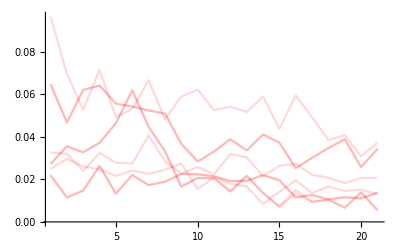

```mathematica
myredsPlot = myreds//ListLinePlot[#,PlotStyle->Opacity[.15,Red] , PlotRange->All]&
```

#### GREEN INTENSITIES :

```mathematica
mygreensAll = myRNAfitsAllG[[All,1,All,4,2,1]] ;
mygreensAllPlot = mygreensAll//ListLinePlot[#,PlotStyle->Opacity[.5,Darker[Green]]  ] & ;
```

```mathematica
loParameter = 0;
hiParameter = 0.3;
```

{{0.0514161,0.0522305,0.0743783,0.0824004,0.0680132,0.0648483,0.0688249,0,0.022132,0.0183768,0.0179755,0.0479016,0.0275232,0.122603,0,0,0,0.106479,0.119866,0.0127217,□},{0.0514161,0.0522305,0.0743783,0.0824004,0.0680132,0.0648483,0.0688249,0,0.022132,0.0183768,0.0179755,0.0479016,0.0275232,0.122603,0,0.0185567,0,0.106479,0.119866,0.0127217,□},{0.0733031,0.0546334,0.0742239,0,0.0459911,0.0688952,0.0445297,0.0458399,0.0477125,0.0733528,0.025676,0.0893356,0.0790474,0.0523084,0.046005,0.0757942,0.014659,0.0321295,0.0233317,0.0237504,0.0935113},{0.0492138,0.043015,0.0318149,□,0.0689605,0.0705665,0.0523618,□,0.0285355,0.0323151,□,0.035463,0.0717024,0.0389552,0.052893,0.0548071,0,0,0.0493611,0,0.0368029},{0.173862,0,0,0.0455139,0.0743046,0.0756889,0.0182189,0,0.0687624,0,0,0.0786821,0.0345841,0.0673203,0.085714,0.0430739,0.0543136,0.0504139,0.030612,0.04372,0.0393078},{0.088848,0.0481251,0.0571166,0,0.107024,0.0505578,0,0.0578875,0.0829158,0.0787914,0,0.0420119,0.0579437,0.084409,0.0810266,0.0661823,0.0304919,0.0348265,0.0715226,0.0408744,0.0249104},{0.088848,0.0481251,0.0571166,0,0.107024,0.0505578,0,0.0578875,0.0829158,0.0787914,0,0.0420119,0.0579437,0.084409,0.0810266,0.0661823,0.0304919,0.0348265,0.0715226,0.0408744,0.0249104},{0.173862,0,0,0.0455139,0.0743046,0.0756889,0.0182189,0,0.0687624,0,0,0.0786821,0.0345841,0.0673203,0.085714,0.0430739,0.0543136,0.0504139,0.030612,0.04372,0.0393078},{0.0654506,0.0645311,0.00739404,0.0328744,0.0552759,0.0244041,0.0255463,0.0289015,0,□,0.0282085,0,0.0278961,0.0193478,0.0558516,0.0211064,0.0290738,0,0.0563757,0.0372587,0.0306141}}

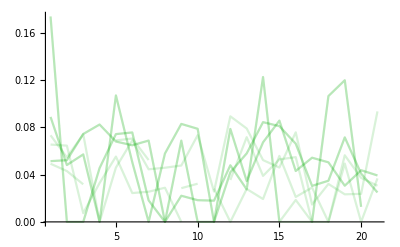

```mathematica
mygreens = mygreensAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &
mygreensPlot = mygreens//ListLinePlot[#,PlotStyle->Opacity[.15,Darker@Green] , PlotRange->All]&
```

#### BLUE INTENSITIES :

{{0.0379968,0.0479578,0.0528118,0.0588388,0.0424393,0.0844657,0.0868312,0.0949284,0.015708,0.0531821,0.0375807,0.0699076,0.0504095,0.0505835,0,0.0364786,0.0419198,0.0340741,0.032098,0.060635,0.0719776},{0.0379968,0.0479578,0.0528118,0.0588388,0.0424393,0.0844657,0.0868312,0.0949284,0.015708,0.0531821,0.0375807,0.0699076,0.0504095,0.0505835,0,0.0295737,0.0419198,0.0340741,0.032098,0.060635,0.0719776},{0.0725749,0.0465959,0.0730354,0.0577373,0.0759085,0.0616954,0.0450682,0.0466362,0.0399629,0.0453105,0.0580134,0.0646346,0.069501,0.0400033,0.0257851,0.045958,0.0309473,0.0292921,0.0273964,0.0263049,0.0533306},{0.0558363,0.0600843,0.0504984,0.0780273,0.0720649,0.0705252,0.0405522,0.063107,0.085701,0.0564447,0.0633871,0.0513663,0.0616264,0.0704827,0.0510198,0.0646155,0.0561985,0.0616816,0.0574858,0.0504416,0.0502643},{0.0526322,0.0446977,0.01603,0.0334276,0.0409909,0.0350576,0.0207051,0.0493302,0.0409777,0.0420868,0.0311651,0.0180444,0.0235868,0.027093,0.0356305,0.0309353,0.0304095,0.0506631,0.0301376,0.0320406,0.0286473},{0.0251884,0.0113299,0.0324674,0.016354,0.0168258,0,0.0152332,0,0.006611,0.0114856,0.0191228,0.010775,0.0147639,0.0242669,0.0171164,0.0175295,0.00627803,0.00573487,0.00933691,0.012002,0.00729296},{0.0251884,0.0113299,0.0324674,0.016354,0.0168258,0,0.0152332,0,0.006611,0.0114856,0.0191228,0.010775,0.0147639,0.0242669,0.0171164,0.0175295,0.00627803,0.00573487,0.00933691,0.012002,0.00729296},{0.0526322,0.0446977,0.01603,0.0334276,0.0409909,0.0350576,0.0207051,0.0493302,0.0409777,0.0420868,0.0311651,0.0180444,0.0235868,0.027093,0.0356305,0.0309353,0.0304095,0.0506631,0.0301376,0.0320406,0.0286473},{0.0140634,0,0.00437405,0.0288868,0.0109416,0.0230216,0.0107145,0.0264524,0,0.0173076,0.0149883,0.0102448,0.00905824,0.214614,0.0220388,0.00502951,0.00860932,0.0238523,0.0078207,0.00593109,0.0151365}}

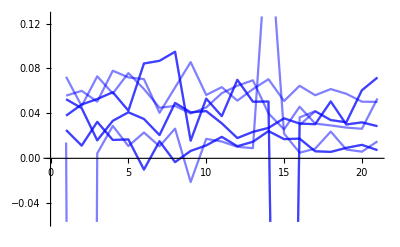

```mathematica
mybluesAll = myRNAfitsAllB[[All,1,All,4,2,1]] ;
myblues = mybluesAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &
mybluessAllPlot = mybluesAll//ListLinePlot[#,PlotStyle->Opacity[.5,Blue] ]&
```

```mathematica
loParameter = 0;
hiParameter = 0.2;
```

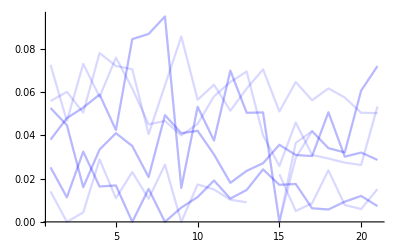

```mathematica
myblues = mybluesAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &;
mybluesPlot = myblues//ListLinePlot[#,PlotStyle->Opacity[.15,Blue] , PlotRange->All]&
```

#### Total of all track intensities in the cell

NOTE! This is an average of the 2 later together. The time is ~shifted by 1/2 a period.

#### Testing and determining how to do it... (DEV only)

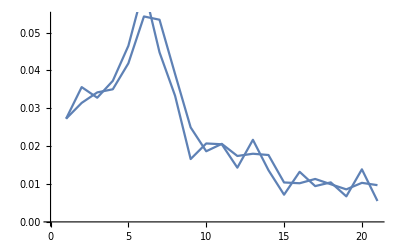

```mathematica
Show[ ListLinePlot/@{tempredlist ,myreds[[1]]} ]
```

```mathematica
tempredlist = Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 1, 1}] }
```

{0.0272523,0.0314246,0.0341961,0.0350248,0.04188,0.0542533,0.0533923,0.0390457,0.0249522,0.0186551,0.0206065,0.0174104,0.0180002,0.0176621,0.0104149,0.0102057,0.0113399,0.00994474,0.00858826,0.0103124,0.00970192}

```mathematica
tempredlist = Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 2, 1}], myreds[[track, -1]] }
Length@myreds[[1]]
```

{0.0272523,0.0314246,0.0341961,0.0350248,0.04188,0.0542533,0.0533923,0.0390457,0.0249522,0.0186551,0.0206065,0.0174104,0.0180002,0.0176621,0.0104149,0.0102057,0.0113399,0.00994474,0.00858826,0.0103124,0.00551879}

21

#### Averaging the total intensities by a 2f rolling average (set back 1/2 a period)

```mathematica
(*myRedRollingAvg = Table[ Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 1, 1}] } , {track,1,Length@myreds}] ;
```

```mathematica
myRedRollingAvg = myreds/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&  ;
```

```mathematica
myGreenRollingAvg = mygreens/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&   ;
```

```mathematica
myBlueRollingAvg = myblues/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&  ;
```

```mathematica
myRedTotal = myRedRollingAvg/.Placeholder[]->0//Mean@#&
myGreenTotal = myGreenRollingAvg/.Placeholder[]->0//Mean@#&
myBlueTotal = myBlueRollingAvg/.Placeholder[]->0//Mean@#&
```

{0.0424986,0.0389924,0.0356446,0.0392624,0.03968,0.0395214,0.0411581,0.0370615,0.0316043,0.0282078,0.027373,0.0275032,0.0276314,0.0272755,0.0252946,0.0233762,0.0221008,0.0209576,0.0208791,0.0198023,0.0192483}

{0.0906911,0.0655062,0.041073,0.0369514,0.0532008,0.0674981,0.0468101,0.0270579,0.0341325,0.0402152,0.0216578,0.030657,0.0489299,0.0598902,0.0637504,0.0487226,0.0334511,0.0349395,0.0549244,0.0460395,0.0302781}

{0.0415677,0.0382645,0.0358432,0.0395788,0.0411844,0.0418731,0.0408979,0.0425882,0.0376094,0.0324905,0.0358165,0.0353236,0.0356337,0.0351155,0.0288172,0.026829,0.0295308,0.0304855,0.0295343,0.0293267,0.0348111}

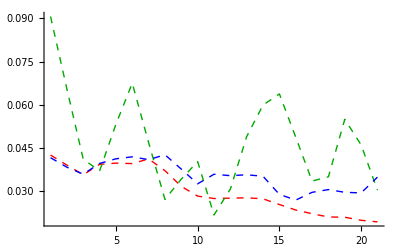

```mathematica
myTotalsPlot = Show[ Table[ ListLinePlot[{myRedTotal,myGreenTotal,myBlueTotal}[[i]],PlotStyle->{Thick, Dashed, {Red,Darker@Green,Blue}[[i]] }, PlotRange->All], {i,1,3}] , PlotRange->All]
```

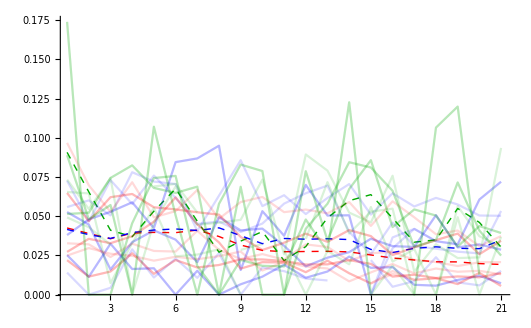

```mathematica
Show[ myTotalsPlot, mybluesPlot, myredsPlot, mygreensPlot , PlotRange-> All]
```

#### Line of best fit :

```mathematica
myfits = Fit[ #, {1,x},x]&/@{myRedTotal,myGreenTotal,myBlueTotal}
```

{0.0436578-0.00121966 x,0.0566182-0.000920367 x,0.0422315-0.000622248 x}

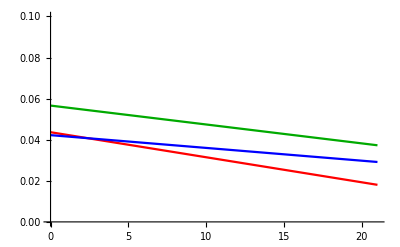

```mathematica
Show@ Table[ 
Plot[myfits[[i]], {x,0,21}, PlotStyle->{Red, Darker@Green, Blue}[[i]]  , PlotRange->{{All,All},{0,.1}}] , {i,1,3}]
```

# With 2f rolling averages of cropped images (SAME as above except with 2 frame rolling avg of trimmed crops before calculating the gaussian)

## Graph intensities :

Run this code for each CELL file

```mathematica
myRNAtrackFilesAll=FileNames["MAX_*03*_myTrack_red_*.dat",DirectoryName@analysisFolder] ;
myRNAtrackFiles = myRNAtrackFilesAll⟦Flatten@Position[Flatten@(StringPosition[#,"."]&/@myRNAtrackFilesAll)⟦All,All,2⟧-Flatten@(StringPosition[#,"myTrack"]&/@myRNAtrackFilesAll)⟦All,All,2⟧,x_/;x<9]⟧
Length@myRNAtrackFiles
```

{/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_11.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_13.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_1.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_23.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_33.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_46.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_56.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_66.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_71.dat}

9

```mathematica
myRNAtracks0=Get/@myRNAtrackFiles;
myRNAtracks=
DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks0;
Dimensions/@myRNAtracks
```

{{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3}}

```mathematica
(*mymovie = FileNames["/Volumes/BITTY/_60-90m/20190508-9_TA_9s-int_60m/MAX_TA13-RGBonly.tif"] [[1]]
myColMovie =Import[mymovie]//Partition[#,3]&//Transpose;
```

```mathematica
mytemplocs = myRNAtracks[[All,All,3,1]];
Dimensions/@mytemplocs
```

{{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2}}

```mathematica
tempFileNamePosition = StringPosition[ myRNAtrackFilesAll[[1]],{"/Analysis/","_myTrack"} ];
myColMovieFile = StringTake[ myRNAtrackFilesAll[[1]],{1,tempFileNamePosition[[1,1]] -1}]  <> StringTake[ myRNAtrackFilesAll[[1]],  {tempFileNamePosition[[1,2]],tempFileNamePosition[[2,1]] -1} ] <>".tif"
myColMovie =Import[myColMovieFile]//Partition[#,3]&//Transpose;
```

/Volumes/BITTY/_60-90m/20180707_TA_90m/MAX_TL03_90m-1.tif

```mathematica
Length@myRNAtracks
```

9

#### Particle Fit gaussian on each frame of each track in the CELL

Gaussian Fit all cell’s tracks : RED

```mathematica
temp=Table[
MyParticleFitterRollingAvgCC[myColMovie,1,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

```mathematica
myRNAfitsAllR = temp[[All,1]];
myRNAImgDataAllR = temp[[All,3]];
myRedCroppedDataAllR = temp[[All,3]]; (*Saves trimmed crop data*)
myRedCentersAllR = temp[[All,3]];
Dimensions/@myRNAfitsAllR
Dimensions/@myRedCroppedDataAllR
Dimensions/@myRedCentersAllR
Dimensions/@myRNAImgDataAllR
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

Gaussian Fit all cell’s tracks : GREEN

```mathematica
temp=Table[
MyParticleFitterRollingAvgCC[myColMovie,2,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

General::munfl: Exp[-1034.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-755.138] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
myRNAfitsAllG = temp[[All,1]];
myRedCroppedDataAllG = temp[[All,2]];
myRedCroppedDataAllG = temp[[All,3]]; (*Saves trimmed crop data*)
myRedCentersAllG = temp[[All,3]];
Dimensions/@myRNAfitsAllG
Dimensions/@myRedCroppedDataAllG
Dimensions/@myRedCentersAllG
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

Gaussian Fit all cell’s tracks : BLUE

```mathematica
temp=Table[
MyParticleFitterRollingAvgCC[myColMovie,3,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

General::munfl: Exp[-7356.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7356.08] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7356.05] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

```mathematica
myRNAfitsAllB = temp[[All,1]];
myRedCroppedDataAllB = temp[[All,2]];
myRedCroppedDataAllB = temp[[All,3]]; (*Saves trimmed crop data*)
myRedCentersAllB = temp[[All,3]];
Dimensions/@myRNAfitsAllB
Dimensions/@myRedCroppedDataAllB
Dimensions/@myRedCentersAllB
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

#### Save fit data :

Parameters...

```mathematica
analysisFolder
color=1;
myColorNames = {"RED","GRN","BLU"};
```

/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1

```mathematica
myParticleFitterHeader = {{"trackN"},{"frameN"},{{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}},
{{"X fit position","Y fit position"},{"Ch Intensity","Background Intensity"},{"SigmaX","SigmaY"}} , 
{{{ "X 90% Conf IntMin","'Max" },{ "Y 90% Conf IntMin","'Max" }},
{{ "Ch Intensity 90% Conf Int Min","'Max" } ,{ "Background Intensity 90% Conf IntMin","'Max" }},{{ "SigmaX 90% Conf Int Min","'Max" },{ "SigmaY 90% Conf IntMin","'Max" }}}  };
myParticleFitterHeader//Dimensions/@#&
```

{{1},{1},{1,10},{3,2},{3,2,2}}

Exporting data...

```mathematica
Table[
{myRedCentersAllR,myRedCentersAllG,myRedCentersAllB}[[color]]>>(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) , {color,1,3}];
```

```mathematica
(*how to retrive crop files...*)
testR =<<(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat" )//Dimensions/@#&
testG =<<(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) //Dimensions/@#&
```

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

```mathematica
Table[
{myRNAfitsAllR,myRNAfitsAllG,myRNAfitsAllB}[[color]]>>(  analysisFolder <> "_All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) , {color,1,3}];
```

### Plotting the intensity data :

#### RED INTENSITIES :

```mathematica
myredsAll = myRNAfitsAllR[[All,1,All,4,2,1]] ;
myredsAllPlot = myredsAll//ListLinePlot[#,PlotStyle->Opacity[.15,Red] , PlotRange->All]&;
```

```mathematica
myredsAll0 = myredsAll /.x_/;x<0 -> 0
```

{{0.0302937,0.0343781,0.035219,0.0415136,0.0514705,0.0499898,0.0359187,0.0225182,0.0166669,0.0186511,0.016218,0.0171542,0.0137789,0.00752994,0.00808278,0.0107403,0.00966431,0.00812409,0.00877389,0.00947827,0.00551879},{0.0302937,0.0343781,0.035219,0.0415136,0.0514705,0.0499898,0.0359187,0.0225182,0.0166669,0.0186511,0.016218,0.0171542,0.0137789,0.00752994,0.00531215,0.0045865,0.00966431,0.00812409,0.00877389,0.00947827,0.00551879},{0.0759742,0.0581297,0.0613837,0.0601599,0.0477961,0.0545201,0.0558352,0.0529761,0.0597239,0.0566986,0.053046,0.0515789,0.0548392,0.0503452,0.043536,0.0354453,0.0327947,0.0375727,0.0357583,0.0335496,0.0373429},{0.0303279,0.0277032,0.0279482,0.0296886,0.0277668,0.0311022,0.0339777,0.0256765,0.0227217,0.0223983,0.0258692,0.0292291,0.0241525,0.0228558,0.024883,0.023649,0.0207853,0.0186512,0.018797,0.0205496,0.0207507},{0.054226,0.054145,0.0605212,0.0590926,0.0540952,0.0487614,0.0481165,0.0385912,0.0278069,0.027484,0.0355354,0.0357307,0.0362554,0.0388991,0.0300973,0.0274099,0.0301423,0.0356685,0.0318839,0.0288764,0.0343386},{0.0167135,0.0129748,0.0206274,0.0184144,0.0165981,0.018306,0.0161952,0.0193351,0.0212275,0.0202601,0.0189677,0.0189486,0.0200164,0.0183737,0.0149687,0.0119765,0.0111133,0.0108052,0.00970703,0.0118787,0.0137387},{0.0167135,0.0129748,0.0206274,0.0184144,0.0165981,0.018306,0.0161952,0.0193351,0.0212275,0.0202601,0.0189677,0.0189486,0.0200164,0.0183737,0.0149687,0.0119765,0.0111133,0.0108052,0.00970703,0.0118787,0.0137387},{0.054226,0.054145,0.0605212,0.0590926,0.0540952,0.0487614,0.0481165,0.0385912,0.0278069,0.027484,0.0355354,0.0357307,0.0362554,0.0388991,0.0300973,0.0274099,0.0301423,0.0356685,0.0318839,0.0288764,0.0343386},{0.0273247,0.027371,0.0251184,0.0208327,0.0227663,0.0236722,0.0233797,0.0231328,0.019677,0.0170948,0.0190887,0.0167875,0.0124149,0.0108771,0.0164014,0.0161127,0.0142497,0.0156046,0.0139123,0.0127049,0.0129752}}

```mathematica
loParameter = 0;
hiParameter = 1;(*0.018;
```

```mathematica
myreds = myredsAll0 /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &;
```

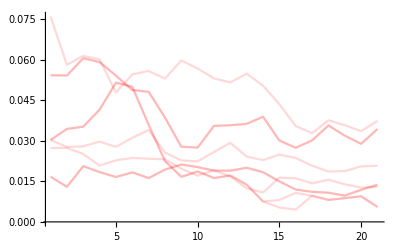

```mathematica
myredsPlot = myreds//ListLinePlot[#,PlotStyle->Opacity[.15,Red] , PlotRange->All]&
```

#### GREEN INTENSITIES :

```mathematica
mygreensAll = myRNAfitsAllG[[All,1,All,4,2,1]] ;
mygreensAllPlot = mygreensAll//ListLinePlot[#,PlotStyle->Opacity[.5,Darker[Green]]  ] & ;
```

```mathematica
loParameter = 0;
hiParameter = 0.3;
```

{{0.0482686,0.0585426,0.070398,0.0714576,0.0600947,0.0631192,0.049034,0.0272391,0.0177989,0.0158048,0.0264093,0.0291623,0.0111174,0.0263826,0,0,0.0823693,0.111604,0.00721961,0.0410563,□},{0.0482686,0.0585426,0.070398,0.0714576,0.0600947,0.0631192,0.049034,0.0272391,0.0177989,0.0158048,0.0264093,0.0291623,0.0111174,0.0263826,0,0,0.0823693,0.111604,0.00721961,0.0410563,□},{0.0615266,0.057165,0.0579758,0,0.039835,0.0387774,0.0454048,0.035711,0.0553719,0.0547913,0.070319,0.0750949,0.0595486,0.0451036,0.0476096,0.0404501,0.0336167,0.0399628,0.0385302,0.0271971,0.0935113},{0.0276929,0.0369076,0.0497933,0.0607155,0.0637213,0.0616423,0.0357787,0.0463119,0.0360113,0.0536538,0.0249639,0.0205584,□,0.0289838,0.0522351,0.0337902,0,0.0272951,0.00349938,0.037883,0.0368029},{0,0.026118,0.0166882,0.0569374,0.0742893,0.0592535,0,0.0432668,0.0488298,0,0.0676589,0.0535455,0.0668724,0.0571764,0.0557816,0.0322949,0.036768,0.0409626,0.0444086,0.0298059,0.0393078},{0.0466055,0.0458105,0.0356805,0.0560981,0.0689972,0.0503299,0,0.0649173,0.068026,0.0467258,0.0422703,0.0411157,0.050882,0.0639119,0.0670745,0.047199,0.0241622,0.0105836,0.033677,0.0361159,0.0249104},{0.0466055,0.0458105,0.0356805,0.0560981,0.0689972,0.0503299,0,0.0649173,0.068026,0.0467258,0.0422703,0.0411157,0.050882,0.0639119,0.0670745,0.047199,0.0241622,0.0105836,0.033677,0.0361159,0.0249104},{0,0.026118,0.0166882,0.0569374,0.0742893,0.0592535,0,0.0432668,0.0488298,0,0.0676589,0.0535455,0.0668724,0.0571764,0.0557816,0.0322949,0.036768,0.0409626,0.0444086,0.0298059,0.0393078},{0.0259517,0,0.0299528,0.0376027,0.0261614,0.0276435,0.0258508,0.0171737,0,□,0,0.0274363,0.023972,0.0357054,0.018334,0.0248752,0,0.0244675,0.0222153,0.0154873,0.0306141}}

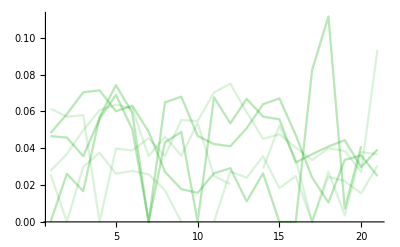

```mathematica
mygreens = mygreensAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &
mygreensPlot = mygreens//ListLinePlot[#,PlotStyle->Opacity[.15,Darker@Green] , PlotRange->All]&
```

#### BLUE INTENSITIES :

{{0.0378025,0.0504205,0.0475929,0.0477424,0.0617013,0.0801643,0.0714959,0.0424453,0.0371553,0.0436875,0.0419511,0.0535601,0.0293627,0.0248512,0.0308938,0.0210137,0.0366505,0.0284436,0.0456471,0.0634818,0.0719776},{0.0378025,0.0504205,0.0475929,0.0477424,0.0617013,0.0801643,0.0714959,0.0424453,0.0371553,0.0436875,0.0419511,0.0535601,0.0293627,0.0248512,0,0.0336638,0.0366505,0.0284436,0.0456471,0.0634818,0.0719776},{0.0538814,0.0551694,0.0606839,0.0600513,0.0592465,0.0465895,0.0454596,0.0420172,0.031351,0.0364733,0.048084,0.0400305,0.0524404,0.0302124,0.0347011,0.0335601,0.0191673,0.0196064,0.0165276,0.03723,0.0533306},{0.0519065,0.0496308,0.0607724,0.0614006,0.0650787,0.047781,0.0513088,0.0710931,0.0590298,0.0541959,0.0502526,0.0460145,0.0643628,0.0586904,0.0527727,0.0554669,0.0577656,0.0579691,0.049814,0.0500699,0.0502643},{0.0456021,0.0302433,0.0225512,0.0350764,0.0358207,0.0234153,0.0299049,0.0369064,0.0344849,0.0298253,0.0216475,0.0200038,0.0223759,0.0306132,0.0305287,0.0300678,0.0369503,0.0365158,0.0305611,0.0284584,0.0286473},{0.0175225,0.0131346,0.0151876,0.0157053,0.0138287,0.0136061,0.00835687,0,0.00595491,0.0131049,0.0148014,0.0114345,0.0183641,0.0176382,0.0157739,0.0103567,0.00606169,0.00774581,0.00937176,0.00607038,0.00729296},{0.0175225,0.0131346,0.0151876,0.0157053,0.0138287,0.0136061,0.00835687,0,0.00595491,0.0131049,0.0148014,0.0114345,0.0183641,0.0176382,0.0157739,0.0103567,0.00606169,0.00774581,0.00937176,0.00607038,0.00729296},{0.0456021,0.0302433,0.0225512,0.0350764,0.0358207,0.0234153,0.0299049,0.0369064,0.0344849,0.0298253,0.0216475,0.0200038,0.0223759,0.0306132,0.0305287,0.0300678,0.0369503,0.0365158,0.0305611,0.0284584,0.0286473},{0.0132373,□,0.0149792,0.0219116,0.012489,0.0141532,0.0166189,0.0138352,0.0122991,0.0126807,0.00920142,0.0093717,0.0117417,0.0183081,0.00437799,0.010994,0.0157458,0.014297,0.009095,0.0131545,0.0151365}}

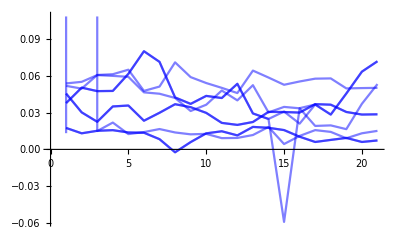

```mathematica
mybluesAll = myRNAfitsAllB[[All,1,All,4,2,1]] ;
myblues = mybluesAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &
mybluessAllPlot = mybluesAll//ListLinePlot[#,PlotStyle->Opacity[.5,Blue] ]&
```

```mathematica
loParameter = 0;
hiParameter = 0.2;
```

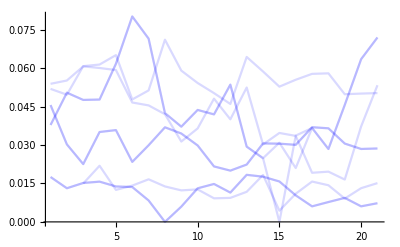

```mathematica
myblues = mybluesAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &;
mybluesPlot = myblues//ListLinePlot[#,PlotStyle->Opacity[.15,Blue] , PlotRange->All]&
```

#### Total of all track intensities in the cell

NOTE! This is an average of the 2 later together. The time is ~shifted by 1/2 a period.

#### Testing and determining how to do it... (DEV only)

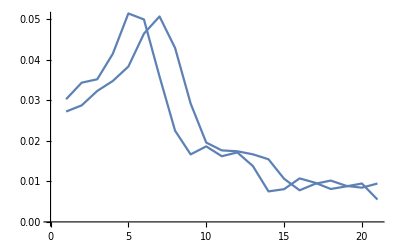

```mathematica
Show[ ListLinePlot/@{tempredlist ,myreds[[1]]} ]
```

```mathematica
tempredlist = Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 1, 1}] }
```

{0.0302937,0.0323359,0.0347985,0.0383663,0.0464921,0.0507302,0.0429543,0.0292185,0.0195925,0.017659,0.0174345,0.0166861,0.0154666,0.0106544,0.00780636,0.00941152,0.0102023,0.0088942,0.00844899,0.00912608,0.00749853}

```mathematica
tempredlist = Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 2, 1}], myreds[[track, -1]] }
Length@myreds[[1]]
```

{0.0302937,0.0323359,0.0347985,0.0383663,0.0464921,0.0507302,0.0429543,0.0292185,0.0195925,0.017659,0.0174345,0.0166861,0.0154666,0.0106544,0.00780636,0.00941152,0.0102023,0.0088942,0.00844899,0.00912608,0.00551879}

21

#### Averaging the total intensities by a 2f rolling average (set back 1/2 a period)

```mathematica
(*myRedRollingAvg = Table[ Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 1, 1}] } , {track,1,Length@myreds}] ;
```

```mathematica
myRedRollingAvg = myreds/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&  ;
```

```mathematica
myGreenRollingAvg = mygreens/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&   ;
```

```mathematica
myBlueRollingAvg = myblues/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&  ;
```

```mathematica
myRedTotal = myRedRollingAvg/.Placeholder[]->0//Mean@#&
myGreenTotal = myGreenRollingAvg/.Placeholder[]->0//Mean@#&
myBlueTotal = myBlueRollingAvg/.Placeholder[]->0//Mean@#&
```

{0.0373437,0.0362385,0.0368547,0.0386615,0.03841,0.0381148,0.0365035,0.0320182,0.0275666,0.0256948,0.0260238,0.026706,0.026265,0.0247329,0.022335,0.0198697,0.018832,0.019483,0.0194567,0.0186927,0.0191962}

{0.0338799,0.036663,0.041015,0.0472533,0.0557658,0.0561082,0.0376984,0.0319525,0.0405964,0.033011,0.0334148,0.0410387,0.0395556,0.0414444,0.0427014,0.0345552,0.0321288,0.0410134,0.0362712,0.0294099,0.0324382}

{0.0356533,0.0340709,0.0333053,0.0359728,0.0388848,0.0390228,0.0375443,0.034364,0.0301955,0.029692,0.0300513,0.0294306,0.0296758,0.0290092,0.0260426,0.0250499,0.0270862,0.0271826,0.0268822,0.0301707,0.0350579}

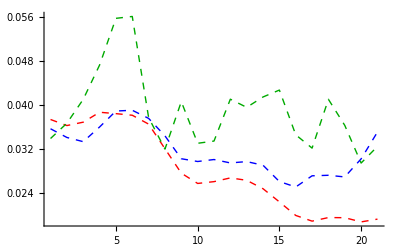

```mathematica
myTotalsPlot = Show[ Table[ ListLinePlot[{myRedTotal,myGreenTotal,myBlueTotal}[[i]],PlotStyle->{Thick, Dashed, {Red,Darker@Green,Blue}[[i]] }, PlotRange->All], {i,1,3}] , PlotRange->All]
```

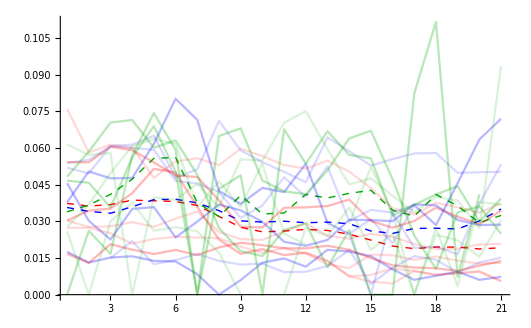

```mathematica
Show[ myTotalsPlot, mybluesPlot, myredsPlot, mygreensPlot , PlotRange-> All]
```

#### Line of best fit :

```mathematica
myfits = Fit[ #, {1,x},x]&/@{myRedTotal,myGreenTotal,myBlueTotal}
```

{0.0409281-0.00117096 x,0.0440409-0.000462958 x,0.0367498-0.000464936 x}

```mathematica
myfits = Fit[ #, {1,x},x]&/@{myRedTotal,myGreenTotal,myBlueTotal}
```

{0.0431654-0.00126231 x,0.0581884-0.00137395 x,0.0395375-0.000677383 x}

{0.0436578-0.00121966 x,0.0566182-0.000920367 x,0.0422315-0.000622248 x}

```mathematica
Show@ Table[ 
Plot[myfits[[i]], {x,0,21}, PlotStyle->{Red, Darker@Green, Blue}[[i]]  , PlotRange->{{All,All},{0,.1}}] , {i,1,3}]
```

-Graphics-

## Reconstruct Trim Images for visualization

#### Reconstruct images from ImageData

```mathematica
Length@myRNAtrackFiles
```

9

```mathematica
myRNAfitsAllR//Dimensions
```

{9,1,21,5}

```mathematica
myRNAfitsAllR[[1,1]];
```

```mathematica
myTrimsR  = Table[ Table[ ImageAdjust@Image@myRedCroppedDataAllR[[crop,1,frame]], {frame,1,Length@myRedCroppedDataAllR[[crop,1]]}], {crop,1,Length@myRedCroppedDataAllR}];
myTrimsG  = Table[ Table[ ImageAdjust@Image@myRedCroppedDataAllG[[crop,1,frame]], {frame,1,Length@myRedCroppedDataAllG[[crop,1]]}], {crop,1,Length@myRedCroppedDataAllG}];
myTrimsB  = Table[ Table[ ImageAdjust@Image@myRedCroppedDataAllB[[crop,1,frame]], {frame,1,Length@myRedCroppedDataAllB[[crop,1]]}], {crop,1,Length@myRedCroppedDataAllB}];
```

#### Make one mean trim from each track

FUCK I think this will error out if there’s no trim there..... dammmmmmmmmmit fix eventually

```mathematica
myMeanTrimImgs  =  {Table[ Mean@ myTrimsR[[All,frame]], {frame,1,Length@myTrimsR[[1]]}] , 
Table[ Mean@ myTrimsG[[All,frame]], {frame,1,Length@myTrimsG[[1]]}] , 
Table[ Mean@ myTrimsB[[All,frame]], {frame,1,Length@myTrimsB[[1]]}] }   ; 
myMeanTrimImgsRGB  =Table[ ColorCombine@myMeanTrimImgs[[All,frame]] , {frame,1,Length@myMeanTrimImgs[[1]]}] ; 
GraphicsGrid[ {myMeanTrimImgsRGB}, ImageSize->Full ]
```

-Graphics-

# DEV: With 2f rolling averages of cropped images after resampling (SAME as above except with 2 frame rolling avg of trimmed crops before calculating the gaussian)

## Graph intensities :

Run this code for each CELL file

```mathematica
myRNAtrackFilesAll=FileNames["MAX_*03*_myTrack_red_*.dat",DirectoryName@analysisFolder] ;
myRNAtrackFiles = myRNAtrackFilesAll⟦Flatten@Position[Flatten@(StringPosition[#,"."]&/@myRNAtrackFilesAll)⟦All,All,2⟧-Flatten@(StringPosition[#,"myTrack"]&/@myRNAtrackFilesAll)⟦All,All,2⟧,x_/;x<9]⟧
Length@myRNAtrackFiles
```

{/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_11.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_13.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_1.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_23.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_33.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_46.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_56.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_66.dat,/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1_myTrack_red_71.dat}

9

```mathematica
myRNAtracks0=Get/@myRNAtrackFiles;
myRNAtracks=
DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks0;
Dimensions/@myRNAtracks
```

{{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3},{21,3}}

```mathematica
(*mymovie = FileNames["/Volumes/BITTY/_60-90m/20190508-9_TA_9s-int_60m/MAX_TA13-RGBonly.tif"] [[1]]
myColMovie =Import[mymovie]//Partition[#,3]&//Transpose;
```

```mathematica
mytemplocs = myRNAtracks[[All,All,3,1]];
Dimensions/@mytemplocs
```

{{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2},{21,2}}

```mathematica
tempFileNamePosition = StringPosition[ myRNAtrackFilesAll[[1]],{"/Analysis/","_myTrack"} ];
myColMovieFile = StringTake[ myRNAtrackFilesAll[[1]],{1,tempFileNamePosition[[1,1]] -1}]  <> StringTake[ myRNAtrackFilesAll[[1]],  {tempFileNamePosition[[1,2]],tempFileNamePosition[[2,1]] -1} ] <>".tif"
myColMovie =Import[myColMovieFile]//Partition[#,3]&//Transpose;
```

/Volumes/BITTY/_60-90m/20180707_TA_90m/MAX_TL03_90m-1.tif

```mathematica
Length@myRNAtracks
```

9

#### Particle Fit gaussian on each frame of each track in the CELL

Gaussian Fit all cell’s tracks : RED

```mathematica
temp=Table[
MyParticleFitterRollingAvgCC[myColMovie,1,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

```mathematica
myRNAfitsAllR = temp[[All,1]];
myRNAImgDataAllR = temp[[All,3]];
myRedCroppedDataAllR = temp[[All,3]]; (*Saves trimmed crop data*)
myRedCentersAllR = temp[[All,3]];
Dimensions/@myRNAfitsAllR
Dimensions/@myRedCroppedDataAllR
Dimensions/@myRedCentersAllR
Dimensions/@myRNAImgDataAllR
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

Gaussian Fit all cell’s tracks : GREEN

```mathematica
temp=Table[
MyParticleFitterRollingAvgCC[myColMovie,2,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

General::munfl: Exp[-1034.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-755.138] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
myRNAfitsAllG = temp[[All,1]];
myRedCroppedDataAllG = temp[[All,2]];
myRedCroppedDataAllG = temp[[All,3]]; (*Saves trimmed crop data*)
myRedCentersAllG = temp[[All,3]];
Dimensions/@myRNAfitsAllG
Dimensions/@myRedCroppedDataAllG
Dimensions/@myRedCentersAllG
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

Gaussian Fit all cell’s tracks : BLUE

```mathematica
temp=Table[
MyParticleFitterRollingAvgCC[myColMovie,3,{myRNAtracks[[track]]},5,1] , {track,1,Length@myRNAtracks}];
```

General::munfl: Exp[-7356.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7356.08] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7356.05] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

```mathematica
myRNAfitsAllB = temp[[All,1]];
myRedCroppedDataAllB = temp[[All,2]];
myRedCroppedDataAllB = temp[[All,3]]; (*Saves trimmed crop data*)
myRedCentersAllB = temp[[All,3]];
Dimensions/@myRNAfitsAllB
Dimensions/@myRedCroppedDataAllB
Dimensions/@myRedCentersAllB
```

{{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5},{1,21,5}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

#### Save fit data :

Parameters...

```mathematica
analysisFolder
color=1;
myColorNames = {"RED","GRN","BLU"};
```

/Volumes/BITTY/_60-90m/20180707_TA_90m/Analysis/MAX_TL03_90m-1

```mathematica
myParticleFitterHeader = {{"trackN"},{"frameN"},{{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}},
{{"X fit position","Y fit position"},{"Ch Intensity","Background Intensity"},{"SigmaX","SigmaY"}} , 
{{{ "X 90% Conf IntMin","'Max" },{ "Y 90% Conf IntMin","'Max" }},
{{ "Ch Intensity 90% Conf Int Min","'Max" } ,{ "Background Intensity 90% Conf IntMin","'Max" }},{{ "SigmaX 90% Conf Int Min","'Max" },{ "SigmaY 90% Conf IntMin","'Max" }}}  };
myParticleFitterHeader//Dimensions/@#&
```

{{1},{1},{1,10},{3,2},{3,2,2}}

Exporting data...

```mathematica
Table[
{myRedCentersAllR,myRedCentersAllG,myRedCentersAllB}[[color]]>>(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) , {color,1,3}];
```

```mathematica
(*how to retrive crop files...*)
testR =<<(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat" )//Dimensions/@#&
testG =<<(  analysisFolder <> "_CROPS-All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) //Dimensions/@#&
```

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

{{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11},{1,21,11,11}}

```mathematica
Table[
{myRNAfitsAllR,myRNAfitsAllG,myRNAfitsAllB}[[color]]>>(  analysisFolder <> "_All-fit-tracks-"<>myColorNames[[color]]<>".dat"  ) , {color,1,3}];
```

### Plotting the intensity data :

#### RED INTENSITIES :

```mathematica
myredsAll = myRNAfitsAllR[[All,1,All,4,2,1]] ;
myredsAllPlot = myredsAll//ListLinePlot[#,PlotStyle->Opacity[.15,Red] , PlotRange->All]&;
```

```mathematica
myredsAll0 = myredsAll /.x_/;x<0 -> 0
```

{{0.0302937,0.0343781,0.035219,0.0415136,0.0514705,0.0499898,0.0359187,0.0225182,0.0166669,0.0186511,0.016218,0.0171542,0.0137789,0.00752994,0.00808278,0.0107403,0.00966431,0.00812409,0.00877389,0.00947827,0.00551879},{0.0302937,0.0343781,0.035219,0.0415136,0.0514705,0.0499898,0.0359187,0.0225182,0.0166669,0.0186511,0.016218,0.0171542,0.0137789,0.00752994,0.00531215,0.0045865,0.00966431,0.00812409,0.00877389,0.00947827,0.00551879},{0.0759742,0.0581297,0.0613837,0.0601599,0.0477961,0.0545201,0.0558352,0.0529761,0.0597239,0.0566986,0.053046,0.0515789,0.0548392,0.0503452,0.043536,0.0354453,0.0327947,0.0375727,0.0357583,0.0335496,0.0373429},{0.0303279,0.0277032,0.0279482,0.0296886,0.0277668,0.0311022,0.0339777,0.0256765,0.0227217,0.0223983,0.0258692,0.0292291,0.0241525,0.0228558,0.024883,0.023649,0.0207853,0.0186512,0.018797,0.0205496,0.0207507},{0.054226,0.054145,0.0605212,0.0590926,0.0540952,0.0487614,0.0481165,0.0385912,0.0278069,0.027484,0.0355354,0.0357307,0.0362554,0.0388991,0.0300973,0.0274099,0.0301423,0.0356685,0.0318839,0.0288764,0.0343386},{0.0167135,0.0129748,0.0206274,0.0184144,0.0165981,0.018306,0.0161952,0.0193351,0.0212275,0.0202601,0.0189677,0.0189486,0.0200164,0.0183737,0.0149687,0.0119765,0.0111133,0.0108052,0.00970703,0.0118787,0.0137387},{0.0167135,0.0129748,0.0206274,0.0184144,0.0165981,0.018306,0.0161952,0.0193351,0.0212275,0.0202601,0.0189677,0.0189486,0.0200164,0.0183737,0.0149687,0.0119765,0.0111133,0.0108052,0.00970703,0.0118787,0.0137387},{0.054226,0.054145,0.0605212,0.0590926,0.0540952,0.0487614,0.0481165,0.0385912,0.0278069,0.027484,0.0355354,0.0357307,0.0362554,0.0388991,0.0300973,0.0274099,0.0301423,0.0356685,0.0318839,0.0288764,0.0343386},{0.0273247,0.027371,0.0251184,0.0208327,0.0227663,0.0236722,0.0233797,0.0231328,0.019677,0.0170948,0.0190887,0.0167875,0.0124149,0.0108771,0.0164014,0.0161127,0.0142497,0.0156046,0.0139123,0.0127049,0.0129752}}

```mathematica
loParameter = 0;
hiParameter = 1;(*0.018;
```

```mathematica
myreds = myredsAll0 /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &;
```

```mathematica
myredsPlot = myreds//ListLinePlot[#,PlotStyle->Opacity[.15,Red] , PlotRange->All]&
```

-Graphics-

#### GREEN INTENSITIES :

```mathematica
mygreensAll = myRNAfitsAllG[[All,1,All,4,2,1]] ;
mygreensAllPlot = mygreensAll//ListLinePlot[#,PlotStyle->Opacity[.5,Darker[Green]]  ] & ;
```

```mathematica
loParameter = 0;
hiParameter = 0.3;
```

```mathematica
mygreens = mygreensAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &
mygreensPlot = mygreens//ListLinePlot[#,PlotStyle->Opacity[.15,Darker@Green] , PlotRange->All]&
```

{{0.0482686,0.0585426,0.070398,0.0714576,0.0600947,0.0631192,0.049034,0.0272391,0.0177989,0.0158048,0.0264093,0.0291623,0.0111174,0.0263826,0,0,0.0823693,0.111604,0.00721961,0.0410563,□},{0.0482686,0.0585426,0.070398,0.0714576,0.0600947,0.0631192,0.049034,0.0272391,0.0177989,0.0158048,0.0264093,0.0291623,0.0111174,0.0263826,0,0,0.0823693,0.111604,0.00721961,0.0410563,□},{0.0615266,0.057165,0.0579758,0,0.039835,0.0387774,0.0454048,0.035711,0.0553719,0.0547913,0.070319,0.0750949,0.0595486,0.0451036,0.0476096,0.0404501,0.0336167,0.0399628,0.0385302,0.0271971,0.0935113},{0.0276929,0.0369076,0.0497933,0.0607155,0.0637213,0.0616423,0.0357787,0.0463119,0.0360113,0.0536538,0.0249639,0.0205584,□,0.0289838,0.0522351,0.0337902,0,0.0272951,0.00349938,0.037883,0.0368029},{0,0.026118,0.0166882,0.0569374,0.0742893,0.0592535,0,0.0432668,0.0488298,0,0.0676589,0.0535455,0.0668724,0.0571764,0.0557816,0.0322949,0.036768,0.0409626,0.0444086,0.0298059,0.0393078},{0.0466055,0.0458105,0.0356805,0.0560981,0.0689972,0.0503299,0,0.0649173,0.068026,0.0467258,0.0422703,0.0411157,0.050882,0.0639119,0.0670745,0.047199,0.0241622,0.0105836,0.033677,0.0361159,0.0249104},{0.0466055,0.0458105,0.0356805,0.0560981,0.0689972,0.0503299,0,0.0649173,0.068026,0.0467258,0.0422703,0.0411157,0.050882,0.0639119,0.0670745,0.047199,0.0241622,0.0105836,0.033677,0.0361159,0.0249104},{0,0.026118,0.0166882,0.0569374,0.0742893,0.0592535,0,0.0432668,0.0488298,0,0.0676589,0.0535455,0.0668724,0.0571764,0.0557816,0.0322949,0.036768,0.0409626,0.0444086,0.0298059,0.0393078},{0.0259517,0,0.0299528,0.0376027,0.0261614,0.0276435,0.0258508,0.0171737,0,□,0,0.0274363,0.023972,0.0357054,0.018334,0.0248752,0,0.0244675,0.0222153,0.0154873,0.0306141}}

-Graphics-

#### BLUE INTENSITIES :

```mathematica
mybluesAll = myRNAfitsAllB[[All,1,All,4,2,1]] ;
myblues = mybluesAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &
mybluessAllPlot = mybluesAll//ListLinePlot[#,PlotStyle->Opacity[.5,Blue] ]&
```

{{0.0378025,0.0504205,0.0475929,0.0477424,0.0617013,0.0801643,0.0714959,0.0424453,0.0371553,0.0436875,0.0419511,0.0535601,0.0293627,0.0248512,0.0308938,0.0210137,0.0366505,0.0284436,0.0456471,0.0634818,0.0719776},{0.0378025,0.0504205,0.0475929,0.0477424,0.0617013,0.0801643,0.0714959,0.0424453,0.0371553,0.0436875,0.0419511,0.0535601,0.0293627,0.0248512,0,0.0336638,0.0366505,0.0284436,0.0456471,0.0634818,0.0719776},{0.0538814,0.0551694,0.0606839,0.0600513,0.0592465,0.0465895,0.0454596,0.0420172,0.031351,0.0364733,0.048084,0.0400305,0.0524404,0.0302124,0.0347011,0.0335601,0.0191673,0.0196064,0.0165276,0.03723,0.0533306},{0.0519065,0.0496308,0.0607724,0.0614006,0.0650787,0.047781,0.0513088,0.0710931,0.0590298,0.0541959,0.0502526,0.0460145,0.0643628,0.0586904,0.0527727,0.0554669,0.0577656,0.0579691,0.049814,0.0500699,0.0502643},{0.0456021,0.0302433,0.0225512,0.0350764,0.0358207,0.0234153,0.0299049,0.0369064,0.0344849,0.0298253,0.0216475,0.0200038,0.0223759,0.0306132,0.0305287,0.0300678,0.0369503,0.0365158,0.0305611,0.0284584,0.0286473},{0.0175225,0.0131346,0.0151876,0.0157053,0.0138287,0.0136061,0.00835687,0,0.00595491,0.0131049,0.0148014,0.0114345,0.0183641,0.0176382,0.0157739,0.0103567,0.00606169,0.00774581,0.00937176,0.00607038,0.00729296},{0.0175225,0.0131346,0.0151876,0.0157053,0.0138287,0.0136061,0.00835687,0,0.00595491,0.0131049,0.0148014,0.0114345,0.0183641,0.0176382,0.0157739,0.0103567,0.00606169,0.00774581,0.00937176,0.00607038,0.00729296},{0.0456021,0.0302433,0.0225512,0.0350764,0.0358207,0.0234153,0.0299049,0.0369064,0.0344849,0.0298253,0.0216475,0.0200038,0.0223759,0.0306132,0.0305287,0.0300678,0.0369503,0.0365158,0.0305611,0.0284584,0.0286473},{0.0132373,□,0.0149792,0.0219116,0.012489,0.0141532,0.0166189,0.0138352,0.0122991,0.0126807,0.00920142,0.0093717,0.0117417,0.0183081,0.00437799,0.010994,0.0157458,0.014297,0.009095,0.0131545,0.0151365}}

-Graphics-

```mathematica
loParameter = 0;
hiParameter = 0.2;
```

```mathematica
myblues = mybluesAll /.x_/;x<0  -> loParameter  //#/.x_/;x>hiParameter -> Placeholder[]  &;
mybluesPlot = myblues//ListLinePlot[#,PlotStyle->Opacity[.15,Blue] , PlotRange->All]&
```

-Graphics-

#### Total of all track intensities in the cell

NOTE! This is an average of the 2 later together. The time is ~shifted by 1/2 a period.

#### Testing and determining how to do it... (DEV only)

```mathematica
Show[ ListLinePlot/@{tempredlist ,myreds[[1]]} ]
```

-Graphics-

```mathematica
tempredlist = Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 1, 1}] }
```

{0.0302937,0.0323359,0.0347985,0.0383663,0.0464921,0.0507302,0.0429543,0.0292185,0.0195925,0.017659,0.0174345,0.0166861,0.0154666,0.0106544,0.00780636,0.00941152,0.0102023,0.0088942,0.00844899,0.00912608,0.00749853}

```mathematica
tempredlist = Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 2, 1}], myreds[[track, -1]] }
Length@myreds[[1]]
```

{0.0302937,0.0323359,0.0347985,0.0383663,0.0464921,0.0507302,0.0429543,0.0292185,0.0195925,0.017659,0.0174345,0.0166861,0.0154666,0.0106544,0.00780636,0.00941152,0.0102023,0.0088942,0.00844899,0.00912608,0.00551879}

21

#### Averaging the total intensities by a 2f rolling average (set back 1/2 a period)

```mathematica
(*myRedRollingAvg = Table[ Flatten@{myreds[[track,1]], Table[ 
Mean@myreds[[track,i;;i+1]] , {i, 1, Length@myreds[[track]] - 1, 1}] } , {track,1,Length@myreds}] ;
```

```mathematica
myRedRollingAvg = myreds/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&  ;
```

```mathematica
myGreenRollingAvg = mygreens/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&   ;
```

```mathematica
myBlueRollingAvg = myblues/.Placeholder[]->0//Table[ Flatten@{#[[track,1]], Table[ 
Mean@#[[track,i;;i+1]] , {i, 1, Length@#[[track]] - 1, 1}] } , {track,1,Length@#}]&  ;
```

```mathematica
myRedTotal = myRedRollingAvg/.Placeholder[]->0//Mean@#&
myGreenTotal = myGreenRollingAvg/.Placeholder[]->0//Mean@#&
myBlueTotal = myBlueRollingAvg/.Placeholder[]->0//Mean@#&
```

{0.0373437,0.0362385,0.0368547,0.0386615,0.03841,0.0381148,0.0365035,0.0320182,0.0275666,0.0256948,0.0260238,0.026706,0.026265,0.0247329,0.022335,0.0198697,0.018832,0.019483,0.0194567,0.0186927,0.0191962}

{0.0338799,0.036663,0.041015,0.0472533,0.0557658,0.0561082,0.0376984,0.0319525,0.0405964,0.033011,0.0334148,0.0410387,0.0395556,0.0414444,0.0427014,0.0345552,0.0321288,0.0410134,0.0362712,0.0294099,0.0324382}

{0.0356533,0.0340709,0.0333053,0.0359728,0.0388848,0.0390228,0.0375443,0.034364,0.0301955,0.029692,0.0300513,0.0294306,0.0296758,0.0290092,0.0260426,0.0250499,0.0270862,0.0271826,0.0268822,0.0301707,0.0350579}

```mathematica
myTotalsPlot = Show[ Table[ ListLinePlot[{myRedTotal,myGreenTotal,myBlueTotal}[[i]],PlotStyle->{Thick, Dashed, {Red,Darker@Green,Blue}[[i]] }, PlotRange->All], {i,1,3}] , PlotRange->All]
```

-Graphics-

```mathematica
Show[ myTotalsPlot, mybluesPlot, myredsPlot, mygreensPlot , PlotRange-> All]
```

-Graphics-

#### Line of best fit :

```mathematica
myfits = Fit[ #, {1,x},x]&/@{myRedTotal,myGreenTotal,myBlueTotal}
```

{0.0409281-0.00117096 x,0.0440409-0.000462958 x,0.0367498-0.000464936 x}

```mathematica
myfits = Fit[ #, {1,x},x]&/@{myRedTotal,myGreenTotal,myBlueTotal}
```

{0.0431654-0.00126231 x,0.0581884-0.00137395 x,0.0395375-0.000677383 x}

{0.0436578-0.00121966 x,0.0566182-0.000920367 x,0.0422315-0.000622248 x}

```mathematica
Show@ Table[ 
Plot[myfits[[i]], {x,0,21}, PlotStyle->{Red, Darker@Green, Blue}[[i]]  , PlotRange->{{All,All},{0,.1}}] , {i,1,3}]
```

-Graphics-

## Reconstruct Trim Images for visualization

#### Reconstruct images from ImageData

```mathematica
Length@myRNAtrackFiles
```

9

```mathematica
myRNAfitsAllR//Dimensions
```

{9,1,21,5}

```mathematica
myRNAfitsAllR[[1,1]];
```

```mathematica
myTrimsR  = Table[ Table[ ImageAdjust@Image@myRedCroppedDataAllR[[crop,1,frame]], {frame,1,Length@myRedCroppedDataAllR[[crop,1]]}], {crop,1,Length@myRedCroppedDataAllR}];
myTrimsG  = Table[ Table[ ImageAdjust@Image@myRedCroppedDataAllG[[crop,1,frame]], {frame,1,Length@myRedCroppedDataAllG[[crop,1]]}], {crop,1,Length@myRedCroppedDataAllG}];
myTrimsB  = Table[ Table[ ImageAdjust@Image@myRedCroppedDataAllB[[crop,1,frame]], {frame,1,Length@myRedCroppedDataAllB[[crop,1]]}], {crop,1,Length@myRedCroppedDataAllB}];
```

#### Make one mean trim from each track

FUCK I think this will error out if there’s no trim there..... dammmmmmmmmmit fix eventually

```mathematica
myMeanTrimImgs  =  {Table[ Mean@ myTrimsR[[All,frame]], {frame,1,Length@myTrimsR[[1]]}] , 
Table[ Mean@ myTrimsG[[All,frame]], {frame,1,Length@myTrimsG[[1]]}] , 
Table[ Mean@ myTrimsB[[All,frame]], {frame,1,Length@myTrimsB[[1]]}] }   ; 
myMeanTrimImgsRGB  =Table[ ColorCombine@myMeanTrimImgs[[All,frame]] , {frame,1,Length@myMeanTrimImgs[[1]]}] ; 
GraphicsGrid[ {myMeanTrimImgsRGB}, ImageSize->Full ]
```

-Graphics-